# Supplementary Material: Fitness-valley crossing with generalized parent-offspring transmission

## Matthew M. Osmond & Sarah P. Otto Deptartment of Zoology, University of British Columbia, Vancouver, Canada mmosmond@zoology.ubc.ca

## Inputs

```mathematica
Off[General::Spell];
Off[General::spell1];

AxisSize=30;
LabelSize=24;
TickSize=20;
imagesize=800;
imagepadding={{120,50},{80,50}};
```

```mathematica
(*dir=directory for images*)
dir=NotebookDirectory[]<>"IMAGES/";
```

## Semi-deterministic analysis

### Recursion equations

Consider two traits (loci), A and B, each of which can take on one of two values. Each individual is characterized by its trait combination (genotype), and we let x[i], for i = 1,2,3,4, denote the frequency of A1B1, A2B1, A1B2, and A2B2 types, respectively. In a mating between type i (as the mother) and j (as the father), all four possible offspring types may occur, and we let b[i,j,k] represent the probability of producing an offspring of type k, where ∑_(k=1)^4 b[i,j,k] = 1. Viability selection acts at the haploid stage, immediately before censusing. Relative viability of type i is w[i] and V = Σ_k w[k] Σ_(i,j) x[i] x[j] b[i,j,k] is a normalizing factor that keeps the frequencies summed to one. The expected frequencies in the next generation are

```mathematica
eqn[k_]=Simplify[(w[k]/V)Sum[x[i]x[j]b[i,j,k],{i,1,4},{j,1,4}]];
```

### Initial assumptions

When the number of individuals, N, is large the expected frequencies well approximate the actual frequencies.

To simplify the dynamics, let the probability of mutation (offspring have trait neither parent has, e.g., b[1,1,2] is a mutation in the A trait) be proportional to a small number ϵ. Let the probability of double mutation b[1,1,4] be proportional to ϵ^2. Finally, let the frequencies of the single mutants (A2B1 and A1B2) also be proportional to ϵ, which is justified when the single mutants are selectively disfavoured (i.e., when there is a fitness valley). These assumptions are summarized by

```mathematica
MutAssump={x[2]->ϵ x[2], x[3]->ϵ x[3], b[1,1,4]->ϵ^2 b[1,1,4],b[1,1,2]->ϵ b[1,1,2],b[3,1,2]->ϵ b[3,1,2],b[1,3,2]->ϵ b[1,3,2],b[1,1,3]->ϵ b[1,1,3],b[2,1,3]->ϵ b[2,1,3],b[1,2,3]->ϵ b[1,2,3],b[2,2,4]->ϵ b[2,2,4],b[3,3,4]->ϵ b[3,3,4],b[1,2,4]->ϵ b[1,2,4],b[2,1,4]->ϵ b[2,1,4],b[1,3,4]->ϵ b[1,3,4],b[3,1,4]->ϵ b[3,1,4]};
```

### Single mutant dynamics

Assuming A1B1 is initially fixed, the expected frequency of A2B1 in the next generation is, to first order in ϵ,

```mathematica
x2p=Collect[Series[eqn[2]/.x[1]->1-x[2]-x[3]-x[4]/.MutAssump,{ϵ,0,1}],{V,w[i_],x[i_],x[i_] x[j_]},Factor]/.x[4]->0/.ϵ->1
```

(w[2] (b[1,1,2]+(b[1,2,2]+b[2,1,2]) x[2]))/V

Let mb[i,j,k] = (b[i,j,k] + b[j,i,k]) / 2 and mbs[i,j,k] = mb[i,j,k] w[k] be the mean transmission probabilities before and after selection, respectively. And let us write μs[i,j,k] = mbs[i,j,k] when this transmission requires a mutation. Our equation then simplifies to

```mathematica
x2pSimp=x2p/.b[1,2,2]+b[2,1,2]->(2/w[2])mbs[1,2,2]/.b[1,1,2]->μs[1,1,2]/(w[2])//Simplify
```

(2 mbs[1,2,2] x[2]+μs[1,1,2])/V

This is analogous to equation 2 in Christiansen et al. 1998 (TPB 53:199-215), where 2mbs[1,2,2] is the fitness of A2B1 in a population of residents and μs[1,1,2] is the mutation rate from residents (A1B1) to A2B1.

Assuming V = 1, the frequency of A2B1 in generation t, beginning with x[2] = 0 at t = 0, is approximately

```mathematica
x2t=x2[t]/.RSolve[{x2[t+1]==x2pSimp/.V->1/.x[2]->x2[t],x2[0]==0},x2[t],t][[1]]
```

((-1+2^t mbs[1,2,2]^t) μs[1,1,2])/(-1+2 mbs[1,2,2])

and when mbs[1,2,2] = 1/2 we have

```mathematica
x2tH=x2[t]/.RSolve[{x2[t+1]==x2pSimp/.V->1/.x[2]->x2[t]/.mbs[1,2,2]->1/2,x2[0]==0},x2[t],t][[1]]
```

t μs[1,1,2]

Note that mbs[1,2,2] = 1/2 assumes there is no selection on single mutants in a population of residents (i.e., transmission bias and viability selection are both zero or cancel each other out).

We can derive the analogous equations for A1B2

```mathematica
x3p=Collect[Series[eqn[3]/.x[1]->1-x[2]-x[3]-x[4]/.MutAssump,{ϵ,0,1}],{V,w[i_],x[i_],x[i_] x[j_]},Factor]/.x[4]->0/.ϵ->1;
x3pSimp=x3p/.b[1,3,3]+b[3,1,3]->(2/w[3])mbs[1,3,3]/.b[1,1,3]->μs[1,1,3]/(w[3])//Simplify;
x3t=x3[t]/.RSolve[{x3[t+1]==x3pSimp/.V->1/.x[3]->x3[t],x3[0]==0},x3[t],t][[1]]
x3tH=x3[t]/.RSolve[{x3[t+1]==x3pSimp/.V->1/.x[3]->x3[t]/.mbs[1,3,3]->1/2,x3[0]==0},x3[t],t][[1]]
```

((-1+2^t mbs[1,3,3]^t) μs[1,1,3])/(-1+2 mbs[1,3,3])

t μs[1,1,3]

Denote the total amount of selection on single mutants in a population of residents as s[i] = 2 mbs[1,i,i] - 1. When there has been a large amount of selection, | s[i]* t | > 1, and single mutants are selected against, -1 < s[i] < 0, the frequency of the single mutants (A2B1 and A1B2) approach mutation-selection balance

```mathematica
x2MSB=Limit[x2t/.mbs[1,2,2]->(1+s[2])/2,t->∞,Assumptions->{s[2]<0&&s[2]>-1}]
x3MSB=Limit[x3t/.mbs[1,3,3]->(1+s[3])/2,t->∞,Assumptions->{s[3]<0&&s[3]>-1}]
```

-μs[1,1,2]/s[2]

-μs[1,1,3]/s[3]

### Double mutant dynamics

#### Double mutant probabilities

Assuming there are currently no double mutants (A2B2), x[4]=0, the expected frequency of double mutants in the next generation, before selection, is

```mathematica
x4p=Collect[eqn[4]/w[4]/.x[4]->0,{w[4],wbar,x[i_],x[i_]x[j_]}]/.b[1,1,4]->μ[1,1,4]/.b[2,3,4]->2r[2,3,4]-b[3,2,4]/.b[1,i_,4]->2μ[1,i,4]-b[i,1,4]/.V->1
```

b[2,2,4] x[2]^2+2 r[2,3,4] x[2] x[3]+b[3,3,4] x[3]^2+x[1]^2 μ[1,1,4]+2 x[1] x[2] μ[1,2,4]+2 x[1] x[3] μ[1,3,4]

Here we’ve assumed rare single mutants (such that V = 1) and written r[2,3,4] = (b[2,3,4] + b[3,2,4]) / 2, the average probability that a double mutant is produced from a mating between single mutants (i.e., probability of recombination).

Summing the probability a double mutant arises (its expected frequency when small) over T generations gives the cumulative probability a double mutant arises, given none have yet arisen. 

Here we are more interested in the time until a double mutant lineage appears that fixes. The probability a double mutant’s lineage fixes is (Kimura 1957)

```mathematica
uf=(1-Exp[-2N s p])/(1-Exp[-2N s])
```

(1-ⅇ^(-2 N p s))/(1-ⅇ^(-2 N s))

where s is the selective advantage of the double mutant (or disadvantage if s<0) and p is its initial frequency.

When selection is weak, the population is large, and we begin with one double mutant, we have the familiar first order approximation

```mathematica
Limit[Series[Numerator[uf]/.p->1/N,{s,0, 1}],N->∞]/Limit[Denominator[uf],N->∞,Assumptions->{s>0}]
```

2 s

And when the double mutant individual is neutral, fixation is determined by drift alone and occurs with probability

```mathematica
Limit[uf/.p->1/N,s->0]
```

1/N

1 + s is the expected number of double mutant offspring produced by a newly arisen double mutant. This is the probability of mating with a given type, multiplied by the probability of producing a double mutant offspring, multiplied by the relative probability of surviving. When the double mutant is rare, s is

```mathematica
sDM=w[4]Sum[x[i](b[i,4,4]+b[4,i,4]),{i,1,4}]-1/.x[1]->1-x[2]-x[3]/.x[4]->0
```

-1+w[4] ((b[2,4,4]+b[4,2,4]) x[2]+(b[1,4,4]+b[4,1,4]) (1-x[2]-x[3])+(b[3,4,4]+b[4,3,4]) x[3])

Without recombination, mutation, or transmission bias, we have the simple, and common, expression

```mathematica
sDM/.b[i_,j_,k_]+b[j_,i_,k_]->1
```

-1+w[4]

If the single mutants are sufficiently rare we can approximate the selective advantage with

```mathematica
sDMrare=Normal[Series[sDM/.x[i_]->ϵ x[i],{ϵ,0,0}]]//FullSimplify
```

-1+(b[1,4,4]+b[4,1,4]) w[4]

This is the total amount of selection on double mutants in a population of residents s[4] = w[4] (b[1, 4, 4] + b[4, 1, 4]) - 1, and is what we will use throughout. This greatly simplifies the analysis as double mutant fitness then remains constant over time.

Note that if b[1,4,4] + b[4,1,4] = 1 - r, where r is the probability of recombination, and we write w[4] = 1 + s, where s is the viability advantage of double mutants, we have

```mathematica
sDMrare/.b[1,4,4]+b[4,1,4]->1-r/.w[4]->1+s
```

-1+(1-r) (1+s)

And when s > r and both are small, we have the common first order approximation

```mathematica
sApp=Normal[Series[sDMrare/.b[1,4,4]+b[4,1,4]->1-ϵ r/.w[4]->1+ϵ s,{ϵ,0,1}]]/.ϵ->1
```

-r+s

#### Mutation-selection balance

When the single mutants are at mutation-selection balance, the expected frequency of successful double mutants in the next generation is

```mathematica
x4pMSB=pfix*x4p/.x[1]->1-x[2]-x[3]/.x[2]->x2MSB/.x[3]->x3MSB
```

pfix ((b[2,2,4] μs[1,1,2]^2)/s[2]^2+(2 r[2,3,4] μs[1,1,2] μs[1,1,3])/(s[2] s[3])+(b[3,3,4] μs[1,1,3]^2)/s[3]^2-(2 μ[1,2,4] μs[1,1,2] (1+μs[1,1,2]/s[2]+μs[1,1,3]/s[3]))/s[2]-(2 μ[1,3,4] μs[1,1,3] (1+μs[1,1,2]/s[2]+μs[1,1,3]/s[3]))/s[3]+μ[1,1,4] (1+μs[1,1,2]/s[2]+μs[1,1,3]/s[3])^2)

Summing over T generations gives a rough approximation for the expected frequency of successful double mutants in generation T

```mathematica
x4pSumMSB=Sum[x4pMSB,{n,0,T}]
```

pfix (1+T) ((b[2,2,4] μs[1,1,2]^2)/s[2]^2+(2 r[2,3,4] μs[1,1,2] μs[1,1,3])/(s[2] s[3])+(b[3,3,4] μs[1,1,3]^2)/s[3]^2-(2 μ[1,2,4] μs[1,1,2] (1+μs[1,1,2]/s[2]+μs[1,1,3]/s[3]))/s[2]-(2 μ[1,3,4] μs[1,1,3] (1+μs[1,1,2]/s[2]+μs[1,1,3]/s[3]))/s[3]+μ[1,1,4] (1+μs[1,1,2]/s[2]+μs[1,1,3]/s[3])^2)

Beginning at mutation-selection balance, we therefore expect one successful double mutant by generation

```mathematica
TMSB=T/.Solve[x4pSumMSB==1/N,T][[1]]//FullSimplify
```

-1+(s[2]^2 s[3]^2)/(N pfix (s[3]^2 (b[2,2,4]+μ[1,1,4]-2 μ[1,2,4]) μs[1,1,2]^2+2 s[2] s[3] μs[1,1,2] (s[3] (μ[1,1,4]-μ[1,2,4])+(r[2,3,4]+μ[1,1,4]-μ[1,2,4]-μ[1,3,4]) μs[1,1,3])+s[2]^2 (s[3]^2 μ[1,1,4]+2 s[3] (μ[1,1,4]-μ[1,3,4]) μs[1,1,3]+(b[3,3,4]+μ[1,1,4]-2 μ[1,3,4]) μs[1,1,3]^2)))

Adding the time to reach mutation-selection balance, T_0 = max(1/s[2], 1/s[3]), gives the waiting time from a population which is initially composed only of residents.

Note that the rate of production of double mutants from mutation-selection balance, when reduced to the symmetric Mendelian case with s >> r [such that pfix = 2(s - r) ~ 2s], weak selection, δ, and rare mutation, μ, is approximately

```mathematica
WeissEq4d=Normal[Series[ 1/TMSB/. μ[1,1,4]->μ^2/.s[i_]->-δ/.μs[i_,i_,k_]->w[k]μ/.r[i_,j_,4]->r/2/.pfix->2s/.w[4]->1+s/.w[i_]->1-δ/.μ[i_,j_,k_]->μ/2/.b[i_,i_,4]->μ/.μ->μ ϵ/.δ->ϵ δ/.s->ϵ  s,{ϵ,0,1}]]/.ϵ->1//FullSimplify
```

(2 N r s μ^2)/δ^2

this is the last line of equation 4 in Weissman et al. 2010 (who ignore numerical factors, i.e., 2).

#### Dynamic single mutants (Appendix A)

Assuming rare single mutants, rare mutations, and | s[i] |<<1 (weakly non-neutral single mutants), to fourth order the probability a successful double mutant arises by T generations is

```mathematica
x4pDM=x4p*pfix/.x[1]->1-x[2]-x[3]/.x[i_]->x[i]ϵ/.x[2]->x2t/.x[3]->x3t/.mbs[1,i_,i_]->(1+s[i])/2/.μs[i_,j_,k_]->w[k]μ[i,j,k]/.b[i_,i_,4]->b[i,i,4]ϵ/.μ[1,1,4]->μ[1,1,4] ϵ^2/.μ[1,2,4]->μ[1,2,4]ϵ/.μ[1,3,4]->μ[1,3,4]ϵ/.μ[1,1,2]->μ[1,1,2]ϵ/.μ[1,1,3]->μ[1,1,3]ϵ/.s[i_]->s[i] ϵ;
x4pDMSum=Sum[x4pDM,{t,0,T}];
x4pDMSumApp=Normal[Series[x4pDMSum,{ϵ,0,4}]]/.ϵ->1;
x4pDMSumAppSimp=Collect[x4pDMSumApp,{pfix,T},FullSimplify]
```

pfix (μ[1,1,4]+1/3 T^3 (w[2] μ[1,1,2] (2 r[2,3,4] w[3] μ[1,1,3]+s[2] μ[1,2,4])+s[3] w[3] μ[1,1,3] μ[1,3,4])+T^2 (r[2,3,4] w[2] w[3] μ[1,1,2] μ[1,1,3]+w[2] μ[1,1,2] (-μ[1,1,4]+μ[1,2,4])+w[3] μ[1,1,3] (-μ[1,1,4]+μ[1,3,4]))+1/3 T (r[2,3,4] w[2] w[3] μ[1,1,2] μ[1,1,3]+3 μ[1,1,4]-w[2] μ[1,1,2] (3 μ[1,1,4]+(-3+s[2]) μ[1,2,4])-w[3] μ[1,1,3] (3 μ[1,1,4]+(-3+s[3]) μ[1,3,4])))

where pfix is the (constant) probabiltity a rare double mutant will fix. pfix is approximately constant over time when single mutants remain sufficiently rare.

Since we don’t explicitly deal with the order of T (e.g., we say that T^3 times its coefficient can be the leading order term, but we don’t justify why T^4 times its coefficient (or T^5, etc.) wouldn’t be even more important) we will compare numerical solutions against x4pDMSum (full solution).

Note that in the absence of selection on single mutants (s[2] = s[3] = 0), the sum is a polynomial whose leading order term is T^3, so we’re guaranteed that the Taylor series in x4pDMSumApp is sufficient:

```mathematica
Collect[Limit[x4pDMSum/.ϵ->1/.s[i_]->s,s->0],{pfix,T}]
```

pfix (μ[1,1,4]+1/6 T^2 (3 b[2,2,4] w[2]^2 μ[1,1,2]^2+6 r[2,3,4] w[2] w[3] μ[1,1,2] μ[1,1,3]+3 b[3,3,4] w[3]^2 μ[1,1,3]^2-6 w[2] μ[1,1,2] μ[1,1,4]+3 w[2]^2 μ[1,1,2]^2 μ[1,1,4]-6 w[3] μ[1,1,3] μ[1,1,4]+6 w[2] w[3] μ[1,1,2] μ[1,1,3] μ[1,1,4]+3 w[3]^2 μ[1,1,3]^2 μ[1,1,4]+6 w[2] μ[1,1,2] μ[1,2,4]-6 w[2]^2 μ[1,1,2]^2 μ[1,2,4]-6 w[2] w[3] μ[1,1,2] μ[1,1,3] μ[1,2,4]+6 w[3] μ[1,1,3] μ[1,3,4]-6 w[2] w[3] μ[1,1,2] μ[1,1,3] μ[1,3,4]-6 w[3]^2 μ[1,1,3]^2 μ[1,3,4])+1/6 T^3 (2 b[2,2,4] w[2]^2 μ[1,1,2]^2+4 r[2,3,4] w[2] w[3] μ[1,1,2] μ[1,1,3]+2 b[3,3,4] w[3]^2 μ[1,1,3]^2+2 w[2]^2 μ[1,1,2]^2 μ[1,1,4]+4 w[2] w[3] μ[1,1,2] μ[1,1,3] μ[1,1,4]+2 w[3]^2 μ[1,1,3]^2 μ[1,1,4]-4 w[2]^2 μ[1,1,2]^2 μ[1,2,4]-4 w[2] w[3] μ[1,1,2] μ[1,1,3] μ[1,2,4]-4 w[2] w[3] μ[1,1,2] μ[1,1,3] μ[1,3,4]-4 w[3]^2 μ[1,1,3]^2 μ[1,3,4])+1/6 T (b[2,2,4] w[2]^2 μ[1,1,2]^2+2 r[2,3,4] w[2] w[3] μ[1,1,2] μ[1,1,3]+b[3,3,4] w[3]^2 μ[1,1,3]^2+6 μ[1,1,4]-6 w[2] μ[1,1,2] μ[1,1,4]+w[2]^2 μ[1,1,2]^2 μ[1,1,4]-6 w[3] μ[1,1,3] μ[1,1,4]+2 w[2] w[3] μ[1,1,2] μ[1,1,3] μ[1,1,4]+w[3]^2 μ[1,1,3]^2 μ[1,1,4]+6 w[2] μ[1,1,2] μ[1,2,4]-2 w[2]^2 μ[1,1,2]^2 μ[1,2,4]-2 w[2] w[3] μ[1,1,2] μ[1,1,3] μ[1,2,4]+6 w[3] μ[1,1,3] μ[1,3,4]-2 w[2] w[3] μ[1,1,2] μ[1,1,3] μ[1,3,4]-2 w[3]^2 μ[1,1,3]^2 μ[1,3,4]))

If there is no recombination between single mutants and they are selectively neutral, the leading term is proportional to T^2.

```mathematica
Cx4pDMMut=x4pDMSumAppSimp/.r[2,3,4]->0/.s[i_]->0
```

pfix (μ[1,1,4]+1/3 T (3 μ[1,1,4]-w[2] μ[1,1,2] (3 μ[1,1,4]-3 μ[1,2,4])-w[3] μ[1,1,3] (3 μ[1,1,4]-3 μ[1,3,4]))+T^2 (w[2] μ[1,1,2] (-μ[1,1,4]+μ[1,2,4])+w[3] μ[1,1,3] (-μ[1,1,4]+μ[1,3,4])))

Assuming large T, the expected time until a successful double mutant is approximately

```mathematica
TDMMut=Solve[T^2 Coefficient[Cx4pDMMut,T,2]==1/N,T][[2]]//FullSimplify
```

{T→1/(√(N pfix (w[2] μ[1,1,2] (-μ[1,1,4]+μ[1,2,4])+w[3] μ[1,1,3] (-μ[1,1,4]+μ[1,3,4]))))}

Ignoring rare double mutations this is

```mathematica
TDMMut/.μ[1,1,4]->0
```

{T→1/(√(N pfix (w[2] μ[1,1,2] μ[1,2,4]+w[3] μ[1,1,3] μ[1,3,4])))}

And when the mutation probabilities for each trait are μ, single mutants are neutral with respect to Darwinian fitness, and we focus on the arrival of any double mutant, pfix = 1, our result reduces to equation 8 in Christiansen et al. 1998

```mathematica
TDMMut/.μ[1,1,4]->0/.μ[1,1,i_]->μ/.μ[1,i_,j_]->μ/2/.w[i_]->1/.pfix->1
```

{T→1/(√(N μ^2))}

With selection, recombination, and large T, the dominant term (in our fourth order approximation, which is accurate for small s[i]) is proportional to T^3and the expected time is approximately

```mathematica
TDMR=Solve[T^3 Coefficient[x4pDMSumAppSimp,T,3]==1/N,T][[2]]//FullSimplify
```

{T→3^(1/3)/(N pfix (w[2] μ[1,1,2] (2 r[2,3,4] w[3] μ[1,1,3]+s[2] μ[1,2,4])+s[3] w[3] μ[1,1,3] μ[1,3,4]))^(1/3)}

Reducing to the neutral genetic case gives equation 9 in Christiansen et al. 1998:

```mathematica
TDMR/.μ[1,1,i_]->μ/.μ[1,i_,4]->μ/2/.s[i_]->0/.w[i_]->1/.r[2,3,4]->r/2/.pfix->1
```

{T→3^(1/3)/((N r μ^2)^(1/3))}

Letting r[2,3,4] = r / 2, mutation at each trait be μ, and assuming no double mutations, no transmission bias, and equal selection on single mutants s[2] = s[3] = s, we see that the approximation for deleterious single mutants is only valid (positive) when recombination is frequent relative to selection on single mutants r > -s / (1 - s) ~ -s

```mathematica
Reduce[r>0&&μ>0&&N>0&&s<0&&pfix>0&&0<T/.TDMR/.r[2,3,4]->r/2/.μ[1,1,4]->0/.μ[1,1,i_]->μ/.μ[1,i_,4]->μ/2 /.s[i_]->s/.w[i_]->1-s,r]
```

N>0&&pfix>0&&s<0&&μ>0&&r>s/(-1+s)

#### Comparing semi-deterministic results (Figure A1)

Here we will use Mendelian assumptions to simplify the comparison of our various semi-deterministic results

```mathematica
Mendel={b[1,1,4]->μ^2,b[1,1,i_]->μ,b[1,4,4]->(1-r)/2,b[4,1,4]->(1-r)/2,b[2,3,4]->r/2,b[3,2,4]->r/2,b[1,i_,i_]->1/2,b[i_,1,i_]->1/2,b[1,2,4]->μ/2,b[2,1,4]->μ/2,b[1,3,4]->μ/2,b[3,1,4]->μ/2,b[2,2,4]->μ,b[3,3,4]->μ};
```

The waiting times are

```mathematica
MSBFull=TMSB+1/δ/.s[i_]->w[i](b[1,i,i]+b[i,1,i])-1/.pfix->uf/.p->1/N/.s->sDMrare/.μs[i_,j_,k_]->w[k](b[i,j,k]+b[j,i,k])/2/.μ[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.r[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.Mendel/.w[2]->1-δ/.w[3]->1-δ/.w[4]->1+s;

MutFull=T/.TDMMut/.s[i_]->w[i](b[1,i,i]+b[i,1,i])-1/.pfix->uf/.p->1/N/.s->sDMrare/.μs[i_,j_,k_]->w[k](b[i,j,k]+b[j,i,k])/2/.r[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.μ[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.Mendel/.w[2]->1-δ/.w[3]->1-δ/.w[4]->1+s;

RecFull=T/.TDMR/.s[i_]->w[i](b[1,i,i]+b[i,1,i])-1/.pfix->uf/.p->1/N/.s->sDMrare/.μs[i_,j_,k_]->w[k](b[i,j,k]+b[j,i,k])/2/.r[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.μ[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.Mendel/.w[2]->1-δ/.w[3]->1-δ/.w[4]->1+s;
```

Which approximation does well depends on whether δ T < 1 or δ T > 1. Below we illustrate this by increasing δ (which simultaneously increases T, making a fairly sharp transition):

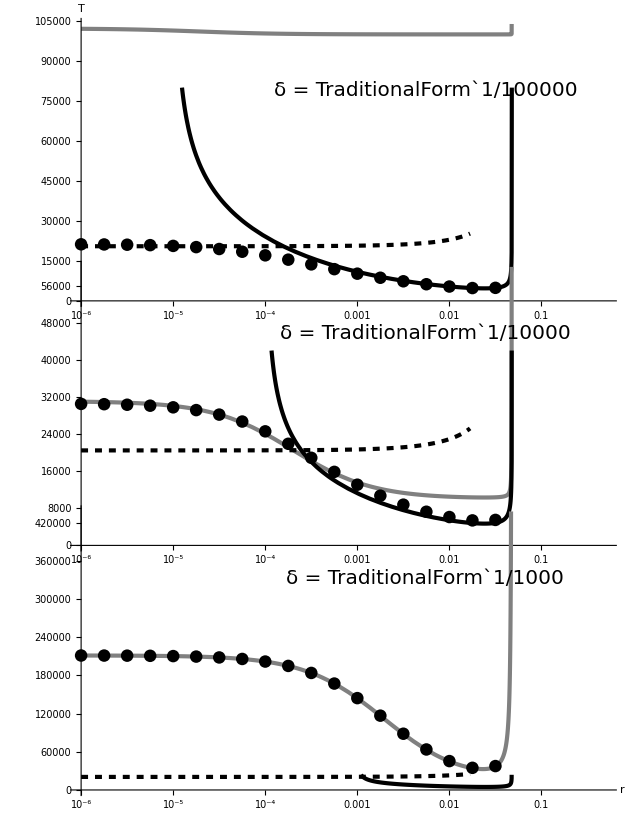

```mathematica
δtemp=10^-5;
stemp=0.05;
μtemp=5*10^-7;
Ntemp=10^5;
ymax=Automatic;

GraphicsColumn[{
Show[

(*total time assuming MSB*)
LogLinearPlot[MSBFull/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp,{r,10^-6,0.5},PlotStyle->{Gray,Thickness[0.005]},PlotRange->{0,ymax}],
(*time from mutation, i.e., only T^2 term*)
LogLinearPlot[MutFull/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp,{r,10^-6,0.5},PlotStyle->{Black,Dashed,Thickness[0.005]}],
(*time from recombination, i.e., only T^3 term*)
LogLinearPlot[RecFull/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp,{r,10^-6,0.5},PlotStyle->{Black,Thickness[0.005]}],
(*full solution*)
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(x4pDMSum/.ϵ->1/.s[i_]->w[i](b[1,i,i]+b[i,1,i])-1/.pfix->uf/.p->1/N/.s->sDMrare/.μs[i_,j_,k_]->w[k](b[i,j,k]+b[j,i,k])/2/.r[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.μ[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.Mendel/.w[2]->1-δ/.w[3]->1-δ/.w[4]->1+s/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp/.r->10^x)==(1/N/.N->Ntemp),{T,15000},WorkingPrecision->50]]},{x,-6,-3/2,1/4}],PlotStyle->{Black,PointSize[0.015]}],

AxesLabel->{(*Style["r",AxisSize]*)"",Style["T",AxisSize]},
ImageSize->600,
ImagePadding->imagepadding,
TicksStyle->{{TickSize,FontOpacity->0},{TickSize}},
PlotRangePadding->None,
Epilog->Text[Style[StringForm["δ = ``",δtemp],20],Scaled[{.65,.75}]]
],

δtemp=10^-4;

Show[

(*total time assuming MSB*)
LogLinearPlot[MSBFull/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp,{r,10^-6,0.5},PlotStyle->{Gray,Thickness[0.005]},PlotRange->{0,ymax}],
(*time from mutation, i.e., only T^2 term*)
LogLinearPlot[MutFull/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp,{r,10^-6,0.5},PlotStyle->{Black,Dashed,Thickness[0.005]}],
(*time from recombination, i.e., only T^3 term*)
LogLinearPlot[RecFull/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp,{r,10^-6,0.5},PlotStyle->{Black,Thickness[0.005]}],
(*full solution*)
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(x4pDMSum/.ϵ->1/.s[i_]->w[i](b[1,i,i]+b[i,1,i])-1/.pfix->uf/.p->1/N/.s->sDMrare/.μs[i_,j_,k_]->w[k](b[i,j,k]+b[j,i,k])/2/.r[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.μ[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.Mendel/.w[2]->1-δ/.w[3]->1-δ/.w[4]->1+s/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp/.r->10^x)==(1/N/.N->Ntemp),{T,100000}]]},{x,-6,-3/2,1/4}],PlotStyle->{Black,PointSize[0.015]}],

(*AxesLabel->{Style["r",AxisSize],Style["T",AxisSize]},*)
ImageSize->600,
ImagePadding->imagepadding,
TicksStyle->{{TickSize,FontOpacity->0},{TickSize}},
PlotRangePadding->None,
Epilog->Text[Style[StringForm["δ = ``",δtemp],20],Scaled[{.65,.75}]]
],

δtemp=10^-3;

Show[

(*total time assuming MSB*)
LogLinearPlot[MSBFull/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp,{r,10^-6,0.5},PlotStyle->{Gray,Thickness[0.005]},PlotRange->{0,ymax}],
(*time from mutation, i.e., only T^2 term*)
LogLinearPlot[MutFull/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp,{r,10^-6,0.5},PlotStyle->{Black,Dashed,Thickness[0.005]}],
(*time from recombination, i.e., only T^3 term*)
LogLinearPlot[RecFull/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp,{r,10^-6,0.5},PlotStyle->{Black,Thickness[0.005]}],
(*full solution*)
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(x4pDMSum/.ϵ->1/.s[i_]->w[i](b[1,i,i]+b[i,1,i])-1/.pfix->uf/.p->1/N/.s->sDMrare/.μs[i_,j_,k_]->w[k](b[i,j,k]+b[j,i,k])/2/.r[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.μ[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.Mendel/.w[2]->1-δ/.w[3]->1-δ/.w[4]->1+s/.δ->δtemp/.s->stemp/.μ->μtemp/.N->Ntemp/.r->10^x)==(1/N/.N->Ntemp),{T,100000}]]},{x,-6,-3/2,1/4}],PlotStyle->{Black,PointSize[0.015]}],

AxesLabel->{Style["r",AxisSize],(*Style["T",AxisSize]*)""},
ImageSize->600,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None,
Epilog->Text[Style[StringForm["δ = ``",δtemp],20],Scaled[{.65,.75}]]
]

},{Center,Center},-100]

Export[dir<>"DetApproxsDeltaBW.eps",%];

Clear[δtemp,stemp,μtemp,Ntemp,ymax]
```

## Stochastic analysis

### Set-up (Appendix B)

The expected frequency of type i in the next generation, given we have frequencies x[j], for j=1,2,3,4, in the current generation, is

```mathematica
xrec[i_]=eqn[i]/.V-> Sum[w[k]Sum[x[i]x[j]b[i,j,k],{i,1,4},{j,1,4}],{k,1,4}];
```

Assuming a Wright-Fisher model with constant and finite population size, N, the offspring in the next generation are chosen, with replacement, from a multinomial distribution with frequency parameters xrec[i]. Let i = x2 N be the number of A2B1 genotypes, j = x3 N the number of A1B2 genotypes, and assume no A2B2 genotypes have yet arisen x4 = 0. Let X(t) = (i,j) describe the numbers of single mutants at time t, with P(ij->kl) the transition probability Pr{ X(t+1) = (k,l) | X(t)=(i,j) } given that no successful A2B2 genotypes are present (we ignore the low frequency of unsuccessful double mutants). Then {X(t), t >= 0} is a Markov process with sub-stochastic transition matrix P(ij->kl). Let the Markov process be killed when a successful A2B2 genotype arises and let the state where any non-zero number of successful A2B2 genotypes exist be H. To complete the transition matrix let P(ij->H) = r = xrec[4] uf, where uf is the fixation probability of the double mutant, and H be an absorbing state, P(H->ij)=0 and P(H->H)=1.

Assuming X(t+1) is not in H the first moment in the change in the numbers of A2B1 and A1B2, E[ΔXi | Xi(t) = i, Xi(t+1) not in H] and E[ΔXj | Xj(t) = i, Xj(t+1) not in H], are

```mathematica
exi=Sum[(k-i) Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->xrec[2]/(1-r)/.q->(xrec[1]+xrec[3])/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]-x[4]/.x[4]->0/.i->x[2] N;
exj=
Sum[(k-j) Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->xrec[3]/(1-r)/.q->(xrec[1]+xrec[2])/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]-x[4]/.x[4]->0/.j->x[3] N;
```

The second moments are

```mathematica
ex2i=Sum[(k-i)^2 Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->xrec[2]/(1-r)/.q->(xrec[1]+xrec[3])/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]-x[4]/.x[4]->0/.i->x[2] N;
ex2j=Sum[(k-j)^2 Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->xrec[3]/(1-r)/.q->(xrec[1]+xrec[2])/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]-x[4]/.x[4]->0/.j->x[3] N;
```

The third moments are

```mathematica
ex3i=Sum[(k-i)^3 Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->xrec[2]/(1-r)/.q->(xrec[1]+xrec[3])/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]-x[4]/.x[4]->0/.i->x[2] N;
ex3j=Sum[(k-j)^3 Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->xrec[3]/(1-r)/.q->(xrec[1]+xrec[2])/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]-x[4]/.x[4]->0/.j->x[3] N;
```

The probability the Markov chain is killed is

```mathematica
kill=1-(1-r)^N;
```

With r small we have

```mathematica
killapprox=Normal[Series[kill,{r,0,1}]]/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]-x[4]/.x[4]->0;
```

To approximate the Markov process with a diffusion process we first want to scale mutation probabilities such that N times mutation remains constant as N->∞. Taking a hint from the genetic case we let:

1) When only two traits present (parents identical):
	b[i,i,i] -> θ[i,i,i]
	b[i,i,k] -> θ[i,i,k] / N, for k with only one trait different from parent (single mutation)
	b[i,i,k] -> θ[i,i,k]/N^2, for k with both traits different from parent (double mutation)

2) When three traits present:
	b[i,j,i] -> θ[i,j,i]
	b[i,j,j] -> θ[i,j,j]
	b[i,j,k] -> θ[i,j,k]/N, for k not i or j (single mutation)

3) When all four traits present:
 	b[i,j,k] -> θ[i,j,k] 
 	
 where O(1/N^a) includes all terms of order 1/N^a and smaller as N->∞. These assumptions can be written:

```mathematica
MutScale={b[i_,i_,i_]->θ[i,i,i],b[1,1,4]->θ[1,1,4]/N^2,b[4,4,1]->θ[4,4,1]/N^2,b[2,2,3]->θ[2,2,3]/N^2,b[3,3,2]->θ[3,3,2]/N^2,b[i_,i_,k_]->θ[i,i,k]/N,b[i_,j_,i_]->θ[i,j,i],b[i_,j_,j_]->θ[i,j,j],b[2,3,k_]->θ[2,3,k],b[3,2,k_]->θ[3,2,k],b[1,4,k_]->θ[1,4,k],b[4,1,k_]->θ[4,1,k],b[i_,j_,k_]->θ[i,j,k]/N};
```

Because we need the transmission probabilities to sum to one as N->∞ we require

1) When two traits present:
	θ[i,i,i] = 1 + O(1/N)

2) When three traits present:
	θ[i,j,i] + θ[i,j,j] = 1 + O(1/N)

3) When all four traits present:
 	θ[i,j,1] + θ[i,j,2] + θ[i,j,3] + θ[i,j,4] = b[i,j,1] + b[i,j,2] + b[i,j,3] + b[i,j,4] = 1
 	
where β is the scaling we will also use for single-mutant frequencies. These assumptions, to first order in 1 / N, are:

```mathematica
MutScaleSum={θ[i_,i_,i_]->1-μ1[i,i]/N,Sum[θ[1,4,k],{k,1,4}]->1,Sum[θ[4,1,k],{k,1,4}]->1,Sum[θ[2,3,k],{k,1,4}]->1,Sum[θ[3,2,k],{k,1,4}]->1,θ[i_,j_,i_]+θ[i_,j_,j_]->1-μ2[i,j]/N,θ[j_,i_,i_]+θ[j_,i_,j_]->1-μ3[j,i]/N};
```

We then need to find the appropriate state and time scalings such that the limiting process converges to a diffusion process with killing as N->∞. Let Y=i/N^β and Z=j/N^β, 0<β<1, be the scaled frequencies of A2B1 and A1B2. We then have Y(t) = Xi (t) / N^β and Z(t) = Xj (t) / N^β. We next let one unit of time in the scaled process τ be N^α generations in the original process, with 0<α | <1. We will look for the α and β such that the infinitesimal variance and killing rates are positive a finite and a moment higher than the second is zero.

We first scale the frequencies. Notice that E[ΔY^2| Y(t)= y=i/N^β]=E[(Y(t+1)-y)^2|Y(t)=y]=N^(-2β)E[Xi(t+1)-i|Xi(t)=i], giving

```mathematica
ex2isc=N^(-2β)ex2i/.x[2]->y N^(β-1)/.x[3]->z N^(β-1);
ex2jsc=N^(-2β)ex2j/.x[2]->y N^(β-1)/.x[3]->z N^(β-1);
```

Then scaling time such that one time unit (generation) in the original process is N^α generations in the scaled process gives

```mathematica
ex2isct=N^α ex2isc;
ex2jsct=N^α ex2jsc;
```

We next scale the transmission probabilities, giving

```mathematica
ex2iSc=ex2isct/.MutScale/.MutScaleSum;
ex2jSc=ex2jsct/.MutScale/.MutScaleSum;
```

and we notice (by visual inspection) that the infinitesimal variances are positive and finite when there is weak selection and α = β. These requirements can be summed up, to to first order, by

```mathematica
SelecAssump={w[1]->1,θ[1,2,2]->(1+S2/N^β)/w[2]-θ[2,1,2],θ[1,3,3]->(1+S3/N^β)/w[3]-θ[3,1,3],N s->S};
```

In words, we assume selection on single mutants to be on the order of N^-β : s[i] = w[i] (θ[1,i,i]+θ[i,1,i])-1 = Si / N^β. We also assume selection on double mutants, s, to be on the order of N^-1, and constant (the single mutants are assumed to remain rare, such that double mutant fitness is approximately s ~ w[4] (θ[1,4,4] + θ[4,1,4]) = sDMrare).

The infinitesimal variances are then (I set α and β to a number below to speed up Mathematica, but, as can be seen by examining smaller sections of the equation separately, this works for all α = β)

```mathematica
(*these take a few minutes*)
Limit[Expand[ex2iSc/.SelecAssump ]/.α->β/.β->1/3,N->∞]
```

y

```mathematica
Limit[Expand[ex2iSc/.SelecAssump]/.α->β/.β->1/2,N->∞]
```

y

```mathematica
Limit[Expand[ex2jSc/.SelecAssump ]/.α->β/.β->1/3,N->∞]
```

z

```mathematica
Limit[Expand[ex2jSc/.SelecAssump ]/.α->β/.β->1/2,N->∞]
```

z

The killing rate is

```mathematica
k2=Collect[Expand[killapprox*N^α/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)],{N,N^α,N^β}]/.α->β;
```

When there is little recombination (on the order of 1/N^β or less), visual inspecition shows that we require β = 1 / 2, and the killing rate is

```mathematica
Limit[Collect[Expand[k2/.MutScale/.MutScaleSum/.SelecAssump],{w[4],N N^α N^β}]/.θ[2,3,4]->R[2,3,4]/N^β/.θ[3,2,4]->R[3,2,4]/N^β/.β->1/2,N->∞]/.w[1]->1
```

uf w[4] (y (z (R[2,3,4]+R[3,2,4])+θ[1,2,4]+θ[2,1,4])+z (θ[1,3,4]+θ[3,1,4]))

When there is more recombination we require β = 1 / 3 and the killing rate is

```mathematica
Limit[k2/.MutScale/.MutScaleSum/.SelecAssump/.β->1/3,N->∞]/.w[1]->1
```

uf y z w[4] (θ[2,3,4]+θ[3,2,4])

Our infinitesimal means are

```mathematica
Limit[N^α N^-β exi/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.α->β/.β->1/2,N->∞]
```

S2 y+w[2] θ[1,1,2]+y^2 (w[2]-θ[1,2,1]-θ[2,1,1])-y z (θ[1,3,1]+θ[3,1,1]-w[2] (θ[2,3,2]+θ[3,2,2]))

```mathematica
Limit[N^α N^-β exi/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.α->β/.β->1/3,N->∞]
```

S2 y+w[2] θ[1,1,2]

```mathematica
Limit[N^α N^-β exj/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.α->β/.β->1/2,N->∞]
```

S3 z+w[3] θ[1,1,3]+z^2 (w[3]-θ[1,3,1]-θ[3,1,1])-y z (θ[1,2,1]+θ[2,1,1]-w[3] (θ[2,3,3]+θ[3,2,3]))

```mathematica
Limit[N^α N^-β exj/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.α->β/.β->1/3,N->∞]
```

S3 z+w[3] θ[1,1,3]

To simplify we assume weak transmission bias in the resident

```mathematica
ResDriveAssump={θ[1,2,1]->1-m2/N^β-θ[2,1,1],θ[1,3,1]->1-m3/N^β-θ[3,1,1]};
```

giving infinitesimal means

```mathematica
Limit[N^α N^-β exi/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.α->β/.β->1/2,N->∞]
```

S2 y+y^2 (-1+w[2])+w[2] θ[1,1,2]+y z (-1+w[2] (θ[2,3,2]+θ[3,2,2]))

```mathematica
Limit[N^α N^-β exi/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.α->β/.β->1/3,N->∞]
```

S2 y+w[2] θ[1,1,2]

```mathematica
Limit[N^α N^-β exj/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.α->β/.β->1/2,N->∞]
```

S3 z-z^2+z^2 w[3]+w[3] θ[1,1,3]+y z (-1+w[3] (θ[2,3,3]+θ[3,2,3]))

```mathematica
Limit[N^α N^-β exj/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.α->β/.β->1/3,N->∞]
```

S3 z+w[3] θ[1,1,3]

To further simplify the dynamics we assume more weak transmission bias, this time between the single mutants

```mathematica
MoreAssumps={θ[2,3,2]->( 1-n2/N^β)-θ[3,2,2],θ[2,3,3]-> (1-n3/N^β)-θ[3,2,3]};
```

giving infinitesimal means

```mathematica
Limit[N^α N^-β exi/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.α->β/.β->1/2,N->∞]
```

S2 y+y^2 (-1+w[2])+y z (-1+w[2])+w[2] θ[1,1,2]

```mathematica
Limit[N^α N^-β exi/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.α->β/.β->1/3,N->∞]
```

S2 y+w[2] θ[1,1,2]

```mathematica
Limit[N^α N^-β exj/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.α->β/.β->1/2,N->∞]
```

S3 z-z^2+y z (-1+w[3])+z^2 w[3]+w[3] θ[1,1,3]

```mathematica
Limit[N^α N^-β exj/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.α->β/.β->1/3,N->∞]
```

S3 z+w[3] θ[1,1,3]

And finally, we assume weak viability selection on single mutants

```mathematica
EvenMoreAssumps={w[2]->1+w2/N^β,w[3]->1+w3/N^β};
```

to have infinitesimal means

```mathematica
Limit[N^α N^-β exi/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/2,N->∞]
```

S2 y+θ[1,1,2]

```mathematica
Limit[N^α N^-β exi/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/3,N->∞]
```

S2 y+θ[1,1,2]

```mathematica
Limit[N^α N^-β exj/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/2,N->∞]
```

S3 z+θ[1,1,3]

```mathematica
Limit[N^α N^-β exj/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/3,N->∞]
```

S3 z+θ[1,1,3]

We see that we have also satisfied the Dynkin condition (Karlin & Taylor 1981 p. 165) - higher moments converge to zero

```mathematica
(*these take a few mintues each*)
Limit[N^α N^(-3β)ex3i/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/2,N->∞]
```

0

```mathematica
Normal[Series[N^α N^(-3β)ex3i/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/3/.N->1/n,{n,0,0}]]/.n->0
```

0

```mathematica
Limit[N^α N^(-3β)ex3j/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/2,N->∞]
```

0

```mathematica
Normal[Series[N^α N^(-3β)ex3j/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/3/.N->1/n,{n,0,0}]]/.n->0
```

0

### Expected crossing time (Appendix C)

The waiting time, T, until the first successful double mutant, in units of N^β generations, solves the PDE given by equation (24) in Christiansen et al. (1998). Below we reduce the PDE to a one dimensional diffusion (i.e., to an ODE) in two special cases, and solve for T. See Christiansen et al. (1998) and Karlin & Taylor 1981 for more information about diffusion processes, the PDEs, and the boundary conditions.

#### Neutral single mutants without recombination

When there is no recombination to double mutants θ[2,3,4] = θ[3,2,4] = 0 and mutation probabilities to double mutants from either single mutant are equal θ[1,2,4] + θ[2,1,4] = θ[1,3,4] + θ[3,1,4] = θ[1,m,4], the killing rate depends only on the sum of the single-mutant frequencies y + z:

```mathematica
killSum=Limit[N^α killapprox/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.θ[2,3,4]->0/.θ[3,2,4]->0/.α->β/.β->1/2,N->∞]/.θ[1,3,4]+θ[3,1,4]->θ[1,m,4]/.θ[1,2,4]+θ[2,1,4]->θ[1,m,4]//Simplify
```

(ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S)) (y+z) w[4] θ[1,m,4])/(-1+ⅇ^(2 S))

The infinitesimal mean is

```mathematica
exSum=Sum[(k-i) Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->(xrec[2]+xrec[3])/(1-r)/.q->xrec[1]/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]/.x[4]->0/.w[1]->1/.i->(x[2]+x[3]) N;
uSum=Limit[N^α N^-β exSum/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/2,N->∞]//FullSimplify
```

S2 y+S3 z+θ[1,1,2]+θ[1,1,3]

and, when there is no selection (Darwinian or transmission bias, or they cancel out) against single mutants, this reduces to

```mathematica
uSumMut=uSum/.S2->0/.S3->0//Simplify
```

θ[1,1,2]+θ[1,1,3]

which is independent of both y and z.

The infinitesimal variance is

```mathematica
σxSum=Sum[(k-i)^2 Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->(xrec[2]+xrec[3])/(1-r)/.q->xrec[1]/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]/.x[4]->0/.w[1]->1/.i->(x[2]+x[3]) N;
σSum=Limit[N^α N^(-2β)σxSum/.x[2]->y N^(β-1)/.x[3]->z N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/2,N->∞]//FullSimplify
```

y+z

which, like the killing rate, only depends on the sum y + z.

The PDE then collapses to the one-dimensional differential equation in ξ = y + z

```mathematica
demut= (1/2)σSum D[T[ξ],ξ,ξ]+ uSumMut D[T[ξ],ξ]-killSum T[ξ]==-1/.y+z->ξ/.w[4]θ[1,m,4] ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S))/(-1+ⅇ^(2 S))->θw[1,m,4]
```

-ξ T[ξ] θw[1,m,4]+(θ[1,1,2]+θ[1,1,3]) T'[ξ]+1/2 ξ T''[ξ]==-1

The boundary conditions are T(∞) = 0 and (d/dξ)T(0)= (- 1)/(θ[1,1,2] + θ[1,1,3]).

The general solution is

```mathematica
tg=T[ξ]/.DSolve[demut,T[ξ],ξ][[1]];
tg2=C[1]Coefficient[tg,C[1]]+C[2]Coefficient[tg,C[2]]+(tg/.C[i_]->0//FullSimplify)
```

ξ^(1/2 (1-2 θ[1,1,2]-2 θ[1,1,3])) BesselJ[1/2 (-1+2 θ[1,1,2]+2 θ[1,1,3]),-ⅈ √2 ξ √θw[1,m,4]] C[1]+ξ^(1/2 (1-2 θ[1,1,2]-2 θ[1,1,3])) BesselY[1/2 (-1+2 θ[1,1,2]+2 θ[1,1,3]),-ⅈ √2 ξ √θw[1,m,4]] C[2]+1/(-1+2 θ[1,1,2]+2 θ[1,1,3])ξ (-2 Hypergeometric0F1[1/2+θ[1,1,2]+θ[1,1,3],1/2 ξ^2 θw[1,m,4]] HypergeometricPFQ[{1/2},{3/2,3/2-θ[1,1,2]-θ[1,1,3]},1/2 ξ^2 θw[1,m,4]]+1/(θ[1,1,2]+θ[1,1,3])Hypergeometric0F1[3/2-θ[1,1,2]-θ[1,1,3],1/2 ξ^2 θw[1,m,4]] HypergeometricPFQ[{θ[1,1,2]+θ[1,1,3]},{1/2+θ[1,1,2]+θ[1,1,3],1+θ[1,1,2]+θ[1,1,3]},1/2 ξ^2 θw[1,m,4]])

We now use the boundary conditions to solve for the constants C[1] and C[2]. First translating Bessel functions into confluent hypergeometric functions (see Abromowitz & Stegun 1972, Handbook of Mathematical Fucntions, 10th ed.) we have

BesselY[a_,b_]→(BesselJ[a,b]Cos[a π]-BesselJ[-a,b])/Sin[a π]		(Abromowitz and Stegun 9.1.2)

BesselJ[a_,b_]->Hypergeometric0F1[a+1,-b^2/4](b/2)^(a)/Gamma[a+1]		(Abromowitz and Stegun 9.1.69)

```mathematica
tg3=Simplify[tg2/.BesselY[a_,b_]->(BesselJ[a,b]Cos[a π]-BesselJ[-a,b])/Sin[a π]/. BesselJ[a_,b_]->Hypergeometric0F1[a+1,-b^2/4](b/2)^(a)/Gamma[a+1],{ξ≥0}]
```

-(2 ξ Hypergeometric0F1[1/2+θ[1,1,2]+θ[1,1,3],1/2 ξ^2 θw[1,m,4]] HypergeometricPFQ[{1/2},{3/2,3/2-θ[1,1,2]-θ[1,1,3]},1/2 ξ^2 θw[1,m,4]])/(-1+2 θ[1,1,2]+2 θ[1,1,3])+(ξ Hypergeometric0F1[3/2-θ[1,1,2]-θ[1,1,3],1/2 ξ^2 θw[1,m,4]] HypergeometricPFQ[{θ[1,1,2]+θ[1,1,3]},{1/2+θ[1,1,2]+θ[1,1,3],1+θ[1,1,2]+θ[1,1,3]},1/2 ξ^2 θw[1,m,4]])/((θ[1,1,2]+θ[1,1,3]) (-1+2 θ[1,1,2]+2 θ[1,1,3]))+(2^(1/4 (-1-2 θ[1,1,2]-2 θ[1,1,3])) ξ^(-2 (θ[1,1,2]+θ[1,1,3])) (√2 Gamma[3/2-θ[1,1,2]-θ[1,1,3]] Hypergeometric0F1[1/2+θ[1,1,2]+θ[1,1,3],1/2 ξ^2 θw[1,m,4]] (C[1]-C[2] Tan[π (θ[1,1,2]+θ[1,1,3])]) (-ⅈ ξ √θw[1,m,4])^(2 (θ[1,1,2]+θ[1,1,3]))+ⅈ 2^(θ[1,1,2]+θ[1,1,3]) ξ C[2] Gamma[1/2+θ[1,1,2]+θ[1,1,3]] Hypergeometric0F1[3/2-θ[1,1,2]-θ[1,1,3],1/2 ξ^2 θw[1,m,4]] Sec[π (-1+θ[1,1,2]+θ[1,1,3])] √θw[1,m,4]) (-ⅈ √θw[1,m,4])^(-1/2-θ[1,1,2]-θ[1,1,3]))/(Gamma[3/2-θ[1,1,2]-θ[1,1,3]] Gamma[1/2+θ[1,1,2]+θ[1,1,3]])

We then look at the lower boundary (d/dξ)T[0]

```mathematica
dtg0=Simplify[Normal[Series[D[tg3,ξ],{ξ,0,0}]],{ξ>0}]
```

-1/(θ[1,1,2]+θ[1,1,3])+(2^(1/4 (-1+2 θ[1,1,2]+2 θ[1,1,3])) ξ^(-2 (θ[1,1,2]+θ[1,1,3])) C[2] Sec[π (-1+θ[1,1,2]+θ[1,1,3])] (-1+2 θ[1,1,2]+2 θ[1,1,3]) (-ⅈ √θw[1,m,4])^(1/2-θ[1,1,2]-θ[1,1,3]))/Gamma[3/2-θ[1,1,2]-θ[1,1,3]]+(2^(1/4 (5-2 θ[1,1,2]-2 θ[1,1,3])) ξ (C[1]-C[2] Tan[π (θ[1,1,2]+θ[1,1,3])]) (-ⅈ √θw[1,m,4])^(-1/2+θ[1,1,2]+θ[1,1,3]) θw[1,m,4])/(Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (1+2 θ[1,1,2]+2 θ[1,1,3]))

Separating the C[i] terms gives

```mathematica
Collect[dtg0,{C[i_]}]
```

-1/(θ[1,1,2]+θ[1,1,3])+(2^(1/4 (5-2 θ[1,1,2]-2 θ[1,1,3])) ξ C[1] (-ⅈ √θw[1,m,4])^(-1/2+θ[1,1,2]+θ[1,1,3]) θw[1,m,4])/(Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (1+2 θ[1,1,2]+2 θ[1,1,3]))+C[2] ((2^(1/4 (-1+2 θ[1,1,2]+2 θ[1,1,3])) ξ^(-2 (θ[1,1,2]+θ[1,1,3])) Sec[π (-1+θ[1,1,2]+θ[1,1,3])] (-1+2 θ[1,1,2]+2 θ[1,1,3]) (-ⅈ √θw[1,m,4])^(1/2-θ[1,1,2]-θ[1,1,3]))/Gamma[3/2-θ[1,1,2]-θ[1,1,3]]-(2^(1/4 (5-2 θ[1,1,2]-2 θ[1,1,3])) ξ Tan[π (θ[1,1,2]+θ[1,1,3])] (-ⅈ √θw[1,m,4])^(-1/2+θ[1,1,2]+θ[1,1,3]) θw[1,m,4])/(Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (1+2 θ[1,1,2]+2 θ[1,1,3])))

Now notice that the C[2] term will go to infinity as ξ goes to zero, and therefore C[2] must be zero. We then have the required boundary condition:

```mathematica
Simplify[dtg0/.C[2]->0/.ξ->0,{θw[1,m,4]>0}]
```

-1/(θ[1,1,2]+θ[1,1,3])

And we are left with the general solution:

```mathematica
tg4=FullSimplify[tg3/.C[2]->0,{θw[1,m,4]>0,θ[1,1,2]>0,θ[1,1,3]>0,ξ≥0}]
```

(-1)^(1/4) ⅇ^(-1/2 ⅈ π (θ[1,1,2]+θ[1,1,3])) ξ^(1/2-θ[1,1,2]-θ[1,1,3]) BesselI[-1/2+θ[1,1,2]+θ[1,1,3],√2 ξ √θw[1,m,4]] C[1]+(ξ (Hypergeometric0F1[3/2-θ[1,1,2]-θ[1,1,3],1/2 ξ^2 θw[1,m,4]] HypergeometricPFQ[{θ[1,1,2]+θ[1,1,3]},{1/2+θ[1,1,2]+θ[1,1,3],1+θ[1,1,2]+θ[1,1,3]},1/2 ξ^2 θw[1,m,4]]-2 Hypergeometric0F1[1/2+θ[1,1,2]+θ[1,1,3],1/2 ξ^2 θw[1,m,4]] HypergeometricPFQ[{1/2},{3/2,3/2-θ[1,1,2]-θ[1,1,3]},1/2 ξ^2 θw[1,m,4]] (θ[1,1,2]+θ[1,1,3])))/((θ[1,1,2]+θ[1,1,3]) (-1+2 θ[1,1,2]+2 θ[1,1,3]))

We then look at the upper boundary T[∞]=0

```mathematica
(*this takes a few minutes*)
tgInf=Simplify[Normal[Series[Simplify[tg4/.ξ->1/x],{x,0,0}]],{θw[1,m,4]>0,θ[1,1,2]>0,θ[1,1,3]>0,x≥0}]
```

-(ⅈ ⅇ^(-2 ⅈ π (θ[1,1,2]+θ[1,1,3])-(√2 √θw[1,m,4])/x) (1/θw[1,m,4])^(2+θ[1,1,2]+θ[1,1,3]) (2^(1/2 (2+θ[1,1,2]+θ[1,1,3])) ⅇ^(1/2 ⅈ π (θ[1,1,2]+θ[1,1,3])) x Gamma[3/2-θ[1,1,2]-θ[1,1,3]] ((-1+ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x)) π-ⅈ (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3]))+ⅇ^((2 √2 √θw[1,m,4])/x)) Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (θ[1,1,2]^2+(-1+θ[1,1,3]) θ[1,1,3]+θ[1,1,2] (-1+2 θ[1,1,3])) (ⅈ x √θw[1,m,4])^(θ[1,1,2]+θ[1,1,3]) θw[1,m,4]-2^(1/2 (5+θ[1,1,2]+θ[1,1,3])) ⅇ^(1/2 ⅈ π (θ[1,1,2]+θ[1,1,3])) Gamma[3/2-θ[1,1,2]-θ[1,1,3]] ((1+ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x)) π+ⅈ (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3]))-ⅇ^((2 √2 √θw[1,m,4])/x)) Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (ⅈ x √θw[1,m,4])^(θ[1,1,2]+θ[1,1,3]) θw[1,m,4]^(3/2)-8 ⅈ ⅇ^((√2 √θw[1,m,4])/x) (ⅈ^(2 (θ[1,1,2]+θ[1,1,3]))+ⅇ^(3 ⅈ π (θ[1,1,2]+θ[1,1,3]))) x Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[3/2-θ[1,1,2]-θ[1,1,3]] Gamma[1/2+θ[1,1,2]+θ[1,1,3]] θw[1,m,4]^(1+θ[1,1,2]+θ[1,1,3])+(1+ⅈ) 2^(1/4) ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3]))-ⅇ^((2 √2 √θw[1,m,4])/x)) √π C[1] Gamma[1-θ[1,1,2]-θ[1,1,3]] (2 θ[1,1,2]^3+θ[1,1,2]^2 (-3+6 θ[1,1,3])+θ[1,1,3] (1-3 θ[1,1,3]+2 θ[1,1,3]^2)+θ[1,1,2] (1-6 θ[1,1,3]+6 θ[1,1,3]^2)) θw[1,m,4]^(1/4) (ⅈ x θw[1,m,4])^(1+θ[1,1,2]+θ[1,1,3])+4 (-1)^(3/4) 2^(1/4) ⅇ^(3/2 ⅈ π (θ[1,1,2]+θ[1,1,3])) (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3]))+ⅇ^((2 √2 √θw[1,m,4])/x)) √π C[1] Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]) θw[1,m,4]^(7/4) (x θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])))/(8 π Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]))

Lets take a closer look at how this term relates to x:

```mathematica
tgInf2=Collect[Expand[tgInf],{x^(θ[1,1,2]+θ[1,1,3]),x^(1+θ[1,1,2]+θ[1,1,3])},Simplify]
```

((1/8+ⅈ/8) ⅇ^(-2 ⅈ π (θ[1,1,2]+θ[1,1,3])-(√2 √θw[1,m,4])/x) (1/θw[1,m,4])^(1+θ[1,1,2]+θ[1,1,3]) ((-1-ⅈ) 2^(1/2 (1+θ[1,1,2]+θ[1,1,3])) ⅇ^(1/2 ⅈ π (θ[1,1,2]+θ[1,1,3])) x Gamma[3/2-θ[1,1,2]-θ[1,1,3]] ((-1+ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x)) π-ⅈ (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3]))+ⅇ^((2 √2 √θw[1,m,4])/x)) Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (θ[1,1,2]^2+(-1+θ[1,1,3]) θ[1,1,3]+θ[1,1,2] (-1+2 θ[1,1,3])) (ⅈ x √θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])+1/x(1-ⅈ) 2^(1/2 (4+θ[1,1,2]+θ[1,1,3])) ⅇ^(1/2 ⅈ π (θ[1,1,2]+θ[1,1,3])) Gamma[3/2-θ[1,1,2]-θ[1,1,3]] ((1+ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x)) π+ⅈ (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3]))-ⅇ^((2 √2 √θw[1,m,4])/x)) Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (ⅈ x √θw[1,m,4])^(1+θ[1,1,2]+θ[1,1,3])-(4-4 ⅈ) √2 ⅇ^((√2 √θw[1,m,4])/x) (ⅈ^(2 (θ[1,1,2]+θ[1,1,3]))+ⅇ^(3 ⅈ π (θ[1,1,2]+θ[1,1,3]))) x Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[3/2-θ[1,1,2]-θ[1,1,3]] Gamma[1/2+θ[1,1,2]+θ[1,1,3]] θw[1,m,4]^(θ[1,1,2]+θ[1,1,3])+2^(3/4) ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3]))-ⅇ^((2 √2 √θw[1,m,4])/x)) √π x C[1] Gamma[1-θ[1,1,2]-θ[1,1,3]] (2 θ[1,1,2]^3+θ[1,1,2]^2 (-3+6 θ[1,1,3])+θ[1,1,3] (1-3 θ[1,1,3]+2 θ[1,1,3]^2)+θ[1,1,2] (1-6 θ[1,1,3]+6 θ[1,1,3]^2)) θw[1,m,4]^(1/4) (ⅈ x θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])+4 2^(1/4) ⅇ^(3/2 ⅈ π (θ[1,1,2]+θ[1,1,3])) (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3]))+ⅇ^((2 √2 √θw[1,m,4])/x)) √π C[1] Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]) θw[1,m,4]^(3/4) (x θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])))/(√2 π Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]))

Now, as x->0 we have approximately

```mathematica
tgInf3=tgInf2/.(-1+ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x))->ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x)/.(ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3]))+ⅇ^((2 √2 √θw[1,m,4])/x))->ⅇ^((2 √2 √θw[1,m,4])/x)/.(1+ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x))->ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x)/.(ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3]))-ⅇ^((2 √2 √θw[1,m,4])/x))->-ⅇ^((2 √2 √θw[1,m,4])/x)//Simplify
```

((1/8+ⅈ/8) ⅇ^(-2 ⅈ π (θ[1,1,2]+θ[1,1,3])-(√2 √θw[1,m,4])/x) (1/θw[1,m,4])^(1+θ[1,1,2]+θ[1,1,3]) ((-1-ⅈ) 2^(1/2 (1+θ[1,1,2]+θ[1,1,3])) ⅇ^(1/2 ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x) x Gamma[3/2-θ[1,1,2]-θ[1,1,3]] (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) π-ⅈ Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (θ[1,1,2]^2+(-1+θ[1,1,3]) θ[1,1,3]+θ[1,1,2] (-1+2 θ[1,1,3])) (ⅈ x √θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])+1/x(1-ⅈ) 2^(1/2 (4+θ[1,1,2]+θ[1,1,3])) ⅇ^(1/2 ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x) Gamma[3/2-θ[1,1,2]-θ[1,1,3]] (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) π-ⅈ Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (ⅈ x √θw[1,m,4])^(1+θ[1,1,2]+θ[1,1,3])-(4-4 ⅈ) √2 ⅇ^((√2 √θw[1,m,4])/x) (ⅈ^(2 (θ[1,1,2]+θ[1,1,3]))+ⅇ^(3 ⅈ π (θ[1,1,2]+θ[1,1,3]))) x Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[3/2-θ[1,1,2]-θ[1,1,3]] Gamma[1/2+θ[1,1,2]+θ[1,1,3]] θw[1,m,4]^(θ[1,1,2]+θ[1,1,3])-2^(3/4) ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x) √π x C[1] Gamma[1-θ[1,1,2]-θ[1,1,3]] (2 θ[1,1,2]^3+θ[1,1,2]^2 (-3+6 θ[1,1,3])+θ[1,1,3] (1-3 θ[1,1,3]+2 θ[1,1,3]^2)+θ[1,1,2] (1-6 θ[1,1,3]+6 θ[1,1,3]^2)) θw[1,m,4]^(1/4) (ⅈ x θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])+4 2^(1/4) ⅇ^(3/2 ⅈ π (θ[1,1,2]+θ[1,1,3])+(2 √2 √θw[1,m,4])/x) √π C[1] Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]) θw[1,m,4]^(3/4) (x θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])))/(√2 π Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]))

Rearranging the equation once again

```mathematica
Collect[tgInf3,x,Simplify]
```

-((1/8+ⅈ/8) ⅇ^(-2 ⅈ π (θ[1,1,2]+θ[1,1,3])) x (1/θw[1,m,4])^(1+θ[1,1,2]+θ[1,1,3]) ((1+ⅈ) 2^(1/2 (θ[1,1,2]+θ[1,1,3])) ⅇ^(1/2 ⅈ π (θ[1,1,2]+θ[1,1,3])+(√2 √θw[1,m,4])/x) Gamma[3/2-θ[1,1,2]-θ[1,1,3]] (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) π-ⅈ Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (θ[1,1,2]^2+(-1+θ[1,1,3]) θ[1,1,3]+θ[1,1,2] (-1+2 θ[1,1,3])) (ⅈ x √θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])+(4-4 ⅈ) (ⅈ^(2 (θ[1,1,2]+θ[1,1,3]))+ⅇ^(3 ⅈ π (θ[1,1,2]+θ[1,1,3]))) Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[3/2-θ[1,1,2]-θ[1,1,3]] Gamma[1/2+θ[1,1,2]+θ[1,1,3]] θw[1,m,4]^(θ[1,1,2]+θ[1,1,3])+2^(1/4) ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])+(√2 √θw[1,m,4])/x) √π C[1] Gamma[1-θ[1,1,2]-θ[1,1,3]] (2 θ[1,1,2]^3+θ[1,1,2]^2 (-3+6 θ[1,1,3])+θ[1,1,3] (1-3 θ[1,1,3]+2 θ[1,1,3]^2)+θ[1,1,2] (1-6 θ[1,1,3]+6 θ[1,1,3]^2)) θw[1,m,4]^(1/4) (ⅈ x θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])))/(π Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]))+((1/2+ⅈ/2) ⅇ^(-3/2 ⅈ π (θ[1,1,2]+θ[1,1,3])+(√2 √θw[1,m,4])/x) (1/θw[1,m,4])^(θ[1,1,2]+θ[1,1,3]) ((1+ⅈ) 2^(1/2 (θ[1,1,2]+θ[1,1,3])) Gamma[3/2-θ[1,1,2]-θ[1,1,3]] (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) π-ⅈ Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (ⅈ x √θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])+2^(1/4) ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) √π C[1] Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]) θw[1,m,4]^(1/4) (x θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])))/(√2 π Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]) √θw[1,m,4])

And we see that as x->0 the first term goes to 0, but the second only goes to zero if C[1] is

```mathematica
C1=Simplify[Solve[((1+ⅈ) 2^(1/2 (θ[1,1,2]+θ[1,1,3])) Gamma[3/2-θ[1,1,2]-θ[1,1,3]] (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) π-ⅈ Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (ⅈ x √θw[1,m,4])^(θ[1,1,2]+θ[1,1,3])+2^(1/4) ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) √π C[1] Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]) θw[1,m,4]^(1/4) (x θw[1,m,4])^(θ[1,1,2]+θ[1,1,3]))==0,C[1]],{θw[1,m,4]>0,θ[1,1,2]>0,θ[1,1,3]>0,x≥0}]
```

{{C[1]→((1+ⅈ) 2^(1/4 (-1+2 θ[1,1,2]+2 θ[1,1,3])) ⅇ^(-ⅈ π (θ[1,1,2]+θ[1,1,3])) Gamma[3/2-θ[1,1,2]-θ[1,1,3]] (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) π-ⅈ Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (ⅈ/(√θw[1,m,4]))^(2+θ[1,1,2]+θ[1,1,3]) θw[1,m,4]^(3/4))/(√π Gamma[1-θ[1,1,2]-θ[1,1,3]] (-1+2 θ[1,1,2]+2 θ[1,1,3]))}}

And then we have the appropriate boundary condition

```mathematica
Simplify[tgInf3/.C1,{θw[1,m,4]>0,θ[1,1,2]>0,θ[1,1,3]>0,x≥0}]/.x->0
```

{0}

And we finally have the solution to our bounday value problem:

```mathematica
tsol=Simplify[tg2/.C[2]->0/.C1,{θw[1,m,4]>0,θ[1,1,2]>0,θ[1,1,3]>0,x≥0}][[1]]
```

1/(-1+2 θ[1,1,2]+2 θ[1,1,3])(ξ (-2 Hypergeometric0F1[1/2+θ[1,1,2]+θ[1,1,3],1/2 ξ^2 θw[1,m,4]] HypergeometricPFQ[{1/2},{3/2,3/2-θ[1,1,2]-θ[1,1,3]},1/2 ξ^2 θw[1,m,4]]+1/(θ[1,1,2]+θ[1,1,3])Hypergeometric0F1[3/2-θ[1,1,2]-θ[1,1,3],1/2 ξ^2 θw[1,m,4]] HypergeometricPFQ[{θ[1,1,2]+θ[1,1,3]},{1/2+θ[1,1,2]+θ[1,1,3],1+θ[1,1,2]+θ[1,1,3]},1/2 ξ^2 θw[1,m,4]])+1/(√π Gamma[1-θ[1,1,2]-θ[1,1,3]])(1+ⅈ) 2^(1/4 (-1+2 θ[1,1,2]+2 θ[1,1,3])) ⅇ^(-ⅈ π (θ[1,1,2]+θ[1,1,3])) ξ^(1/2-θ[1,1,2]-θ[1,1,3]) BesselJ[-1/2+θ[1,1,2]+θ[1,1,3],-ⅈ √2 ξ √θw[1,m,4]] Gamma[3/2-θ[1,1,2]-θ[1,1,3]] (ⅇ^(ⅈ π (θ[1,1,2]+θ[1,1,3])) π-ⅈ Gamma[1-θ[1,1,2]-θ[1,1,3]] Gamma[θ[1,1,2]+θ[1,1,3]]) Gamma[1/2+θ[1,1,2]+θ[1,1,3]] (ⅈ/(√θw[1,m,4]))^(2+θ[1,1,2]+θ[1,1,3]) θw[1,m,4]^(3/4))

If we begin with no single mutants y + z = ξ = 0, we have a waiting time (in units of N^(1/2)generations) of

```mathematica
tsolSimp=FullSimplify[Normal[Series[tsol,{ξ,0,0}]]/.ξ->0,{θw[1,m,4]>0,θ[1,1,2]>0,θ[1,1,3]>0}]/.θw[1,m,4]->w[4]θ[1,m,4] ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S))/(-1+ⅇ^(2 S))
```

(√(π/2) Cot[π (θ[1,1,2]+θ[1,1,3])] Gamma[1/2-θ[1,1,2]-θ[1,1,3]])/(Gamma[1-θ[1,1,2]-θ[1,1,3]] √((ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S)) w[4] θ[1,m,4])/(-1+ⅇ^(2 S))))

Note that

```mathematica
(√(π/2) Cot[π (θ[1,1,2]+θ[1,1,3])] Gamma[1/2-θ[1,1,2]-θ[1,1,3]])/Gamma[1-θ[1,1,2]-θ[1,1,3]]/((Gamma[1/2]Gamma[θ[1,1,2]+θ[1,1,3]])/(2^(1/2)Gamma[θ[1,1,2]+θ[1,1,3]+1/2]))//FullSimplify
```

1

Giving the expression

```mathematica
tsolSimp2=tsolSimp/.(√(π/2) Cot[π (θ[1,1,2]+θ[1,1,3])] Gamma[1/2-θ[1,1,2]-θ[1,1,3]])/Gamma[1-θ[1,1,2]-θ[1,1,3]]->(Gamma[1/2]Gamma[θ[1,1,2]+θ[1,1,3]])/(2^(1/2)Gamma[θ[1,1,2]+θ[1,1,3]+1/2])
```

(√(π/2) Gamma[θ[1,1,2]+θ[1,1,3]])/(Gamma[1/2+θ[1,1,2]+θ[1,1,3]] √((ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S)) w[4] θ[1,m,4])/(-1+ⅇ^(2 S))))

And we can get equation 27 in Christiansen et al. (1998) by assuming extra symmetries bewtween the two loci and looking at the time until the first double mutant, successful or not (i.e., setting uf = 1)

```mathematica
tsolSimp2/.θ[1,1,2]->θ/.θ[1,1,3]->θ/.θ[1,m,4]->θ/2/.w[4]->1/.ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S))/(-1+ⅇ^(2 S))->1
```

(√π Gamma[2 θ])/(√θ Gamma[1/2+2 θ])

When the θ[1,1,k]’s are small the solution simplifies further to

```mathematica
tsolSimpSmall=Normal[Series[tsolSimp/.θ[1,1,k_]->θ[1,1,k]ϵ,{ϵ,0,-1}]]/.ϵ->1//FullSimplify
```

1/((θ[1,1,2]+θ[1,1,3]) √(-(-1+ⅇ^(-2 p S)) (1+Coth[S]) w[4] θ[1,m,4]))

In units of generations and in terms of population size, the full solution is

```mathematica
WTf=N^(1/2)tsolSimp2/.θ[1,1,k_]->N b[1,1,k]/.θ[1,m,4]->N (b[1,m,4]+b[m,1,4])/.S->s N/.p->1/N
```

(√N √(π/2) Gamma[N b[1,1,2]+N b[1,1,3]])/(Gamma[1/2+N b[1,1,2]+N b[1,1,3]] √((ⅇ^(-2 (-1+1/N) N s) (-1+ⅇ^(2 s)) N (b[1,m,4]+b[m,1,4]) w[4])/(-1+ⅇ^(2 N s))))

and when mutation input is small this is

```mathematica
WTapp=Simplify[N^(1/2)tsolSimpSmall/.θ[1,1,k_]->N b[1,1,k]/.θ[1,m,4]->N( b[1,m,4]+ b[m,1,4])/.S->s N/.p->1/N,{N>0}]
```

1/(N (b[1,1,2]+b[1,1,3]) √(ⅇ^(-2 s) (-1+ⅇ^(2 s)) (b[1,m,4]+b[m,1,4]) (1+Coth[N s]) w[4]))

Looking at the waiting time until the first double mutant, successful or not, gives equation 28 in Christiansen et al. (1998):

```mathematica
WTapp/.ⅇ^(-2 s) (-1+ⅇ^(2 s)) (1+Coth[N s])->1/.w[4]->1
```

1/(N (b[1,1,2]+b[1,1,3]) √(b[1,m,4]+b[m,1,4]))

#### Neutral single mutants with recombination

Another scenario in which we can arrive at an analytical result is when we need only keep track of ξ = c y = z. This will occur when

```mathematica
yt=y[t]/.DSolve[{D[y[t],t]==μ,y[0]==y0},y[t],t];
zt=z[t]/.DSolve[{D[z[t],t]==a μ,z[0]==b y0},z[t],t];
Solve[t>0&&μ>0&&zt==c yt]
```

{{a→ConditionalExpression[(-b y0+c y0+c t μ)/(t μ),μ>0&&t>0]}}

In our terms, these conditions are c θ[1,1,2] = θ[1,1,3] and c y(0) = z(0). Check:

```mathematica
zt-c yt/.b->c/.a->c//Simplify
```

{0}

We then have infinitesimal mean

```mathematica
exSym=Sum[(k- i)/(1+c) Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->(xrec[2]+ xrec[3])/(1-r)/.q->xrec[1]/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]/.x[2]->y/.x[3]->c y/.x[4]->0/.w[1]->1/.i->(1+c) y N;
usymTime=Limit[N^α N^-β exSym/.y-> ξ N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.θ[1,1,3]-> c θ[1,1,2]/.α->β/.β->1/3,N->∞]/.S2->0/.S3->0//FullSimplify
```

θ[1,1,2]

infinitesimal variance

```mathematica
sigSym=Sum[(k/(1+c)- i/(1+c))^2 Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->(xrec[2]+ xrec[3])/(1-r)/.q->xrec[1]/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]/.x[2]->y/.x[3]->c y/.x[4]->0/.w[1]->1/.i->(1+c) y N;
sigsymTime=Normal[Series[N^α N^(-2β)sigSym/.y-> ξ N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.θ[1,1,3]-> c θ[1,1,2]/.α->β/.β->1/3/.N->1/n,{n,0,0}]]/.n->0//FullSimplify
```

ξ/(1+c)

and killing rate

```mathematica
kSym=killapprox/.x[1]->1-x[2]-x[3]-x[4]/.x[4]->0/.x[2]->y/.x[3]->c y;
ksymTime=Limit[N^α kSym/.y->ξ N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.θ[1,1,3]-> c θ[1,1,2]/.α->β/.β->1/3,N->∞]
```

(c ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S)) ξ^2 w[4] (θ[2,3,4]+θ[3,2,4]))/(-1+ⅇ^(2 S))

Giving the DE

```mathematica
TimeDE=usymTime D[T[ξ],ξ] + (1/2)sigsymTime D[T[ξ],ξ,ξ]-ksymTime T[ξ]==-1
```

-(c ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S)) ξ^2 T[ξ] w[4] (θ[2,3,4]+θ[3,2,4]))/(-1+ⅇ^(2 S))+θ[1,1,2] T'[ξ]+(ξ T''[ξ])/(2 (1+c))==-1

When c = 1 this reduces to the y = z case (see Christiansen et al. (1998), equation 29).

Grouping parameters, the solution for any c>0 is

```mathematica
TGUni=T[ξ]/.DSolve[TimeDE/. w[4] (θ[2,3,4]+θ[3,2,4])ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S))/(-1+ⅇ^(2 S))->wR/.θ[1,1,2]->θ,T[ξ],ξ][[1]]//Simplify
```

1/(3 3^(2/3))2^(1/6-1/3 (1+c) θ) (c (1+c) wR)^(-1/3 (1+c) θ) ((-1)^(1/3-2/3 (1+c) θ) 3^(2/3 (2+θ+c θ)) (c (1+c) wR)^(1/6) ξ^(1/2-(1+c) θ) BesselI[1/3 (1-2 (1+c) θ),2/3 √2 √(c (1+c) wR) ξ^(3/2)] C[2] Gamma[-2/3 (-2+θ+c θ)]+3^(2/3 (2+θ+c θ)) (c (1+c) wR)^(1/6) ξ^(1/2-(1+c) θ) BesselI[1/3 (-1+2 (1+c) θ),2/3 √2 √(c (1+c) wR) ξ^(3/2)] C[1] Gamma[2/3 (1+θ+c θ)]-1/(-1+2 (1+c) θ)3^(-2/3 (1+c) θ) (1+c) (c (1+c) wR)^(1/3 (1+c) θ) ξ (√(c (1+c) wR) ξ^(3/2))^(-1/3-2/3 (1+c) θ) Gamma[-2/3 (-2+θ+c θ)] Gamma[2/3 (1+θ+c θ)] (2 3^(1/3+4/3 (1+c) θ) (√(c (1+c) wR) ξ^(3/2))^(2/3) BesselI[1/3 (-1+2 (1+c) θ),2/3 √2 √(c (1+c) wR) ξ^(3/2)] Gamma[1/3] HypergeometricPFQRegularized[{1/3},{-2/3 (-2+θ+c θ),4/3},2/9 c (1+c) wR ξ^3]-3 2^(2/3 (1+θ+c θ)) (√(c (1+c) wR) ξ^(3/2))^(4/3 (1+c) θ) BesselI[1/3 (1-2 (1+c) θ),2/3 √2 √(c (1+c) wR) ξ^(3/2)] Gamma[2/3 (1+c) θ] HypergeometricPFQRegularized[{2/3 (1+c) θ},{2/3 (1+θ+c θ),1/3 (3+2 (1+c) θ)},2/9 c (1+c) wR ξ^3]))

To facilitate working with these terms, let workwithme0, 1, and 2 be the terms with no constant, with C[1], and with C[2], respectively. We also transform ξ to a new term, y, to further simplify the expressions

```mathematica
workwithme0=FullSimplify[TGUni/.ξ->(3^(2/3) y^(1/3))/(2^(1/3) (c wR+c^2 wR)^(1/3))/.C[1]->0/.C[2]->0,{c>0,U>0,y≥0,w[4]>0}]
```

1/(3^(1/3) ((c (1+c) wR)/y)^(1/3) (-1+2 (1+c) θ))2^(2/3) (1+c) Gamma[-2/3 (-2+θ+c θ)] Gamma[2/3 (1+θ+c θ)] (-Gamma[1/3] Hypergeometric0F1Regularized[2/3 (1+θ+c θ),y] HypergeometricPFQRegularized[{1/3},{-2/3 (-2+θ+c θ),4/3},y]+Gamma[2/3 (1+c) θ] Hypergeometric0F1Regularized[-2/3 (-2+θ+c θ),y] HypergeometricPFQRegularized[{2/3 (1+c) θ},{2/3 (1+θ+c θ),1+2/3 (1+c) θ},y])

```mathematica
workwithme1=FullSimplify[Coefficient[TGUni/.ξ->(3^(2/3) y^(1/3))/(2^(1/3) (c wR+c^2 wR)^(1/3)),C[1]],{c>0,θ>0,y≥0,wR>0}]
```

Hypergeometric0F1[2/3 (1+θ+c θ),y]

```mathematica
workwithme2=FullSimplify[Coefficient[TGUni/.ξ->(3^(2/3) y^(1/3))/(2^(1/3) (c wR+c^2 wR)^(1/3)),C[2]],{c>0,θ>0,y≥0,wR>0}]
```

(-y)^(1/3-2/3 (1+c) θ) Hypergeometric0F1[-2/3 (-2+θ+c θ),y]

The boundaries are ξ = 0 and ξ = N / (1 + c). At ξ = 0 it is easy to show we have the condition (d/dξ) T[0] = -1 / θ. At ξ = N / (1 + c) all individuals are single mutants, and a similar argument as above gives the boundary condition T[∞] = 0.

At (d/dξ) T[0] we have (using the chain rule to relate dTERM/dy to dTERM/dξ dξ/dy):

```mathematica
FullSimplify[Normal[Series[D[workwithme0,y]/D[(3^(2/3) y^(1/3))/(2^(1/3) (c wR+c^2 wR)^(1/3)),y],{y,0,0}]],{c>0,θ>0,y≥0,wR>0}]
```

-1/θ

```mathematica
FullSimplify[Normal[Series[D[workwithme1,y]/D[(3^(2/3) y^(1/3))/(2^(1/3) (c wR+c^2 wR)^(1/3)),y],{y,0,0}]],{c>0,θ>0,y≥0,wR>0}]
```

0

```mathematica
FullSimplify[Normal[Series[D[workwithme2,y]/D[(3^(2/3) y^(1/3))/(2^(1/3) (c wR+c^2 wR)^(1/3)),y],{y,0,0}]],{c>0,θ>0,y≥0,wR>0}]
```

(2^(1/3) (-c (1+c) wR)^(1/3) (-y)^(-2/3 (1+c) θ) (1-2 (1+c) θ))/3^(2/3)

And so we need C[2] = 0.

We now need workwithme0 + C[1] workwithme1 to go to zero as ξ, and hence y, goes to infinity. We therefore need C[1] = - workwithme0/workwithme1 as y goes to infinity, and this should not depend on ξ (y) in the limit. First translate the “regularized” hypergeometrics to the normal ones. Now we have something which takes a limit

```mathematica
(*takes a few minutes*)
temp=Simplify[Normal[Series[-workwithme0/workwithme1/.Hypergeometric0F1Regularized[a_,y]->Hypergeometric0F1[a,y]/Gamma[a]/.HypergeometricPFQRegularized[{a_},{b1_,b2_},y]->HypergeometricPFQ[{a},{b1,b2},y]/(Gamma[b1]Gamma[b2])/.y->1/x,{x,0,0}]],{c>0,θ>0,x≥0,wR>0}];
```

Simplifying gives

```mathematica
temp2=Simplify[TrigToExp[temp],{c>0,θ>0,x≥0,wR>0}];
```

The denominator is (we multiply numerator and denominator by f(x) = (ⅇ^(-6/(√x))) to prevent “blowing up”)

```mathematica
bottom=Simplify[PowerExpand[Denominator[Factor[temp2]](ⅇ^(-6/(√x)))]]
```

432 6^(1/3) (c (1+c))^(1/3) ⅇ^(-4/(√x)+ⅈ π (1+θ+c θ)) √π wR^(1/3) (-1+2 (1+c) θ) (-144 ⅈ ⅇ^(4/(√x)+1/6 ⅈ π (-5+4 (1+c) θ))+ⅇ^(4/(√x)+1/3 ⅈ π (-1+2 (1+c) θ)) √x (-5-16 (1+c) θ+16 (1+c)^2 θ^2)+ⅈ (144+√x (-5-16 (1+c) θ+16 (1+c)^2 θ^2))) Gamma[2/3] Gamma[4/3] Gamma[1/3 (3-2 (1+c) θ)] Gamma[1+2/3 (1+c) θ]

And as x->0 we have

```mathematica
bottom2 =Limit[bottom,x->0]
```

-62208 ⅈ 6^(1/3) (c (1+c))^(1/3) ⅇ^(1/6 ⅈ π (1+10 (1+c) θ)) √π wR^(1/3) (-1+2 (1+c) θ) Gamma[2/3] Gamma[4/3] Gamma[1/3 (3-2 (1+c) θ)] Gamma[1+2/3 (1+c) θ]

Now, the numerator is

```mathematica
top=Simplify[PowerExpand[Numerator[Factor[temp2]](ⅇ^(-6/(√x))),{c>0,θ>0,x≥0,wR>0}]]
```

-(-1)^(1/6) (1+c) ⅇ^(-6/(√x)-1/12 ⅈ π (-5+4 (1+c) θ)) Gamma[-2/3 (-2+θ+c θ)] (2 (-1)^(1/12) (1+c) (-1/x)^(1/3 (1+c) θ) x^(7/12) θ ((-1)^(3/4) ⅇ^(4/(√x)+1/12 ⅈ π (1+12 (1+c) θ)) (-20736-1728 √x (-7+4 (1+c) θ)+x (445+1264 (1+c) θ-2016 (1+c)^2 θ^2+256 (1+c)^3 θ^3+256 (1+c)^4 θ^4))-ⅇ^(4/(√x)+1/6 ⅈ π (1+14 (1+c) θ)) (-20736+1728 √x (-7+4 (1+c) θ)+x (445+1264 (1+c) θ-2016 (1+c)^2 θ^2+256 (1+c)^3 θ^3+256 (1+c)^4 θ^4))+(-1)^(5/6) ⅇ^(8/(√x)+1/6 ⅈ π (1+10 (1+c) θ)) (20736-288 √x (-47+8 (1+c) θ+16 (1+c)^2 θ^2)+x (445+1264 (1+c) θ-2016 (1+c)^2 θ^2+256 (1+c)^3 θ^3+256 (1+c)^4 θ^4))+(-1)^(3/4) ⅇ^(1/12 ⅈ π (3+20 (1+c) θ)) (20736+288 √x (-47+8 (1+c) θ+16 (1+c)^2 θ^2)+x (445+1264 (1+c) θ-2016 (1+c)^2 θ^2+256 (1+c)^3 θ^3+256 (1+c)^4 θ^4))) Gamma[2/3] Gamma[4/3] Gamma[2/3 (1+c) θ] Gamma[1/3 (3-2 (1+c) θ)]+576 (1+c) ⅇ^(2/(√x)) √π θ (ⅇ^(4/(√x)+1/12 ⅈ π (1+16 (1+c) θ)) (-144+√x (-5-16 (1+c) θ+16 (1+c)^2 θ^2))+ⅇ^(1/4 ⅈ π (1+8 (1+c) θ)) (144+√x (-5-16 (1+c) θ+16 (1+c)^2 θ^2))) Gamma[4/3] Gamma[2/3 (1+c) θ]^2 Gamma[1/3 (3-2 (1+c) θ)]+(1/2+ⅈ/2) (-1)^(1/12) ⅇ^(ⅈ (1+c) π θ) Gamma[1/3] Gamma[2/3] ((-288-288 ⅈ) ⅇ^(2/(√x)) √π (144 (-1/x)^(1/3 (1+c) θ) x^(1/3 (1+c) θ)+144 (-1)^(1/6) ⅇ^(4/(√x)+2/3 ⅈ (1+c) π θ) (-1/x)^(1/3 (1+c) θ) x^(1/3 (1+c) θ)+(-1)^(1/6) ⅇ^(4/(√x)+ⅈ (1+c) π θ) √x (5+16 (1+c) θ-16 (1+c)^2 θ^2)+ⅇ^(1/3 ⅈ (1+c) π θ) √x (-5-16 (1+c) θ+16 (1+c)^2 θ^2)) Gamma[1/3]+(-1/x)^(1/3 (1+c) θ) x^(7/12) ((-1+ⅈ) (-1)^(1/6) ⅇ^(4/(√x)+4/3 ⅈ (1+c) π θ) (-20736-1728 √x (-7+4 (1+c) θ)+x (445+1264 (1+c) θ-2016 (1+c)^2 θ^2+256 (1+c)^3 θ^3+256 (1+c)^4 θ^4))+(-1)^(7/12) √2 ⅇ^(4/(√x)) (-20736+1728 √x (-7+4 (1+c) θ)+x (445+1264 (1+c) θ-2016 (1+c)^2 θ^2+256 (1+c)^3 θ^3+256 (1+c)^4 θ^4))+(1-ⅈ) ⅇ^(8/(√x)+2/3 ⅈ (1+c) π θ) (20736-288 √x (-47+8 (1+c) θ+16 (1+c)^2 θ^2)+x (445+1264 (1+c) θ-2016 (1+c)^2 θ^2+256 (1+c)^3 θ^3+256 (1+c)^4 θ^4))+(1-ⅈ) ⅇ^(2/3 ⅈ (1+c) π θ) (20736+288 √x (-47+8 (1+c) θ+16 (1+c)^2 θ^2)+x (445+1264 (1+c) θ-2016 (1+c)^2 θ^2+256 (1+c)^3 θ^3+256 (1+c)^4 θ^4))) Gamma[1/3 (3-2 (1+c) θ)]) Gamma[1+2/3 (1+c) θ])

And as x->0 we have

```mathematica
top2=Limit[top,x->0]
```

-(18432 (-1)^(1/6) (1+c)^2 (3 ⅇ^(5/3 ⅈ (1+c) π θ)-√3 ⅇ^(1/6 ⅈ π (1+10 (1+c) θ))+√3 ⅇ^(1/6 ⅈ π (1+18 (1+c) θ))) π^(3/2) θ Gamma[1/3] Gamma[2/3 (1+c) θ] Gamma[-2/3 (-2+θ+c θ)])/(-1+ⅇ^(4/3 ⅈ (1+c) π θ))

Putting the numerator and denominator back together gives

```mathematica
C1UniT=FullSimplify[TrigToExp[top2/bottom2],{c>0,θ>0,wR>0}]
```

((-1)^(1/6) (1+c) ⅇ^(-1/6 ⅈ π (1+14 (1+c) θ)) (3 ⅇ^(5/3 ⅈ (1+c) π θ)-√3 ⅇ^(1/6 ⅈ π (1+10 (1+c) θ))+√3 ⅇ^(1/6 ⅈ π (1+18 (1+c) θ))) Gamma[4/3] Gamma[2/3 (1+c) θ] Gamma[1/3 (1-2 (1+c) θ)])/(2^(1/3) 3^(5/6) π (c (1+c) wR)^(1/3))

And our solution is

```mathematica
TGUni/.C[2]->0/.C[1]->C1UniT
```

1/(3 3^(2/3))2^(1/6-1/3 (1+c) θ) (c (1+c) wR)^(-1/3 (1+c) θ) (1/(2^(1/3) π (c (1+c) wR)^(1/6))(-1)^(1/6) 3^(-5/6+2/3 (2+θ+c θ)) (1+c) ⅇ^(-1/6 ⅈ π (1+14 (1+c) θ)) (3 ⅇ^(5/3 ⅈ (1+c) π θ)-√3 ⅇ^(1/6 ⅈ π (1+10 (1+c) θ))+√3 ⅇ^(1/6 ⅈ π (1+18 (1+c) θ))) ξ^(1/2-(1+c) θ) BesselI[1/3 (-1+2 (1+c) θ),2/3 √2 √(c (1+c) wR) ξ^(3/2)] Gamma[4/3] Gamma[2/3 (1+c) θ] Gamma[2/3 (1+θ+c θ)] Gamma[1/3 (1-2 (1+c) θ)]-1/(-1+2 (1+c) θ)3^(-2/3 (1+c) θ) (1+c) (c (1+c) wR)^(1/3 (1+c) θ) ξ (√(c (1+c) wR) ξ^(3/2))^(-1/3-2/3 (1+c) θ) Gamma[-2/3 (-2+θ+c θ)] Gamma[2/3 (1+θ+c θ)] (2 3^(1/3+4/3 (1+c) θ) (√(c (1+c) wR) ξ^(3/2))^(2/3) BesselI[1/3 (-1+2 (1+c) θ),2/3 √2 √(c (1+c) wR) ξ^(3/2)] Gamma[1/3] HypergeometricPFQRegularized[{1/3},{-2/3 (-2+θ+c θ),4/3},2/9 c (1+c) wR ξ^3]-3 2^(2/3 (1+θ+c θ)) (√(c (1+c) wR) ξ^(3/2))^(4/3 (1+c) θ) BesselI[1/3 (1-2 (1+c) θ),2/3 √2 √(c (1+c) wR) ξ^(3/2)] Gamma[2/3 (1+c) θ] HypergeometricPFQRegularized[{2/3 (1+c) θ},{2/3 (1+θ+c θ),1/3 (3+2 (1+c) θ)},2/9 c (1+c) wR ξ^3]))

Finally, notice that

```mathematica
Limit[workwithme0,y->0]
```

0

```mathematica
workwithme1/.y->0
```

1

so the solution at ξ = 0 is just C1.

The expected time to one A2B2, in units of N^(1/3) generations, is

```mathematica
FullSimplify[C1UniT,{θ>0,wR>0,c>0}]
```

((-1)^(1/6) (1+c) ⅇ^(-1/6 ⅈ π (1+14 (1+c) θ)) (3 ⅇ^(5/3 ⅈ (1+c) π θ)-√3 ⅇ^(1/6 ⅈ π (1+10 (1+c) θ))+√3 ⅇ^(1/6 ⅈ π (1+18 (1+c) θ))) Gamma[4/3] Gamma[2/3 (1+c) θ] Gamma[1/3 (1-2 (1+c) θ)])/(2^(1/3) 3^(5/6) π (c (1+c) wR)^(1/3))

Note that there is a (small) imaginary part, which is a machine-error. E.g.,

```mathematica
C1UniT/.c->1/.θ->10^-4/.wR->0.5
```

10888.4+3.2209×10^-13 ⅈ

To remove the error we first need to break the solution up. A real part is

```mathematica
C1Real=((1+c)Gamma[4/3] Gamma[2/3 (1+c) θ] Gamma[1/3 (1-2 (1+c) θ)])/(2^(1/3) 3^(5/6) π (c (1+c) wR)^(1/3));
```

Check:

```mathematica
C1Real/.c->1/.θ->10^-4/.wR->0.5
```

3630.36

The imaginary part is

```mathematica
C1Imag=(-1)^(1/6) ⅇ^(-1/6 ⅈ π (1+14 (1+c) θ)) (3 ⅇ^(5/3 ⅈ (1+c) π θ)-√3 ⅇ^(1/6 ⅈ π (1+10 (1+c) θ))+√3 ⅇ^(1/6 ⅈ π (1+18 (1+c) θ))) ;
```

Check:

```mathematica
N[C1Imag/.c->1/.θ->10^-4/.wR->0.5]
```

2.99927+7.37257×10^-17 ⅈ

The imaginary part can be broken down

```mathematica
ComplexExpand[C1Imag]
```

3/2 √3 Cos[5/3 (1+c) π θ] Cos[1/6 π (1+14 (1+c) θ)]-3/2 Cos[1/6 π (1+10 (1+c) θ)] Cos[1/6 π (1+14 (1+c) θ)]+3/2 Cos[1/6 π (1+14 (1+c) θ)] Cos[1/6 π (1+18 (1+c) θ)]-3/2 Cos[1/6 π (1+14 (1+c) θ)] Sin[5/3 (1+c) π θ]+1/2 √3 Cos[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+10 (1+c) θ)]+3/2 Cos[5/3 (1+c) π θ] Sin[1/6 π (1+14 (1+c) θ)]-1/2 √3 Cos[1/6 π (1+10 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]+1/2 √3 Cos[1/6 π (1+18 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]+3/2 √3 Sin[5/3 (1+c) π θ] Sin[1/6 π (1+14 (1+c) θ)]-3/2 Sin[1/6 π (1+10 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]-1/2 √3 Cos[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+18 (1+c) θ)]+3/2 Sin[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+18 (1+c) θ)]+ⅈ (3/2 Cos[5/3 (1+c) π θ] Cos[1/6 π (1+14 (1+c) θ)]-1/2 √3 Cos[1/6 π (1+10 (1+c) θ)] Cos[1/6 π (1+14 (1+c) θ)]+1/2 √3 Cos[1/6 π (1+14 (1+c) θ)] Cos[1/6 π (1+18 (1+c) θ)]+3/2 √3 Cos[1/6 π (1+14 (1+c) θ)] Sin[5/3 (1+c) π θ]-3/2 Cos[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+10 (1+c) θ)]-3/2 √3 Cos[5/3 (1+c) π θ] Sin[1/6 π (1+14 (1+c) θ)]+3/2 Cos[1/6 π (1+10 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]-3/2 Cos[1/6 π (1+18 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]+3/2 Sin[5/3 (1+c) π θ] Sin[1/6 π (1+14 (1+c) θ)]-1/2 √3 Sin[1/6 π (1+10 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]+3/2 Cos[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+18 (1+c) θ)]+1/2 √3 Sin[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+18 (1+c) θ)])

The remaining real part is

```mathematica
ReCIm=FullSimplify[3/2 √3 Cos[5/3 (1+c) π θ] Cos[1/6 π (1+14 (1+c) θ)]-3/2 Cos[1/6 π (1+10 (1+c) θ)] Cos[1/6 π (1+14 (1+c) θ)]+3/2 Cos[1/6 π (1+14 (1+c) θ)] Cos[1/6 π (1+18 (1+c) θ)]-3/2 Cos[1/6 π (1+14 (1+c) θ)] Sin[5/3 (1+c) π θ]+1/2 √3 Cos[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+10 (1+c) θ)]+3/2 Cos[5/3 (1+c) π θ] Sin[1/6 π (1+14 (1+c) θ)]-1/2 √3 Cos[1/6 π (1+10 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]+1/2 √3 Cos[1/6 π (1+18 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]+3/2 √3 Sin[5/3 (1+c) π θ] Sin[1/6 π (1+14 (1+c) θ)]-3/2 Sin[1/6 π (1+10 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]-1/2 √3 Cos[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+18 (1+c) θ)]+3/2 Sin[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+18 (1+c) θ)]]
```

1/2 (-3 Cos[2/3 π (1+θ+c θ)]+√3 (-2 Sin[2/3 (1+c) π θ]+3 Sin[2/3 π (1+θ+c θ)]))

And the imaginary part is

```mathematica
ImC1=ⅈ (3/2 Cos[5/3 (1+c) π θ] Cos[1/6 π (1+14 (1+c) θ)]-1/2 √3 Cos[1/6 π (1+10 (1+c) θ)] Cos[1/6 π (1+14 (1+c) θ)]+1/2 √3 Cos[1/6 π (1+14 (1+c) θ)] Cos[1/6 π (1+18 (1+c) θ)]+3/2 √3 Cos[1/6 π (1+14 (1+c) θ)] Sin[5/3 (1+c) π θ]-3/2 Cos[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+10 (1+c) θ)]-3/2 √3 Cos[5/3 (1+c) π θ] Sin[1/6 π (1+14 (1+c) θ)]+3/2 Cos[1/6 π (1+10 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]-3/2 Cos[1/6 π (1+18 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]+3/2 Sin[5/3 (1+c) π θ] Sin[1/6 π (1+14 (1+c) θ)]-1/2 √3 Sin[1/6 π (1+10 (1+c) θ)] Sin[1/6 π (1+14 (1+c) θ)]+3/2 Cos[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+18 (1+c) θ)]+1/2 √3 Sin[1/6 π (1+14 (1+c) θ)] Sin[1/6 π (1+18 (1+c) θ)])//FullSimplify
```

0

So we now have

```mathematica
UniT=C1Real*ReCIm
```

((1+c) Gamma[4/3] Gamma[2/3 (1+c) θ] Gamma[1/3 (1-2 (1+c) θ)] (-3 Cos[2/3 π (1+θ+c θ)]+√3 (-2 Sin[2/3 (1+c) π θ]+3 Sin[2/3 π (1+θ+c θ)])))/(2 2^(1/3) 3^(5/6) π (c (1+c) wR)^(1/3))

Which is the entire real part. Check:

```mathematica
UniT/.c->1/.θ->10^-4/.wR->0.5
```

10888.4

Now see that

```mathematica
leftover=1/(2 2^(1/3) 3^(5/6) π) Gamma[4/3] Gamma[1/3 (1-2 (1+c) θ)] (-3 Cos[2/3 π (1+θ+c θ)]+√3 (-2 Sin[2/3 (1+c) π θ]+3 Sin[2/3 π (1+θ+c θ)]));
betrue=4π / (3^(11/6)Gamma[2/3]Gamma[2/3(1+(1+c)θ)]);
FullSimplify[TrigToExp[2^(1/3)leftover/betrue],{θ>0,c>0}]
```

1

So our answer can be written as

```mathematica
UniT2=UniT/(2^(1/3)*leftover)*betrue
```

(2 2^(2/3) (1+c) π Gamma[2/3 (1+c) θ])/(3 3^(5/6) (c (1+c) wR)^(1/3) Gamma[2/3] Gamma[2/3 (1+(1+c) θ)])

Now converting back to the original parameters, in terms of generations, we have the waiting time

```mathematica
WTUniFinal=N^(1/3)UniT2/.θ->b[1,1,2]N/.wR->w[4](θ[2,3,4]+θ[3,2,4])ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S))/(-1+ⅇ^(2 S))/.S->s N/.p->1/N
```

(2 2^(2/3) (1+c) N^(1/3) π Gamma[2/3 (1+c) N b[1,1,2]])/(3 3^(5/6) Gamma[2/3] Gamma[2/3 (1+(1+c) N b[1,1,2])] ((c (1+c) ⅇ^(-2 (-1+1/N) N s) (-1+ⅇ^(2 s)) w[4] (θ[2,3,4]+θ[3,2,4]))/(-1+ⅇ^(2 N s)))^(1/3))

If we hold total mutation input (1 + c) b[1,1,2] N = θ constant we see that the waiting time is minimized at c = 1:

```mathematica
Solve[D[WTUniFinal/.(1+c)N b[1,1,2]->θ,c]==0,c]
```

{{c→1}}

Reducing to the neutral genetic case

```mathematica
N^(1/3)UniT2/.c->1/.wR->R
```

(4 2^(1/3) N^(1/3) π Gamma[(4 θ)/3])/(3 3^(5/6) R^(1/3) Gamma[2/3] Gamma[2/3 (1+2 θ)])

In Christiansen et al. (1998) this is equation 30

```mathematica
Eq30=(2 (2/3)^(1/3) θ^(2/3) Gamma[1/3] Gamma[(4 θ)/3])/(3 (N R μ^2)^(1/3) Gamma[2/3+(4 θ)/3]);
```

```mathematica
FullSimplify[Eq30/(N^(1/3)UniT2)/.c->1/.wR->R/.μ->θ /N,{R>0,N>0,θ>0}]
```

1

When mutation input is small the waiting time is

```mathematica
WTUniSimp=Normal[Series[WTUniFinal/.b[1,1,2]->U/N,{U,0,-1}]]/.U->N b[1,1,2]
```

(2^(2/3) π)/(3^(5/6) N^(2/3) b[1,1,2] Gamma[2/3]^2 ((c (1+c) ⅇ^(-2 (-1+1/N) N s) (-1+ⅇ^(2 s)) w[4] (θ[2,3,4]+θ[3,2,4]))/(-1+ⅇ^(2 N s)))^(1/3))

### Probability of Crossing

When single mutants are not produced from resident-resident mutations, b[1,1,m] = 0 for m = 2,3, the diffusion process has two absorbing states, fixation of the resident or fixation of the double mutant. We can then ask, given the current number of single mutants, what is the probability that a successful A2B2 will be produced before the single mutants are lost and the resident type fixes?

#### Deleterious single mutants without recombination

Assuming we have the same conditions as laid out in ”neutral single mutants without recombination” (above), the probability of the resident fixing u(ξ) solves (Karlin & Tavare 1981 TPB 19:187)

```mathematica
deprob=-killSum u[ξ]+uSum u'[ξ]+(1/2)σSum u''[ξ]==0/.θ[1,1,2]->0/.θ[1,1,3]->0/.y+z->ξ
```

-(ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S)) ξ u[ξ] w[4] θ[1,m,4])/(-1+ⅇ^(2 S))+(S2 y+S3 z) u'[ξ]+1/2 ξ u''[ξ]==0

where ξ = y + z.

Note that we can reduce the PDE to one dimension with selection on single mutants when selection on single mutants is equal, S2 = S3 = Sm. We then have

```mathematica
deprob2=Simplify[deprob/.S2->Sm/.S3->Sm]/.y+z->ξ/.(ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S)) w[4] θ[1,m,4])/(-1+ⅇ^(2 S))->k
```

Sm ξ u'[ξ]+1/2 ξ u''[ξ]==k ξ u[ξ]

Note that selection on single mutants, Sm, includes both viability selection and transmission bias.

With boundary conditions u[0] = 1 and u[∞] = 0 the general solution is

```mathematica
ugen=DSolve[deprob2,u[ξ],ξ]
```

{{u[ξ]→ⅇ^((-Sm-√(2 k+Sm^2)) ξ) C[1]+ⅇ^((-Sm+√(2 k+Sm^2)) ξ) C[2]}}

One boundary condition u[0]=1 requires

```mathematica
ugen/.ξ->0
```

{{u[0]→C[1]+C[2]}}

i.e., we need C[1]+C[2]=1.

Since k is postive and (for fitness valleys) Sm is negative, and u[∞] = ⅇ^((-Sm+√(2 k+Sm^2)) ξ) C[2], we need C[2] = 0 and C[1] = 1. The final solution is

```mathematica
ufinal=ugen/.C[1]->1/.C[2]->0
```

{{u[ξ]→ⅇ^((-Sm-√(2 k+Sm^2)) ξ)}}

where ξ is the initial number of single mutants. Translating back to our original parameters gives

```mathematica
pnotkill=u[ξ]/.ufinal[[1]]/.k->(ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S)) w[4] θ[1,m,4])/(-1+ⅇ^(2 S))/.θ[1,m,4]->(b[1,m,4]+b[m,1,4])N/.ξ->n0/N^(1/2)/.Sm->N^(1/2)(w[m](b[1,m,m]+b[m,1,m])-1)/.S->s N/.p->1/N
```

ⅇ^((n0 (-√N (-1+(b[1,m,m]+b[m,1,m]) w[m])-√((2 ⅇ^(-2 (-1+1/N) N s) (-1+ⅇ^(2 s)) N (b[1,m,4]+b[m,1,4]) w[4])/(-1+ⅇ^(2 N s))+N (-1+(b[1,m,m]+b[m,1,m]) w[m])^2)))/(√N))

where n0 = i0 + j0 is the initial number of single mutants and w[m] = w[2] = w[3] is the relative viablility fitness of the single mutants. The probability of crossing is then

```mathematica
pkill=1-pnotkill
```

1-ⅇ^((n0 (-√N (-1+(b[1,m,m]+b[m,1,m]) w[m])-√((2 ⅇ^(-2 (-1+1/N) N s) (-1+ⅇ^(2 s)) N (b[1,m,4]+b[m,1,4]) w[4])/(-1+ⅇ^(2 N s))+N (-1+(b[1,m,m]+b[m,1,m]) w[m])^2)))/(√N))

Letting sm be the total (unscaled) selection on single mutants gives

```mathematica
pkills=pkill/. -1+(b[1,m,m]+b[m,1,m]) w[m]->sm
```

1-ⅇ^((n0 (-√N sm-√(N sm^2+(2 ⅇ^(-2 (-1+1/N) N s) (-1+ⅇ^(2 s)) N (b[1,m,4]+b[m,1,4]) w[4])/(-1+ⅇ^(2 N s)))))/(√N))

#### Deleterious single mutants with recombination

As above (‘Neutral single mutants with recombination’), another scenario in which we can arrive at an analytical result is when we need only keep track of ξ = c y = z. What do we require for ξ = c y = z to be true in this case? With selection a times as strong on A1B2, such that a Sm = a S2 = S3, and initial frequencies b y(0) = z(0), we have c y = z when

```mathematica
yt2=y[t]/.DSolve[{D[y[t],t]==-δ y[t],y[0]==y0},y[t],t];
zt2=z[t]/.DSolve[{D[z[t],t]==-a δ z[t],z[0]==b y0},z[t],t];
Solve[zt/yt==c,c]//FullSimplify
```

{{c→(b y0+a t μ)/(y0+t μ)}}

This is achieved when b = c and a ~ 1 (i.e., Sm = S2 = S3). Check:

```mathematica
zt2/yt2/.b->c/.a->1
```

{c}

With c y = z, the infinitesimal mean is

```mathematica
exSymSel=Sum[(k- i)/(1+c) Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->(xrec[2]+ xrec[3])/(1-r)/.q->xrec[1]/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]/.x[2]->y/.x[3]->c y/.x[4]->0/.w[1]->1/.i->(1+c) y N;
uSymSel=Limit[N^α N^-β exSymSel/.y-> ξ N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/3,N->∞]/.θ[1,1,2]-> 0/.θ[1,1,3]-> 0/.S3->S2//FullSimplify
```

S2 ξ

The infinitesimal variance is

```mathematica
varSymSel=Sum[(k/(1+c)- i/(1+c))^2 Binomial[N,k] p^k q^(N-k),{k,0,N}]/.p+q->1/.p->(xrec[2]+ xrec[3])/(1-r)/.q->xrec[1]/(1-r)/.r->xrec[4]uf/.x[1]->1-x[2]-x[3]/.x[2]->y/.x[3]->c y/.x[4]->0/.w[1]->1/.i->(1+c) y N;
sigSymSel=Normal[Series[N^α N^(-2β)varSymSel/.y-> ξ N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/3/.N->1/n,{n,0,0}]]/.n->0//FullSimplify
```

ξ/(1+c)

And the killing rate is

```mathematica
kSymSel=killapprox/.x[1]->1-x[2]-x[3]-x[4]/.x[4]->0/.x[2]->y/.x[3]->c y;
kSymSel=Limit[N^α kSymSel/.y->ξ N^(β-1)/.MutScale/.MutScaleSum/.SelecAssump/.ResDriveAssump/.MoreAssumps/.EvenMoreAssumps/.α->β/.β->1/3,N->∞]
```

(c ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S)) ξ^2 w[4] (θ[2,3,4]+θ[3,2,4]))/(-1+ⅇ^(2 S))

The probability the resident fixes, u, solves the DE

```mathematica
PrDE=uSymSel D[u[ξ],ξ] + (1/2)sigSymSel D[u[ξ],ξ,ξ]-kSymSel u[ξ]==0
```

-(c ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S)) ξ^2 u[ξ] w[4] (θ[2,3,4]+θ[3,2,4]))/(-1+ⅇ^(2 S))+S2 ξ u'[ξ]+(ξ u''[ξ])/(2 (1+c))==0

After grouping coefficients in the killing term the solution to the DE is

```mathematica
uUni=u[ξ]/.DSolve[PrDE/. w[4] (θ[2,3,4]+θ[3,2,4])ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S))/(-1+ⅇ^(2 S))->wR,u[ξ],ξ][[1]]
```

ⅇ^((-S2-c S2) ξ) AiryAi[(S2^2+2 c S2^2+c^2 S2^2+(2 c wR+2 c^2 wR) ξ)/((2 c wR+2 c^2 wR)^(2/3))] C[1]+ⅇ^((-S2-c S2) ξ) AiryBi[(S2^2+2 c S2^2+c^2 S2^2+(2 c wR+2 c^2 wR) ξ)/((2 c wR+2 c^2 wR)^(2/3))] C[2]

The boundary conditions are u[0] = 1 and u[∞] = 0.

We first make the expression simpler by replacing the terms inside the Airy functions

```mathematica
uUni2=uUni/.(S2^2+2 c S2^2+c^2 S2^2+(2 c wR+2 c^2 wR) ξ)/((2 c wR+2 c^2 wR)^(2/3))->y
```

ⅇ^((-S2-c S2) ξ) AiryAi[y] C[1]+ⅇ^((-S2-c S2) ξ) AiryBi[y] C[2]

Then look at the boundary u[∞]

```mathematica
Simplify[Normal[Series[uUni2/.y-> 1/x,{x,0,0}] ],{S2>0,c>0,x≥0,wR>0}]
```

(ⅇ^(-2/(3 x^(3/2))-(1+c) S2 ξ) x^(1/4) ((48-5 x^(3/2)) C[1]+(ⅈ (-48+5 x^(3/2))+2 ⅇ^(4/(3 x^(3/2))) (48+5 x^(3/2))) C[2]))/(96 √π)

We therefore need C[2] = 0 to avoid blowing up as x->0.

```mathematica
Limit[Normal[Series[uUni2/.y-> 1/x,{x,0,0}] ]/.C[2]->0,x->0,Assumptions->{S2>0,c>0,x≥0,wR>0}]
```

0

Now we use u[0] = 1, which gives

```mathematica
C1uUni=C[1]/.Solve[1==uUni/.C[2]->0/.ξ->0,C[1]][[1]]
```

1/AiryAi[(S2^2+2 c S2^2+c^2 S2^2)/((2 c wR+2 c^2 wR)^(2/3))]

So the final solution is

```mathematica
uUniSol=Simplify[uUni/.C[2]->0/.C[1]->C1uUni,{S2>0,c>0,x≥0,wR>0}]
```

(ⅇ^(-(1+c) S2 ξ) AiryAi[((1+c) ((1+c) S2^2+2 c wR ξ))/(2^(2/3) (c (1+c) wR)^(2/3))])/AiryAi[((1+c)^2 S2^2)/(2^(2/3) (c (1+c) wR)^(2/3))]

And the probability the double mutant fixes is therefore

```mathematica
1-uUniSol
```

1-(ⅇ^(-(1+c) S2 ξ) AiryAi[((1+c) ((1+c) S2^2+2 c wR ξ))/(2^(2/3) (c (1+c) wR)^(2/3))])/AiryAi[((1+c)^2 S2^2)/(2^(2/3) (c (1+c) wR)^(2/3))]

In our original parameters we have

```mathematica
pCrossUni=1-uUniSol/.S2->N^(1/3)(w[2](b[1,2,2]+b[2,1,2])-1)/.wR->w[4](b[2,3,4]+b[3,2,4])ⅇ^(-2 (-1+p) S) (-1+ⅇ^(2 p S))/(-1+ⅇ^(2 S))/.ξ->i0/ N^(1/3)/.S->s N/.p->1/N//Simplify
```

1-(ⅇ^(-(1+c) i0 (-1+(b[1,2,2]+b[2,1,2]) w[2])) AiryAi[((1+c) ((1+c) N (-1+(b[1,2,2]+b[2,1,2]) w[2])^2+(2 c ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) i0 (b[2,3,4]+b[3,2,4]) w[4])/(-1+ⅇ^(2 N s))))/(2^(2/3) N^(1/3) ((c (1+c) ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) (b[2,3,4]+b[3,2,4]) w[4])/(-1+ⅇ^(2 N s)))^(2/3))])/AiryAi[((1+c)^2 N^(2/3) (-1+b[1,2,2] w[2]+b[2,1,2] w[2])^2)/(2^(2/3) ((c (1+c) ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) (b[2,3,4]+b[3,2,4]) w[4])/(-1+ⅇ^(2 N s)))^(2/3))]

where i0 is the initial number of A2B1.

Simplifying by letting sm be the total selection on each single mutant type and r[2,3,4] be the probability of recombination to double mutants, we have

```mathematica
pCrossUniSimp=pCrossUni/.b[1,2,2]->(1+sm)/w[2]-b[2,1,2]/.b[2,3,4]->2r[2,3,4]-b[3,2,4]//Simplify
```

1-(ⅇ^(-(1+c) i0 sm) AiryAi[((1+c) ((1+c) N sm^2+(4 c ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) i0 r[2,3,4] w[4])/(-1+ⅇ^(2 N s))))/(2 2^(1/3) N^(1/3) ((c (1+c) ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) r[2,3,4] w[4])/(-1+ⅇ^(2 N s)))^(2/3))])/AiryAi[((1+c)^2 N^(2/3) sm^2)/(2 2^(1/3) ((c (1+c) ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) r[2,3,4] w[4])/(-1+ⅇ^(2 N s)))^(2/3))]

When selection against single mutants is weak and there are few single mutants to start with we have the approximation

```mathematica
pCrossUniApp=Simplify[Normal[Series[pCrossUniSimp/.sm^2->sm^2*ϵ/.i0->i0*ϵ,{ϵ,0,1}]]/.ϵ->1,{i0>0,w[4]>0,sm<0,N>0,r[2,3,4]>0,c>0}]
```

((1+c) i0 (3 2^(2/3) c ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) Gamma[2/3] r[2,3,4] w[4]+3^(2/3) (-1+ⅇ^(2 N s)) N^(1/3) sm Gamma[1/3] ((c (1+c) ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) r[2,3,4] w[4])/(-1+ⅇ^(2 N s)))^(2/3)))/(3^(2/3) (-1+ⅇ^(2 N s)) N^(1/3) Gamma[1/3] ((c (1+c) ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) r[2,3,4] w[4])/(-1+ⅇ^(2 N s)))^(2/3))

Note that holding the total intial number of single mutants constant, the probability a double mutant appears is maximized at c = 1

```mathematica
Solve[D[pCrossUniApp/.i0->n/(1+c),c]==0,c][[1]]
```

{c→1}

We can qualitatively recreate the simulation results of Michalakis & Slatkin 1996 (Gen. Res. 67:257; Figure 3b):

```mathematica
pFix2=pCrossUniSimp/.s->sDMrare/.b[i_,j_,4]->(1-r)/2/.r[2,3,4]->r/2/.c->1/.i0->1;
Plot3D[pFix2/.w[4]->1+s/.sm->-s/.N->50,{r,0,0.5},{s,1,0},PlotRange->{0,0.007},AxesLabel->{"r","s"},PlotStyle->Opacity[0]]
```

-Graphics3D-

## 3 Scenarios

### General solutions (so to not have to re-run above sections)

Double mutant fixation probability and selection coefficient

```mathematica
uf=(1-Exp[-2N s p])/(1-Exp[-2N s]);
sDMrare=w[4](b[1,4,4]+b[4,1,4]) -1;
```

Semi-deterministic crossing time by mutation only

```mathematica
TDetMut=1/(√(N pfix (w[2] μ[1,1,2] (-μ[1,1,4]+μ[1,2,4])+w[3] μ[1,1,3] (-μ[1,1,4]+μ[1,3,4]))))/.μ[1,1,4]->0/.μ[1,1,i_]->b[1,1,i]/.μ[1,i_,4]->(b[1,i,4]+b[i,1,4])/2/.pfix->uf/.p->1/N/.s->sDMrare;
```

Semi-deterministic crossing time with recombination

```mathematica
TDetR=3^(1/3)/(N pfix (w[2] μ[1,1,2] (2 r[2,3,4] w[3] μ[1,1,3]+s[2] μ[1,2,4])+s[3] w[3] μ[1,1,3] μ[1,3,4]))^(1/3)/.μ[1,1,i_]->b[1,1,i]/.μ[1,i_,4]->(b[1,i,4]+b[i,1,4])/2/.r[2,3,4]->(b[2,3,4]+b[3,2,4])/2/.pfix->uf/.p->1/N/.s[i_]->w[i](b[1,i,i]+b[i,1,i])-1/.s->sDMrare;
```

Full semi-deterministic crossing time

```mathematica
x4p=b[2,2,4] x[2]^2+2 r[2,3,4] x[2] x[3]+b[3,3,4] x[3]^2+x[1]^2 μ[1,1,4]+2 x[1] x[2] μ[1,2,4]+2 x[1] x[3] μ[1,3,4];
x2t=((-1+2^t mbs[1,2,2]^t) μs[1,1,2])/(-1+2 mbs[1,2,2]);
x3t=((-1+2^t mbs[1,3,3]^t) μs[1,1,3])/(-1+2 mbs[1,3,3]);
x4pDM=x4p*pfix/.x[1]->1-x[2]-x[3]/.x[i_]->x[i]ϵ/.x[2]->x2t/.x[3]->x3t/.mbs[1,i_,i_]->(1+s[i])/2/.μs[i_,j_,k_]->w[k]μ[i,j,k];
x4pDMSum=Sum[x4pDM,{t,0,T}]/.ϵ->1/.pfix->uf/.p->1/N/.s[i_]->w[i](b[1,i,i]+b[i,1,i])-1/.s->sDMrare/.μ[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.r[2,3,4]->(b[2,3,4]+b[3,2,4])/2;
```

Semi-deterministic crossing time given mutation-selection balance is reached

```mathematica
TMSB=-1+(s[2]^2 s[3]^2)/(N pfix (s[3]^2 (b[2,2,4]+μ[1,1,4]-2 μ[1,2,4]) μs[1,1,2]^2+2 s[2] s[3] μs[1,1,2] (s[3] (μ[1,1,4]-μ[1,2,4])+(r[2,3,4]+μ[1,1,4]-μ[1,2,4]-μ[1,3,4]) μs[1,1,3])+s[2]^2 (s[3]^2 μ[1,1,4]+2 s[3] (μ[1,1,4]-μ[1,3,4]) μs[1,1,3]+(b[3,3,4]+μ[1,1,4]-2 μ[1,3,4]) μs[1,1,3]^2)));
TDetMutSel=-1/s[2]+TMSB/.s[i_]->w[i](b[1,i,i]+b[i,1,i])-1/.μ[i_,j_,k_]->(b[i,j,k]+b[j,i,k])/2/.μs[i_,j_,k_]->w[k](b[i,j,k]+b[j,i,k])/2/.r[2,3,4]->(b[2,3,4]+b[3,2,4])/2/.pfix->uf/.p->1/N/.s->sDMrare;
```

Stochastic crossing time by mutation

```mathematica
TStochMut=(√N √(π/2) Gamma[N b[1,1,2]+N b[1,1,3]])/(Gamma[1/2+N b[1,1,2]+N b[1,1,3]] √((ⅇ^(-2 (-1+1/N) N s) (-1+ⅇ^(2 s)) N (b[1,m,4]+b[m,1,4]) w[4])/(-1+ⅇ^(2 N s))))/.b[1,m,4]->b[1,2,4]/.b[m,1,4]->b[2,1,4]/.s->sDMrare;
```

Stochastic crossing time by recombination

```mathematica
TStochR=(2 2^(2/3) (1+c) N^(1/3) π Gamma[2/3 (1+c) N b[1,1,2]])/(3 3^(5/6) Gamma[2/3] Gamma[2/3 (1+(1+c) N b[1,1,2])] ((c (1+c) ⅇ^(-2 (-1+1/N) N s) (-1+ⅇ^(2 s)) w[4] (θ[2,3,4]+θ[3,2,4]))/(-1+ⅇ^(2 N s)))^(1/3))/.θ[2,3,4]->b[2,3,4]/.θ[3,2,4]->b[3,2,4]/.s->sDMrare;
```

Stochastic crossing probability by mutation

```mathematica
PStochMut=1-ⅇ^((n0 (-√N sm-√(N sm^2+(2 ⅇ^(-2 (-1+1/N) N s) (-1+ⅇ^(2 s)) N (b[1,m,4]+b[m,1,4]) w[4])/(-1+ⅇ^(2 N s)))))/(√N))/.sm->w[2](b[1,2,2]+b[2,1,2])-1/.s->sDMrare/.b[1,m,4]->b[1,2,4]/.b[m,1,4]->b[2,1,4];
```

Stochastic crossing probability by recombination

```mathematica
PStochR=1-(ⅇ^(-(1+c) i0 sm) AiryAi[((1+c) ((1+c) N sm^2+(4 c ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) i0 r[2,3,4] w[4])/(-1+ⅇ^(2 N s))))/(2 2^(1/3) N^(1/3) ((c (1+c) ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) r[2,3,4] w[4])/(-1+ⅇ^(2 N s)))^(2/3))])/AiryAi[((1+c)^2 N^(2/3) sm^2)/(2 2^(1/3) ((c (1+c) ⅇ^(2 (-1+N) s) (-1+ⅇ^(2 s)) r[2,3,4] w[4])/(-1+ⅇ^(2 N s)))^(2/3))]/.s->sDMrare/.sm-> w[2](b[1,2,2]+b[2,1,2])-1/.r[2,3,4]->(b[2,3,4]+b[3,2,4])/2;
```

### 1. Segregation distortion

#### Transition probabilities, analytic solutions, recursions

Describe transmission like an autosomal killer (e.g., spore killer complex in fungi; as described in Burt & Trivers 2006, Genes in Conflict, p. 45-49), such that the transmission probabilities are biased by k when one parent has (one or two) killer alleles (order: recombination, bias, mutation)

```mathematica
Killer={
b[1,1,1]->(1-μ)^2,
b[1,1,2]->μ(1-μ),
b[1,1,3]->μ(1-μ),
b[1,1,4]->μ^2,
b[1,2,1]->(1-k)/2(1-μ)^2,b[2,1,1]->(1-k)/2(1-μ)^2,
b[1,2,2]->(1+k)/2(1-μ)+(1-k)/2μ(1-μ),b[2,1,2]->(1+k)/2(1-μ)+(1-k)/2μ(1-μ),
b[1,2,3]->(1-k)/2μ(1-μ),b[2,1,3]->(1-k)/2μ(1-μ),
b[1,2,4]->(1+k)/2μ+(1-k)/2 μ^2,b[2,1,4]->(1+k)/2μ+(1-k)/2 μ^2,
b[1,3,1]->(1-k)/2(1-μ)^2,b[3,1,1]->(1-k)/2(1-μ)^2,
b[1,3,2]->(1-k)/2μ(1-μ),b[3,1,2]->(1-k)/2μ(1-μ),
b[1,3,3]->(1+k)/2(1-μ)+(1-k)/2μ(1-μ),b[3,1,3]->(1+k)/2(1-μ)+(1-k)/2μ(1-μ),
b[1,3,4]->(1+k)/2μ+(1-k)/2 μ^2,b[3,1,4]->(1+k)/2μ+(1-k)/2 μ^2,
b[1,4,1]->(1-r)(1-k)/2(1-μ)^2,b[4,1,1]->(1-r)(1-k)/2(1-μ)^2,
b[1,4,2]->(1-r)(1-k)/2μ(1-μ)+r/2,b[4,1,2]->(1-r)(1-k)/2μ(1-μ)+r/2,
b[1,4,3]->(1-r)(1-k)/2μ(1-μ)+r/2,b[4,1,3]->(1-r)(1-k)/2μ(1-μ)+r/2,
b[1,4,4]->(1-r)(1+k)/2+(1-r)(1-k)/2 μ^2, b[4,1,4]->(1-r)(1+k)/2+(1-r)(1-k)/2 μ^2,
b[2,2,1]->0,
b[2,2,2]->1-μ,
b[2,2,3]->0,
b[2,2,4]->μ,
b[2,3,1]->r(1-k)/2(1-μ)^2,b[3,2,1]->r(1-k)/2(1-μ)^2,
b[2,3,2]->(1-r)/2(1-μ)+r(1-k)/2 μ(1-μ),b[3,2,2]->(1-r)(1-μ)/2+r(1-k)/2 μ(1-μ),
b[2,3,3]->(1-r)/2(1-μ)+r(1-k)/2 μ(1-μ),b[3,2,3]->(1-r)(1-μ)/2+r(1-k)/2 μ(1-μ),
b[2,3,4]->(1-r)μ+r((1-k)/2 μ^2+(1+k)/2),b[3,2,4]->(1-r)μ+r((1-k)/2 μ^2+(1+k)/2),
b[2,4,1]->0,b[4,2,1]->0,
b[2,4,2]->(1-μ)/2,b[4,2,2]->(1-μ)/2,
b[2,4,3]->0,b[4,2,3]->0,
b[2,4,4]->(1+μ)/2,b[4,2,4]->(1+μ)/2,
b[3,3,1]->0,
b[3,3,2]->0,
b[3,3,3]->1-μ,
b[3,3,4]->μ,
b[3,4,1]->0,b[4,3,1]->0,
b[3,4,2]->0,b[4,3,2]->0,
b[3,4,3]->(1-μ)/2,b[4,3,3]->(1-μ)/2,
b[3,4,4]->(1+μ)/2,b[4,3,4]->(1+μ)/2,
b[4,4,4]->1,
b[4,4,2]->0,
b[4,4,3]->0,
b[4,4,1]->0
};
```

When 0<k<=1 the A2 and B2 alleles are the killer alleles and the A1 and B1 are the susceptible alleles. When -1 <= k < 0 the allele identities are reversed. When k = 0 inheritance is unbiased (Mendelian).

Then the analytic and numerical crossing times are

```mathematica
TDetMutSk=TDetMut/.Killer/.r->0;
TDetRSk=TDetR/.Killer;
KillerSum=x4pDMSum/.Killer;
MSBSk=TDetMutSel/.Killer;
TStochMutSk=TStochMut/.Killer/.r->0;
TStochRSk=TStochR/.Killer;
```

The analytic crossing probabilities are

```mathematica
PStochMutSk=PStochMut/.Killer/.r->0;
PStochRSk=PStochR/.Killer;
```

The general recursion equations are

```mathematica
eqn[k_] := Simplify[w[k] Sum[x[i] x[j] b[i, j, k], {i, 1, 4}, {j, 1, 4}]]
```

The recursion equations are

```mathematica
eqn[1]/.Killer/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[2]/.Killer/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[3]/.Killer/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[4]/.Killer/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
```

The recursions without resident-resident mutations are

```mathematica
eqn[1]/.b[1,1,1]->1/.Killer/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[2]/.b[1,1,2]->0/.Killer/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[3]/.b[1,1,3]->0/.Killer/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[4]/.b[1,1,4]->0/.Killer/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
```

#### Simulations for Figure 1 (top)

Simulation function

```mathematica
w[1]=1; (*A1B1 viability*)
w[2]=1-10^-3; (*A2B1 viability*)
w[3]=w[2]; (*A1B2 viability*)
w[4]=1+1/20;(*A2B2 viability*)
NUM=10^6; (*pop size*)
MAXgen=10NUM; (*a cut off time limit that avoids running an infinite loop while testing (increase if triggered)*)
NUMtrials=10^3; (*number of trials*)
μ=5*10^-7; (*mutation probability*)

runKillTimeDeep[r_,k_,seednum_]:=runKillTimeDeep[r,k,seednum]=
Block[{fixed=0,lost=0},
SeedRandom[seednum];
For[trial=1,trial≤NUMtrials,trial++,
gen=0; 
vec={1,0,0,0};
finished=False;

While[finished==False,

gen++;
x1:=vec[[1]];
x2:=vec[[2]];
x3:=vec[[3]];
x4:=vec[[4]];
newx1=(x1^2 (1-μ)^2+(1-k) x1 x2 (1-μ)^2+(1-k) x1 x3 (1-μ)^2+(1-k) r x2 x3 (1-μ)^2+(1-k) (1-r) x1 x4 (1-μ)^2) w[1];
newx2:=(x2^2 (1-μ)+x2 x4 (1-μ)+x1^2 (1-μ) μ+(1-k) x1 x3 (1-μ) μ+2 x1 x2 (1/2 (1+k) (1-μ)+1/2 (1-k) (1-μ) μ)+2 x1 x4 (r/2+1/2 (1-k) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+1/2 (1-k) r (1-μ) μ)) w[2];
newx3:=(x3^2 (1-μ)+x3 x4 (1-μ)+x1^2 (1-μ) μ+(1-k) x1 x2 (1-μ) μ+2 x1 x3 (1/2 (1+k) (1-μ)+1/2 (1-k) (1-μ) μ)+2 x1 x4 (r/2+1/2 (1-k) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+1/2 (1-k) r (1-μ) μ)) w[3];
newx4:=(x4^2+x2^2 μ+x3^2 μ+x1^2 μ^2+x2 x4 (1+μ)+x3 x4 (1+μ)+2 x1 x2 (1/2 (1+k) μ+1/2 (1-k) μ^2)+2 x1 x3 (1/2 (1+k) μ+1/2 (1-k) μ^2)+2 x1 x4 (1/2 (1+k) (1-r)+1/2 (1-k) (1-r) μ^2)+2 x2 x3 ((1-r) μ+r ((1+k)/2+1/2 (1-k) μ^2))) w[4];

total:=newx1+newx2+newx3+newx4;

newvec:={newx1,newx2,newx3,newx4}/total;

num=RandomInteger[MultinomialDistribution[NUM,newvec]];

vec=num/NUM;

If[num[[4]]==NUM,finished=True; time[trial]=gen];
If[gen==MAXgen,finished=True;Print["Warning: ended prematurely; increase MAXgen."]];
]
];
Table[time[i],{i,1,NUMtrials}]
]
```

Simulations, giving mean crossing times. Can take a long time to run. Results pasted below to skip re-running.

```mathematica
(*Mean[runKillTimeDeep[0.05,0,477621]]//N*)
```

```mathematica
(*Mean[runKillTimeDeep[0.05,-10^-4,474621]]//N*)
```

```mathematica
(*Mean[runKillTimeDeep[0.05,10^-4,47761]]//N*)
```

```mathematica
(*Drive against mutants*)
(*KillTimeDeepBlue0=Mean[runKillTimeDeep[10^-6,-10^-4,9012]]//N
KillTimeDeepBluei=Mean[runKillTimeDeep[10^-5,-10^-4,4182]]//N
KillTimeDeepBlueii=Mean[runKillTimeDeep[10^-4,-10^-4,4551]]//N
KillTimeDeepBlueiii=Mean[runKillTimeDeep[10^-3,-10^-4,3346]]//N
KillTimeDeepBlueiv=Mean[runKillTimeDeep[10^-2,-10^-4,4972]]//N
KillTimeDeepBluev=Mean[runKillTimeDeep[0.05,-10^-4,474621]]//N*)
```

```mathematica
(*No drive*)
(*KillTimeDeepBlack0=Mean[runKillTimeDeep[10^-6,0,4782]]//N
KillTimeDeepBlacki=Mean[runKillTimeDeep[10^-5,0,48952]]//N
KillTimeDeepBlackii=Mean[runKillTimeDeep[10^-4,0,4345752]]//N
KillTimeDeepBlackiii=Mean[runKillTimeDeep[10^-3,0,17146]]//N
KillTimeDeepBlackiv=Mean[runKillTimeDeep[10^-2,0,4762]]//N
KillTimeDeepBlackv=Mean[runKillTimeDeep[0.05,0,477621]]//N*)
```

```mathematica
(*Drive for mutants*)
(*KillTimeDeepGreen0=Mean[runKillTimeDeep[10^-6,10^-4,90657]]//N
KillTimeDeepGreeni=Mean[runKillTimeDeep[10^-5,10^-4,426242]]//N
KillTimeDeepGreenii=Mean[runKillTimeDeep[10^-4,10^-4,41455]]//N
KillTimeDeepGreeniii=Mean[runKillTimeDeep[10^-3,10^-4,3685]]//N
KillTimeDeepGreeniv=Mean[runKillTimeDeep[10^-2,10^-4,8563]]//N
KillTimeDeepGreenv=Mean[runKillTimeDeep[0.05,10^-4,47761]]//N*)
```

Simulation results

```mathematica
(*Drive against mutants*)
KillTimeDeepBlue0=23766.041;
KillTimeDeepBluei=24127.758;
KillTimeDeepBlueii=21814.315;
KillTimeDeepBlueiii=18052.905;
KillTimeDeepBlueiv=7589.061;
KillTimeDeepBluev=31090.155;
```

```mathematica
(*No drive*)
KillTimeDeepBlack0=22252.888;
KillTimeDeepBlacki=21284.437;
KillTimeDeepBlackii=20925.214;
KillTimeDeepBlackiii=16278.078;
KillTimeDeepBlackiv=7395.955;
KillTimeDeepBlackv=23685.622;
```

```mathematica
(*Drive for mutants*)
KillTimeDeepGreen0=19864.371;
KillTimeDeepGreeni=19874.501;
KillTimeDeepGreenii=19547.196;
KillTimeDeepGreeniii=14543.33;
KillTimeDeepGreeniv=6778.826;
KillTimeDeepGreenv=18917.166;
```

```mathematica
Clear[w,NUM,MAXgen,NUMtrials,μ,x1,x2,x3,x4]
```

#### Figure 1 (top)

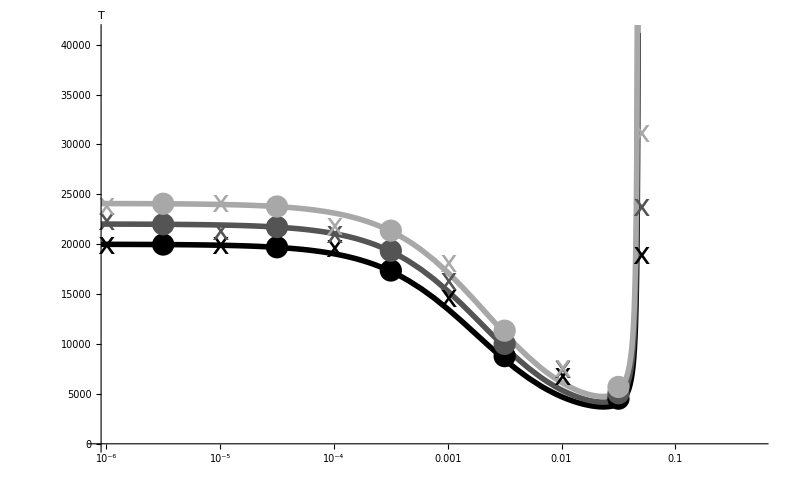

```mathematica
w[2]=1-10^-3;
w[3]=w[2];
w[4]=1+1/20;
n=10^6;
k1=10^-4;
k2=0;
k3=-10^-4;
μ=5*10^-7;
xmin=0.9*10^-6;
xmax=0.5;
ymin=0;
ymax=Automatic;

(*Legended[*)
Show[

(*MSB solutions*)
LogLinearPlot[MSBSk/.N->n/.k->k1,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0],Thickness[0.005]}],
LogLinearPlot[MSBSk/.N->n/.k->k2,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0.33],Thickness[0.005]}],
LogLinearPlot[MSBSk/.N->n/.k->k3,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0.66],Thickness[0.005]}],

(*full semi-deterministic solutions*)
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k1/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0],PointSize[.02]}],
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k2/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0.33],PointSize[.02]}],
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k3/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0.66],PointSize[.02]}],

(*simulation results*)
ListLogLinearPlot[
{{10^-6,KillTimeDeepGreen0},
{10^-5,KillTimeDeepGreeni},
{10^-4,KillTimeDeepGreenii},
{10^-3,KillTimeDeepGreeniii},
{10^-2,KillTimeDeepGreeniv},
{0.05,KillTimeDeepGreenv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0]}],

ListLogLinearPlot[
{{10^-6,KillTimeDeepBlack0},
{10^-5,KillTimeDeepBlacki},
{10^-4,KillTimeDeepBlackii},
{10^-3,KillTimeDeepBlackiii},
{10^-2,KillTimeDeepBlackiv},
{0.05,KillTimeDeepBlackv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.33]}],

ListLogLinearPlot[
{{10^-6,KillTimeDeepBlue0},
{10^-5,KillTimeDeepBluei},
{10^-4,KillTimeDeepBlueii},
{10^-3,KillTimeDeepBlueiii},
{10^-2,KillTimeDeepBlueiv},
{0.05,KillTimeDeepBluev}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.66]}],

AxesLabel->{(*Style["r",AxisSize]*)"",Style["T",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->{{TickSize,FontOpacity->0},{TickSize}},
PlotRangePadding->None
](*,
Placed[
LineLegend[
{Directive[Thickness[0.25],Darker[Red]],Directive[Thickness[0.25],Black],Directive[Thickness[0.25],Darker[Green]]},Table[Style[StringForm["k = ``",i],24],{i,{k3,k1,k2}}],
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.25,0.25}
]
]*)

Export[dir<>"TimeFixDriveRMSBSimsBW.eps",%];

Clear[n,w,r,μ,k1,k2,k3,xmin,xmax,ymin,ymax]
```

Recombination is stronger than mutation, transmission bias, and viability selection in favour of the double mutant, r > s, when

```mathematica
Solve[sDMrare==0/.Killer,r]//FullSimplify
```

{{r→1-1/((1+k+μ^2-k μ^2) w[4])}}

In this case we have

```mathematica
Solve[sDMrare==0/.Killer,r]/.μ->5*10^-7/.w[4]->1+1/20/.k->0//N
```

{{r→0.047619}}

Weissman et al 2010 eqn B21 with deleterious single mutants gives  (assumes r >> s and δ >> (μ s)^(1/2))

```mathematica
δ/(2N μ^2 s)/.s->1/20/.N->10^6/.μ->5*10^-7/.δ->10^-3//N
```

40000.

#### Simulations for Figure 1 (bottom)

Simulation function

```mathematica
w[1]=1; (*A1B1 viability*)
w[2]=1-10^-5; (*A2B1 viability*)
w[3]=w[2]; (*A1B2 viability*)
w[4]=1+1/20;(*A2B2 viability*)
NUM=10^6; (*pop size*)
MAXgen=10NUM; (*a cut off time limit that avoids running an infinite loop while testing (increase if triggered)*)
NUMtrials=10^3; (*number of trials to average crossing time over*)
μ=5*10^-7; (*mutation probability*)

runKillTimeShallow[r_,k_,seednum_]:=runKillTimeShallow[r,k,seednum]= 
Block[{fixed=0,lost=0},
SeedRandom[seednum];
For[trial=1,trial≤NUMtrials,trial++,
gen=0; 
vec={1,0,0,0}; 
finished=False;

While[finished==False,

gen++;
x1:=vec[[1]];
x2:=vec[[2]];
x3:=vec[[3]];
x4:=vec[[4]];
newx1=((1-k) x1 x2 (1-μ)+(1-k) x1 x3 (1-μ)+x1^2 (1-μ)^2+(1-k) r x2 x3 (1-μ)^2+(1-k) (1-r) x1 x4 (1-μ)^2) w[1];
newx2:=((1+k) x1 x2 (1-μ)+x2^2 (1-μ)+x2 x4 (1-μ)+(1-k) x1 x3 μ+x1^2 (1-μ) μ+2 x1 x4 (r/2+1/2 (1-k) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+1/2 (1-k) r (1-μ) μ)) w[2];
newx3:=((1+k) x1 x3 (1-μ)+x3^2 (1-μ)+x3 x4 (1-μ)+(1-k) x1 x2 μ+x1^2 (1-μ) μ+2 x1 x4 (r/2+1/2 (1-k) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+1/2 (1-k) r (1-μ) μ)) w[3];
newx4:=(x4^2+(1+k) x1 x2 μ+x2^2 μ+(1+k) x1 x3 μ+x3^2 μ+x1^2 μ^2+x2 x4 (1+μ)+x3 x4 (1+μ)+2 x1 x4 (1/2 (1+k) (1-r)+1/2 (1-k) (1-r) μ^2)+2 x2 x3 ((1-r) μ+r ((1+k)/2+1/2 (1-k) μ^2))) w[4];

total:=newx1+newx2+newx3+newx4;

newvec:={newx1,newx2,newx3,newx4}/total;

num=RandomInteger[MultinomialDistribution[NUM,newvec]];

vec=num/NUM;

If[num[[4]]==NUM,finished=True; time[trial]=gen]; (*end if A2B2 fixed*)
If[gen==MAXgen,finished=True;Print["Warning: ended prematurely; increase MAXgen."]];
]
];
Table[time[i],{i,1,NUMtrials}]
]
```

Simulations, giving mean crossing times. Can take a long time to run. Results pasted below to skip re-running.

```mathematica
(*Drive against mutants*)
(*KillTimeShallowBlue0=Mean[runKillTimeShallow[10^-6,-10^-4,9012]]//N
KillTimeShallowBluei=Mean[runKillTimeShallow[10^-5,-10^-4,4182]]//N
KillTimeShallowBlueii=Mean[runKillTimeShallow[10^-4,-10^-4,455]]//N
KillTimeShallowBlueiii=Mean[runKillTimeShallow[10^-3,-10^-4,3346]]//N
KillTimeShallowBlueiv=Mean[runKillTimeShallow[10^-2,-10^-4,4972]]//N
KillTimeShallowBluev=Mean[runKillTimeShallow[10^-1,-10^-4,5342]]//N*)
```

```mathematica
(*No drive*)
(*KillTimeShallowBlack0=Mean[runKillTimeShallow[10^-6,0,4312]]//N
KillTimeShallowBlacki=Mean[runKillTimeShallow[10^-5,0,4112]]//N
KillTimeShallowBlackii=Mean[runKillTimeShallow[10^-4,0,452]]//N
KillTimeShallowBlackiii=Mean[runKillTimeShallow[10^-3,0,146]]//N
KillTimeShallowBlackiv=Mean[runKillTimeShallow[10^-2,0,4482]]//N
KillTimeShallowBlackv=Mean[runKillTimeShallow[10^-1,0,5342]]//N*)
```

```mathematica
(*Drive for mutants*)
(*KillTimeShallowGreen0=Mean[runKillTimeShallow[10^-6,10^-4,90647]]//N
KillTimeShallowGreeni=Mean[runKillTimeShallow[10^-5,10^-4,425742]]//N
KillTimeShallowGreenii=Mean[runKillTimeShallow[10^-4,10^-4,41455]]//N
KillTimeShallowGreeniii=Mean[runKillTimeShallow[10^-3,10^-4,3685]]//N
KillTimeShallowGreeniv=Mean[runKillTimeShallow[10^-2,10^-4,8563]]//N
KillTimeShallowGreenv=Mean[runKillTimeShallow[10^-1,10^-4,52472]]//N*)
```

Simulation results

```mathematica
(*Drive against mutants*)
KillTimeShallowBlue0=7709.787;
KillTimeShallowBluei=7905.978;
KillTimeShallowBlueii=7276.521;
KillTimeShallowBlueiii=5525.68;
KillTimeShallowBlueiv=3836.432;
KillTimeShallowBluev=12412.026;
```

```mathematica
(*No drive*)
KillTimeShallowBlack0=7135.574;
KillTimeShallowBlacki=6955.095;
KillTimeShallowBlackii=6548.824;
KillTimeShallowBlackiii=5113.258;
KillTimeShallowBlackiv=3500.537;
KillTimeShallowBlackv=9854.066;
```

```mathematica
(*Drive for mutants*)
KillTimeShallowGreen0=6070.209;
KillTimeShallowGreeni=6180.917;
KillTimeShallowGreenii=5883.407;
KillTimeShallowGreeniii=4771.133;
KillTimeShallowGreeniv=3231.519;
KillTimeShallowGreenv=8411.995;
```

```mathematica
Clear[w,NUM,MAXgen,NUMtrials,μ,x1,x2,x3,x4]
```

#### Figure 1 (bottom)

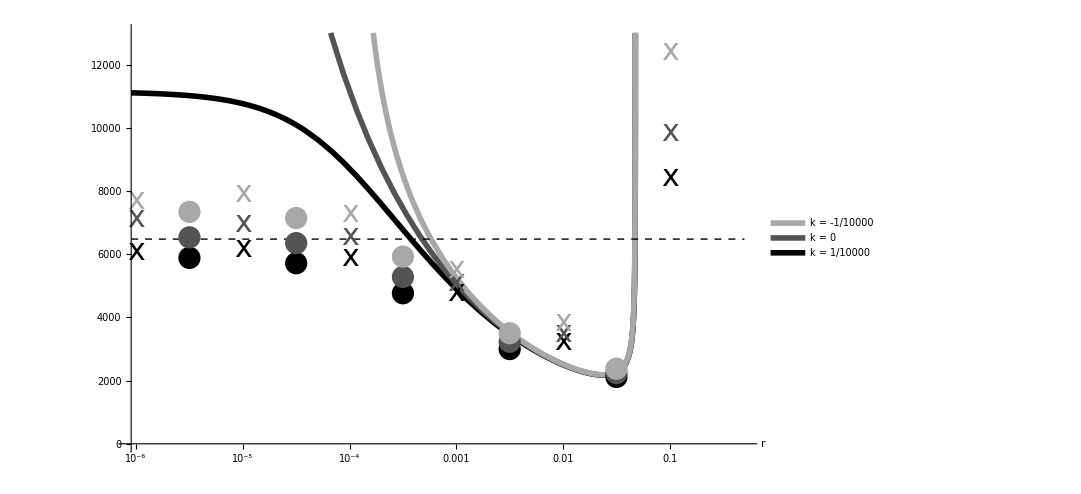

```mathematica
n=10^6;
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1/20;
k1=10^-4;
k2=0;
k3=-10^-4;
μ=5*10^-7;
xmin=0.9*10^-6;
xmax=0.5;
ymin=0;
ymax=1.3*10^4;

Legended[
Show[

(*cross by recmobination, semi-deterministic*)
LogLinearPlot[TDetRSk/.N->n/.k->k1,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0],Thickness[0.005]}],
LogLinearPlot[TDetRSk/.N->n/.k->k2,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0.33],Thickness[0.005]}],
LogLinearPlot[TDetRSk/.N->n/.k->k3,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0.66],Thickness[0.005]}],

(*cross by mutation, semi-deterministic*)
LogLinearPlot[TDetMutSk/.N->n/.k->k1,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{Black,Thick,Dashed}],

(*full semi-deterministic solutions*)
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k1/.μ->μtemp/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0],PointSize[.02]}],
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k2/.μ->μtemp/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0.33],PointSize[.02]}],
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k3/.μ->μtemp/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0.66],PointSize[.02]}],

(*simulation results*)
ListLogLinearPlot[
{{10^-6,KillTimeShallowGreen0},
{10^-5,KillTimeShallowGreeni},
{10^-4,KillTimeShallowGreenii},
{10^-3,KillTimeShallowGreeniii},
{10^-2,KillTimeShallowGreeniv},
{10^-1,KillTimeShallowGreenv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0]}],

ListLogLinearPlot[
{{10^-6,KillTimeShallowBlack0},
{10^-5,KillTimeShallowBlacki},
{10^-4,KillTimeShallowBlackii},
{10^-3,KillTimeShallowBlackiii},
{10^-2,KillTimeShallowBlackiv},
{10^-1,KillTimeShallowBlackv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.33]}],

ListLogLinearPlot[
{{10^-6,KillTimeShallowBlue0},
{10^-5,KillTimeShallowBluei},
{10^-4,KillTimeShallowBlueii},
{10^-3,KillTimeShallowBlueiii},
{10^-2,KillTimeShallowBlueiv},
{10^-1,KillTimeShallowBluev}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.66]}],

AxesLabel->{Style["r",AxisSize],(*Style["T",AxisSize]*)""},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],
Placed[
LineLegend[
{Directive[Thickness[0.25],GrayLevel[0.66]],Directive[Thickness[0.25],GrayLevel[0.33]],Directive[Thickness[0.25],GrayLevel[0]]},Table[Style[StringForm["k = ``",i],24],{i,{k3,k2,k1}}],
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.2,0.2}
]
]

Export[dir<>"TimeFixDriveRSimsBW.eps",%];

Clear[n,w,r,μ,k1,k2,k3,xmin,xmax,ymin,ymax]
```

Recombination is stronger than mutation, transmission bias, and viability selection in favour of the double mutant, r > s, when

```mathematica
Solve[sDMrare==0/.Killer,r]//FullSimplify
```

{{r→1-1/((1+k+μ^2-k μ^2) w[4])}}

In this case we have

```mathematica
Solve[sDMrare==0/.Killer,r]/.μ->5*10^-7/.w[4]->1+1/20/.k->0//N
```

{{r→0.047619}}

Lynch 2010 eqn 8a (assumes r > s and δ = 0)

```mathematica
2/μ (μ/s)^(1/2)/.μ->5*10^-7/.s->1/20//N
```

12649.1

Weissman et al 2010 eqn B21 with neutral single mutants gives (assumes r >> s, δ << (μ (s))^(1/2), and N μ << 1)

```mathematica
1/(2N Sqrt[μ^3 s])/.s->1/20/.N->10^6/.μ->5*10^-7//N
```

6324.56

#### Simulations for Figure 2 (top)

Simulation function

```mathematica
w[1]=1; (*A1B1 viability*)
w[2]=1-10^-5; (*A2B1 viability*)
w[3]=w[2]; (*A1B2 viability*)
w[4]=1+1/20;(*A2B2 viability*)
NUM=10^6; (*pop size*)
MAXgen=10NUM; (*a cut off time limit that avoids running an infinite loop while testing (increase if triggered)*)
NUMtrials=10^3; (*number of trials; must be more than inverse of probability*)
i0=1000; (*initial number of A2B1*)
j0=i0; (*initial number of A1B2*)
r=0; (*recombination probability*)

runKillProbMut[μ_,k_,seednum_]:=runKillProbMut[μ,k,seednum]=
Block[{fixed=0,lost=0},
SeedRandom[seednum];
For[trial=1,trial≤NUMtrials,trial++,
gen=0; 
vec={1-(i0+j0)/NUM,i0/NUM,j0/NUM,0};
finished=False;

While[finished==False,

gen++;
x1:=vec[[1]];
x2:=vec[[2]];
x3:=vec[[3]];
x4:=vec[[4]];
newx1:=(x1^2+(1-k) x1 x2 (1-μ)^2+(1-k) x1 x3 (1-μ)^2+(1-k) r x2 x3 (1-μ)^2+(1-k) (1-r) x1 x4 (1-μ)^2) w[1];
newx2:=(x2^2 (1-μ)+x2 x4 (1-μ)+(1-k) x1 x3 (1-μ) μ+2 x1 x2 (1/2 (1+k) (1-μ)+1/2 (1-k) (1-μ) μ)+2 x1 x4 (r/2+1/2 (1-k) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+1/2 (1-k) r (1-μ) μ)) w[2];
newx3:=(x3^2 (1-μ)+x3 x4 (1-μ)+(1-k) x1 x2 (1-μ) μ+2 x1 x3 (1/2 (1+k) (1-μ)+1/2 (1-k) (1-μ) μ)+2 x1 x4 (r/2+1/2 (1-k) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+1/2 (1-k) r (1-μ) μ)) w[3];
newx4:=(x4^2+x2^2 μ+x3^2 μ+x2 x4 (1+μ)+x3 x4 (1+μ)+2 x1 x2 (1/2 (1+k) μ+1/2 (1-k) μ^2)+2 x1 x3 (1/2 (1+k) μ+1/2 (1-k) μ^2)+2 x1 x4 (1/2 (1+k) (1-r)+1/2 (1-k) (1-r) μ^2)+2 x2 x3 ((1-r) μ+r ((1+k)/2+1/2 (1-k) μ^2))) w[4];

total:=newx1+newx2+newx3+newx4;

newvec:={newx1,newx2,newx3,newx4}/total;

num=RandomInteger[MultinomialDistribution[NUM,newvec]];

vec=num/NUM;

If[num[[4]]==NUM,finished=True; fixed=fixed+1];
If[(num[[2]]+num[[3]]+num[[4]]==0),finished=True; lost=lost+1];
If[gen==MAXgen,finished=True;Print["Warning: ended prematurely; increase MAXgen."]];
]
];
{lost,fixed}
]
```

Simulations giving crossing probabilities. Can take a long time to run. Results pasted below to skip re-running.

```mathematica
(*Drive against mutants*)
(*KillProbMutBluei=runKillProbMut[10^-8,-10^-4,17964][[2]]/NUMtrials//N
KillProbMutBlueii=runKillProbMut[10^-7,-10^-4,5492][[2]]/NUMtrials//N
KillProbMutBlueiii=runKillProbMut[10^-6,-10^-4,76428][[2]]/NUMtrials//N
KillProbMutBlueiv=runKillProbMut[10^-5,-10^-4,4797][[2]]/NUMtrials//N*)
```

```mathematica
(*No drive*)
(*KillProbMutBlacki=runKillProbMut[10^-8,0,236426][[2]]/NUMtrials//N
KillProbMutBlackii=runKillProbMut[10^-7,0,838675][[2]]/NUMtrials//N
KillProbMutBlackiii=runKillProbMut[10^-6,0,462387][[2]]/NUMtrials//N
KillProbMutBlackiv=runKillProbMut[10^-5,0,57487][[2]]/NUMtrials//N*)
```

```mathematica
(*Drive for mutants*)
(*KillProbMutGreeni=runKillProbMut[10^-8,10^-4,77773972][[2]]/NUMtrials//N
KillProbMutGreenii=runKillProbMut[10^-7,10^-4,7935676][[2]]/NUMtrials//N
KillProbMutGreeniii=runKillProbMut[10^-6,10^-4,436456][[2]]/NUMtrials//N
KillProbMutGreeniv=runKillProbMut[10^-5,10^-4,6873][[2]]/NUMtrials//N*)
```

Simulation results

```mathematica
(*Drive against mutants*)
KillProbMutBluei=0.016;
KillProbMutBlueii=0.161;
KillProbMutBlueiii=0.514;
KillProbMutBlueiv=0.919;
```

```mathematica
(*No drive*)
KillProbMutBlacki=0.059;
KillProbMutBlackii=0.235;
KillProbMutBlackiii=0.563;
KillProbMutBlackiv=0.951;
```

```mathematica
(*Drive for mutants*)
KillProbMutGreeni=0.299;
KillProbMutGreenii=0.393;
KillProbMutGreeniii=0.660;
KillProbMutGreeniv=0.947;
```

```mathematica
Clear[w,NUM,MAXgen,NUMtrials,i0,j0,r,x1,x2,x3,x4]
```

#### Figure 2 (top)

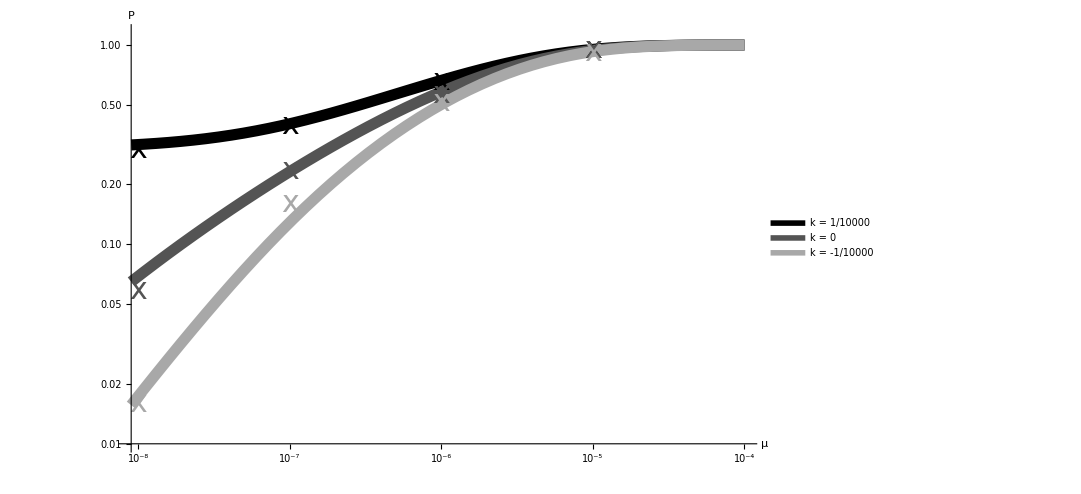

```mathematica
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1/20;
n=10^6;
i0=1000;
j0=i0;
n0=i0+j0;
k1=10^-4;
k2=0;
k3=-10^-4;
xmin=0.9*10^-8;
xmax=10^-4;
ymin=10^-2;
ymax=1.15;

Legended[
Show[
(*stochastic crossing probability by mutation*)
LogLogPlot[PStochMutSk/.N->n/.k->k1,{μ,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0]},PlotRange->{ymin,ymax}],
LogLogPlot[PStochMutSk/.N->n/.k->k2,{μ,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0.33]}],
LogLogPlot[PStochMutSk/.N->n/.k->k3,{μ,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0.66]}],

(*simulation results*)
ListLogLogPlot[
{{10^-8,KillProbMutGreeni},
{10^-7,KillProbMutGreenii},
{10^-6,KillProbMutGreeniii},
{10^-5,KillProbMutGreeniv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0]}
],

ListLogLogPlot[
{{10^-8,KillProbMutBlacki},
{10^-7,KillProbMutBlackii},
{10^-6,KillProbMutBlackiii},
{10^-5,KillProbMutBlackiv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.33]}
],

ListLogLogPlot[
{{10^-8,KillProbMutBluei},
{10^-7,KillProbMutBlueii},
{10^-6,KillProbMutBlueiii},
{10^-5,KillProbMutBlueiv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.66]}
],

AxesLabel->{Style["μ",AxisSize],Style["P",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],
Placed[
LineLegend[
{Directive[Thickness[0.25],GrayLevel[0]],Directive[Thickness[0.25],GrayLevel[0.33]],Directive[Thickness[0.25],GrayLevel[0.66]]},Table[Style[StringForm["k = ``",i],24],{i,{k1,k2,k3}}],
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.8,0.3}
]
]

Export[dir<>"ProbFixDriveMutSimsBW.eps",%];

Clear[n0,i0,j0,w,n,k1,k2,k3,xmin,xmax,ymin,ymax]
```

#### Simulations for Figure 2 (bottom)

Simulation function

```mathematica
w[1]=1;(*A1B1 viability*)
w[2]=1-10^-5; (*A2B1 viability*)
w[3]=w[2]; (*A1B2 viability*)
w[4]=1+1/20;(*A2B2 viability*)
NUM=10^6; (*pop size*)
MAXgen=10NUM; (*a cut off time limit that avoids running an infinite loop while testing (increase if triggered)*)
NUMtrials=10^3; (*number of trials; must be more than inverse of probability*)
i0=1000; (*initial number of A2B1*)
j0=i0; (*initial number of A1B2*)
μ=0; (*mutation probability*)

runKillProbRec[r_,k_,seednum_]:=runKillProbRec[r,k,seednum]=
Block[{fixed=0,lost=0},
SeedRandom[seednum];
For[trial=1,trial≤NUMtrials,trial++,
gen=0; 
vec={1-(i0+j0)/NUM,i0/NUM,j0/NUM,0};
finished=False;

While[finished==False,

gen++;
x1:=vec[[1]];
x2:=vec[[2]];
x3:=vec[[3]];
x4:=vec[[4]];
newx1:=(x1^2+(1-k) x1 x2 (1-μ)^2+(1-k) x1 x3 (1-μ)^2+(1-k) r x2 x3 (1-μ)^2+(1-k) (1-r) x1 x4 (1-μ)^2) w[1];
newx2:=(x2^2 (1-μ)+x2 x4 (1-μ)+(1-k) x1 x3 (1-μ) μ+2 x1 x2 (1/2 (1+k) (1-μ)+1/2 (1-k) (1-μ) μ)+2 x1 x4 (r/2+1/2 (1-k) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+1/2 (1-k) r (1-μ) μ)) w[2];
newx3:=(x3^2 (1-μ)+x3 x4 (1-μ)+(1-k) x1 x2 (1-μ) μ+2 x1 x3 (1/2 (1+k) (1-μ)+1/2 (1-k) (1-μ) μ)+2 x1 x4 (r/2+1/2 (1-k) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+1/2 (1-k) r (1-μ) μ)) w[3];
newx4:=(x4^2+x2^2 μ+x3^2 μ+x2 x4 (1+μ)+x3 x4 (1+μ)+2 x1 x2 (1/2 (1+k) μ+1/2 (1-k) μ^2)+2 x1 x3 (1/2 (1+k) μ+1/2 (1-k) μ^2)+2 x1 x4 (1/2 (1+k) (1-r)+1/2 (1-k) (1-r) μ^2)+2 x2 x3 ((1-r) μ+r ((1+k)/2+1/2 (1-k) μ^2))) w[4];

total:=newx1+newx2+newx3+newx4;

newvec:={newx1,newx2,newx3,newx4}/total;

num=RandomInteger[MultinomialDistribution[NUM,newvec]];

vec=num/NUM;

If[num[[4]]==NUM,finished=True; fixed=fixed+1];
If[(num[[2]]+num[[4]]==0)||(num[[3]]+num[[4]]==0),finished=True; lost=lost+1];
If[gen==MAXgen,finished=True;Print["Warning: ended prematurely; increase MAXgen."]];
]
];
{lost,fixed}
]
```

Simulations giving crossing probabilities. Can take a long time to run. Results pasted below to skip re-running.

```mathematica
(*Drive against mutants*)
(*KillProbRecBluei=runKillProbRec[10^-5,-10^-4,656481][[2]]/NUMtrials//N
KillProbRecBlueii=runKillProbRec[10^-4,-10^-4,546692][[2]]/NUMtrials//N
KillProbRecBlueiii=runKillProbRec[10^-3,-10^-4,774048][[2]]/NUMtrials//N
KillProbRecBlueiv=runKillProbRec[10^-2,-10^-4,4537][[2]]/NUMtrials//N
KillProbRecBluev=runKillProbRec[10^-1,-10^-4,4586637][[2]]/NUMtrials//N*)
```

```mathematica
(*No drive*)
(*KillProbRecBlacki=runKillProbRec[10^-5,0,98561][[2]]/NUMtrials//N
KillProbRecBlackii=runKillProbRec[10^-4,0,34553][[2]]/NUMtrials//N
KillProbRecBlackiii=runKillProbRec[10^-3,0,27356][[2]]/NUMtrials//N
KillProbRecBlackiv=runKillProbRec[10^-2,0,7956][[2]]/NUMtrials//N
KillProbRecBlackv=runKillProbRec[10^-1,0,936236][[2]]/NUMtrials//N*)
```

```mathematica
(*Drive for mutants*)
(*KillProbRecGreeni=runKillProbRec[10^-5,10^-4,245378][[2]]/NUMtrials//N
KillProbRecGreenii=runKillProbRec[10^-4,10^-4,275][[2]]/NUMtrials//N
KillProbRecGreeniii=runKillProbRec[10^-3,10^-4,295798][[2]]/NUMtrials//N
KillProbRecGreeniv=runKillProbRec[10^-2,10^-4,825446][[2]]/NUMtrials//N
KillProbRecGreenv=runKillProbRec[10^-1,10^-4,8549736][[2]]/NUMtrials//N*)
```

Simulation results

```mathematica
(*Drive against mutants*)
KillProbRecBluei=0.004;
KillProbRecBlueii=0.032;
KillProbRecBlueiii=0.168;
KillProbRecBlueiv=0.534;
KillProbRecBluev=0.102;
```

```mathematica
(*No drive*)
KillProbRecBlacki=0.014;
KillProbRecBlackii=0.056;
KillProbRecBlackiii=0.209;
KillProbRecBlackiv=0.598;
KillProbRecBlackv=0.157;
```

```mathematica
(*Drive for mutants*)
KillProbRecGreeni=0.045;
KillProbRecGreenii=0.094;
KillProbRecGreeniii=0.256;
KillProbRecGreeniv=0.639;
KillProbRecGreenv=0.261;
```

```mathematica
Clear[w,NUM,MAXgen,NUMtrials,i0,j0,μ,x1,x2,x3,x4]
```

#### Figure 2 (bottom)

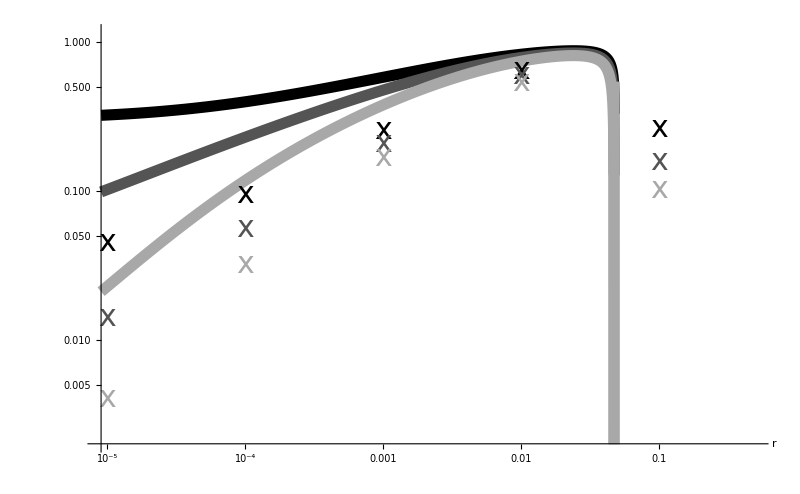

```mathematica
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1/20;
i0=1000;
n=10^6;
k1=10^-4;
k2=0;
k3=-10^-4;
c=1;
xmin=0.9*10^-5;
xmax=1/20;
ymin=2*10^-3;
ymax=1.15;
μ=5*10^-7;

Show[

(*stochastic crossing probability by recombination*)
LogLogPlot[PStochRSk/.N->n/.k->k1,{r,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0]},PlotRange->{{xmin,0.5},{ymin,ymax}}],
LogLogPlot[PStochRSk/.N->n/.k->k2,{r,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0.33]}],
LogLogPlot[PStochRSk/.N->n/.k->k3,{r,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0.66]}],

(*simulations*)
ListLogLogPlot[
{{10^-5,KillProbRecGreeni},
{10^-4,KillProbRecGreenii},
{10^-3,KillProbRecGreeniii},
{10^-2,KillProbRecGreeniv},
{10^-1,KillProbRecGreenv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0]}],

ListLogLogPlot[
{{10^-5,KillProbRecBlacki},
{10^-4,KillProbRecBlackii},
{10^-3,KillProbRecBlackiii},
{10^-2,KillProbRecBlackiv},
{10^-1,KillProbRecBlackv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.33]}],

ListLogLogPlot[
{{10^-5,KillProbRecBluei},
{10^-4,KillProbRecBlueii},
{10^-3,KillProbRecBlueiii},
{10^-2,KillProbRecBlueiv},
{10^-1,KillProbRecBluev}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.66]}],

AxesLabel->{Style["r",AxisSize],Style["",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize
]

Export[dir<>"ProbFixDriveRSimsBW.eps",%];

Clear[i0,j0,c,w,n,k1,k2,k3,μ,xmin,xmax,ymin,ymax]
```

### 2. Cytonuclear inheritance

#### Transition probabilities, analytic solutions, recursions

When one trait is inherited uniparentally (e.g., a cytoplasmic element such as a mitochondrial gene) and the other biparentally (e.g., nuclear gene) we can only use the results with recombination, as genes in the nucleus and cytoplasm are unlinked (r = 1 / 2). Let A be the nuclear gene, with mutation probability μ, and B the cytoplasmic element, with mutation probability ν. Then the transmission probabilities are

```mathematica
CN={
b[1,1,1]->(1-μ)(1-ν),
b[1,1,2]->μ(1-ν),
b[1,1,3]->ν(1-μ),
b[1,1,4]->μ ν,
b[1,2,1]->(1-μ)/2(1-ν),b[2,1,1]->(1-μ)/2(1-ν),
b[1,2,2]->(1+μ)/2(1-ν),b[2,1,2]->(1+μ)/2(1-ν),
b[1,2,3]->(1-μ)/2ν,b[2,1,3]->(1-μ)/2ν,
b[1,2,4]->(1+μ)/2ν,b[2,1,4]->(1+μ)/2ν,
b[1,3,1]->(1-μ)(1-ν),b[3,1,1]->0,
b[1,3,2]->μ(1-ν),b[3,1,2]->0,
b[1,3,3]->(1-μ)ν,b[3,1,3]->1-μ,
b[1,3,4]->μ ν,b[3,1,4]->μ,
b[1,4,1]->(1-μ)/2(1-ν),b[4,1,1]->0,
b[1,4,2]->(1+μ)/2(1-ν),b[4,1,2]->0,
b[1,4,3]->(1-μ)/2ν,b[4,1,3]->(1-μ)/2,
b[1,4,4]->(1+μ)/2ν,b[4,1,4]->(1+μ)/2,
b[2,2,1]->0,
b[2,2,2]->1-ν,
b[2,2,3]->0,
b[2,2,4]->ν,
b[2,3,1]->(1-μ)/2(1-ν),b[3,2,1]->0,
b[2,3,2]->(1+μ)/2(1-ν),b[3,2,2]->0,
b[2,3,3]->(1-μ)/2ν,b[3,2,3]->(1-μ)/2,
b[2,3,4]->(1+μ)/2ν,b[3,2,4]->(1+μ)/2,
b[2,4,1]->0,b[4,2,1]->0,
b[2,4,2]->1-ν,b[4,2,2]->0,
b[2,4,3]->0,b[4,2,3]->0,
b[2,4,4]->ν,b[4,2,4]->1,
b[3,3,1]->0,
b[3,3,2]->0,
b[3,3,3]->1-μ,
b[3,3,4]->μ,
b[3,4,1]->0,b[4,3,1]->0,
b[3,4,2]->0,b[4,3,2]->0,
b[3,4,3]->(1-μ)/2,b[4,3,3]->(1-μ)/2,
b[3,4,4]->(1+μ)/2,b[4,3,4]->(1+μ)/2,
b[4,4,1]->0,
b[4,4,2]->0,
b[4,4,3]->0,
b[4,4,4]->1
};
```

The analytic and numerical crossing times are (holding total mutation probabilities constant)

```mathematica
TDetRCN=TDetR/.CN/.ν->c μ/.μ->U/(1+c);
SumCN=x4pDMSum/.CN/.ν->c μ/.μ->U/(1+c);
TMSBCN=TDetMutSel/.CN/.ν->c μ/.μ->U/(1+c);
TStochRCN=TStochR/.CN/.ν->c μ/.μ->U/(1+c);
```

where U is total mutation probability and c is the ratio of mutation probabilities in A and B (ν = c μ).

The general recursion equations are

```mathematica
eqn[k_] := Simplify[w[k] Sum[x[i] x[j] b[i, j, k], {i, 1, 4}, {j, 1, 4}]]
```

The recursion equations are

```mathematica
eqn[1]/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[2]/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[3]/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[4]/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
```

and holding total mutation probability constant we have

```mathematica
eqn[1]/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ/.μ->U/(1+c);
eqn[2]/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ/.μ->U/(1+c);
eqn[3]/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ/.μ->U/(1+c);
eqn[4]/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ/.μ->U/(1+c);
```

The analytic crossing probability is

```mathematica
PStochRCN=PStochR/.CN;
```

Not allowing mutations in resident-residents matings gives

```mathematica
eqn[1]/.b[1,1,1]->1/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ;
eqn[2]/.b[1,1,2]->0/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ;
eqn[3]/.b[1,1,3]->0/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ;
eqn[4]/.b[1,1,4]->0/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ;
```

and holding total mutation probability constant we have

```mathematica
eqn[1]/.b[1,1,1]->1/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ/.μ->U/(1+c);
eqn[2]/.b[1,1,2]->0/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ/.μ->U/(1+c);
eqn[3]/.b[1,1,3]->0/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ/.μ->U/(1+c);
eqn[4]/.b[1,1,4]->0/.CN/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4/.ν->c μ/.μ->U/(1+c);
```

#### Simulations for Figure 3 (top)

Simulation function

```mathematica
w[1]=1; (*A1B1 viability*)
w[2]=1-10^-5; (*A2B1 viability*)
w[3]=w[2]; (*A1B2 viability*)
w[4]=1+1.01;(*A2B2 viability*)
NUM=10^6; (*pop size*)
MAXgen=10NUM; (*a cut off time limit that avoids running an infinite loop while testing (increase if triggered)*)
NUMtrials=10^2; (*number of trials*)
μ=5*10^-7; (*total mutation probability*)

runCytoNu[ν_,seednum_]:=runCytoNu[ν,seednum]=
Block[{fixed=0,lost=0},
SeedRandom[seednum];
For[trial=1,trial≤NUMtrials,trial++,
gen=0; 
vec={1,0,0,0};
finished=False;

While[finished==False,

gen++;
x1:=vec[[1]];
x2:=vec[[2]];
x3:=vec[[3]];
x4:=vec[[4]];
newx1:=(x1^2 (1-μ) (1-ν)+x1 x2 (1-μ) (1-ν)+x1 x3 (1-μ) (1-ν)+1/2 x2 x3 (1-μ) (1-ν)+1/2 x1 x4 (1-μ) (1-ν)) w[1];
newx2:=(x2^2 (1-ν)+x2 x4 (1-ν)+x1^2 μ (1-ν)+x1 x3 μ (1-ν)+x1 x2 (1+μ) (1-ν)+1/2 x2 x3 (1+μ) (1-ν)+1/2 x1 x4 (1+μ) (1-ν)) w[2];
newx3:=(x1 x3 (1-μ)+1/2 x2 x3 (1-μ)+x3^2 (1-μ)+1/2 x1 x4 (1-μ)+x3 x4 (1-μ)+x1^2 (1-μ) ν+x1 x2 (1-μ) ν+x1 x3 (1-μ) ν+1/2 x2 x3 (1-μ) ν+1/2 x1 x4 (1-μ) ν) w[3];
newx4:=(x2 x4+x4^2+x1 x3 μ+x3^2 μ+1/2 x2 x3 (1+μ)+1/2 x1 x4 (1+μ)+x3 x4 (1+μ)+x2^2 ν+x2 x4 ν+x1^2 μ ν+x1 x3 μ ν+x1 x2 (1+μ) ν+1/2 x2 x3 (1+μ) ν+1/2 x1 x4 (1+μ) ν) w[4];

total:=newx1+newx2+newx3+newx4;

newvec:={newx1,newx2,newx3,newx4}/total;

num=RandomInteger[MultinomialDistribution[NUM,newvec]];

vec=num/NUM;

If[num[[4]]==NUM,finished=True; time[trial]=gen];
If[gen==MAXgen,finished=True;Print["Warning: ended prematurely; increase MAXgen."]];
]
];
Table[time[i],{i,1,NUMtrials}]
]
```

Simulations giving mean crossing times. Can take a long time to run. Results pasted below to skip re-running.

```mathematica
(*CytoNuv0=Mean[runCytoNu[10^-10,94376796]]//N
CytoNui=Mean[runCytoNu[10^-9,59657463]]//N
CytoNuii=Mean[runCytoNu[10^-8,946916]]//N
CytoNuiii=Mean[runCytoNu[10^-7,434765]]//N
CytoNuiv=Mean[runCytoNu[10^-6,599243]]//N
CytoNuv=Mean[runCytoNu[10^-5,98796]]//N
CytoNuvi=Mean[runCytoNu[10^-4,599723]]//N
CytoNuvii=Mean[runCytoNu[10^-3,987916]]//N
CytoNuviii=Mean[runCytoNu[10^-2,9873916]]//N*)
```

Simulation results

```mathematica
CytoNu0=112718.2;
CytoNui=25663.18;
CytoNuii=6348.64;
CytoNuiii=1546.63;
CytoNuiv=658.41;
CytoNuv=350.4;
CytoNuvi=192.04;
CytoNuvii=108.93;
CytoNuviii=66.81;
```

```mathematica
Clear[w,NUM,NUMtrials,MAXgen,μ,x1,x2,x3,x4]
```

#### Figure 3 (top)

FindRoot::precw: The precision of the argument function (-1.25329×10^32\ (119997480014429987400003\ (-1 + 199998099999\ Plus[« 2 »]/200000000000)^4/400000000000000000000000000000000000000000000000000000 + « 74 » + « 426 ») == 1/1000000) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (-1.25329×10^32\ (119997480014429987400003\ (-1 + 199998099999\ Plus[« 2 »]/200000000000)^4/4000000000000000000000000000000000000000000000000000 + « 74 » + « 426 ») == 1/1000000) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (-1.25329×10^32\ (119997480014429987400003\ (-1 + 199998099999\ Plus[« 2 »]/200000000000)^4/40000000000000000000000000000000000000000000000000 + « 74 » + « 426 ») == 1/1000000) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

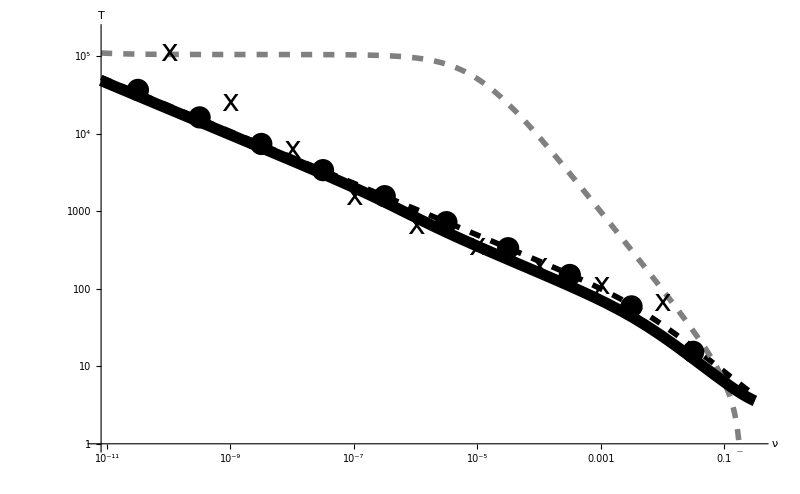

```mathematica
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1.01; 
n=10^6;
μ=5*10^-7;
xmin=0.8*10^-11;
xmax=10^(-1/2);

(*Legended[*)
Show[

(*semi-deterministic equation with recombination and selection*)
LogLogPlot[TDetR/.CN/.N->n,{ν,xmin,xmax},PlotStyle->{Black,Thickness[0.005],Dashing[0.01]},PlotRange->{{xmin,xmax},{1,2*10^5}}],

(*semi-deterministic equation with MSB*)
LogLogPlot[TDetMutSel/.CN/.N->n/.N->n,{ν,xmin,xmax},PlotStyle->{Gray,Thickness[0.005],Dashing[0.01]}],

(*stochastic equation with recombination*)
LogLogPlot[TStochR/.CN/.N->n/.c->ν/μ,{ν,xmin,xmax},PlotStyle->{Black,Thickness[0.01]}],

(*full semi-deterministic solution*)
ListLogLogPlot[Table[{10^x,T/.FindRoot[(x4pDMSum/.CN/.N->n/.U->μ+ν/.ν->10^x)==(1/n),{T,10^3},WorkingPrecision->50]},{x,-25/2,-3/2,1}],PlotStyle->{Black,PointSize[.02]}],

ListLogLogPlot[
{
{10^-10,CytoNu0},
{10^-9,CytoNui},
{10^-8,CytoNuii},
{10^-7,CytoNuiii},
{10^-6,CytoNuiv},
{10^-5,CytoNuv},
{10^-4,CytoNuvi},
{10^-3,CytoNuvii},
{10^-2,CytoNuviii}
},
PlotMarkers->{"x",30},
PlotStyle->{Black}],

AxesLabel->{Style["ν",AxisSize],Style["T",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
](*,
Placed[
LineLegend[
{Directive[Thickness[0.1],Darker[Blue],Dashed],Directive[Thickness[0.1],Black,Dashed],Directive[Thickness[0.25],Black]},
{Style["Mutation-selection balance (MSB)",24],Style["Before MSB",24],Style["Stochastic",24]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.17}
]
]*)

Export[dir<>"TimeFixUniLogNuSimsBW.eps",%];

Clear[n,xmin,xmax,μ,w]
```

#### Simulations for Figure 3 (bottom)

Simulation function

```mathematica
w[1]=1; (*A1B1 viability*)
w[2]=1-10^-5; (*A2B1 viability*)
w[3]=w[2]; (*A1B2 viability*)
w[4]=1+1.01;(*A2B2 viability*)
NUM=10^6; (*pop size*)
MAXgen=10NUM; (*a cut off time limit that avoids running an infinite loop while testing (increase if triggered)*)
NUMtrials=10^2; (*number of trials*)
U=2*5*10^-7; (*total mutation probability*)

runCytoTime[c_,seednum_]:=runCytoTime[c,seednum]=
Block[{fixed=0,lost=0},
SeedRandom[seednum];
For[trial=1,trial≤NUMtrials,trial++,
gen=0; 
vec={1,0,0,0};
finished=False;

While[finished==False,

gen++;
x1:=vec[[1]];
x2:=vec[[2]];
x3:=vec[[3]];
x4:=vec[[4]];
newx1:=((1-U/(1+c)) (1-(c U)/(1+c)) x1^2+(1-U/(1+c)) (1-(c U)/(1+c)) x1 x2+(1-U/(1+c)) (1-(c U)/(1+c)) x1 x3+1/2 (1-U/(1+c)) (1-(c U)/(1+c)) x2 x3+1/2 (1-U/(1+c)) (1-(c U)/(1+c)) x1 x4) w[1];
newx2:=((U (1-(c U)/(1+c)) x1^2)/(1+c)+(1+U/(1+c)) (1-(c U)/(1+c)) x1 x2+(1-(c U)/(1+c)) x2^2+(U (1-(c U)/(1+c)) x1 x3)/(1+c)+1/2 (1+U/(1+c)) (1-(c U)/(1+c)) x2 x3+1/2 (1+U/(1+c)) (1-(c U)/(1+c)) x1 x4+(1-(c U)/(1+c)) x2 x4) w[2];
newx3:=((c U (1-U/(1+c)) x1^2)/(1+c)+(c U (1-U/(1+c)) x1 x2)/(1+c)+(1-U/(1+c)) x1 x3+(c U (1-U/(1+c)) x1 x3)/(1+c)+1/2 (1-U/(1+c)) x2 x3+(c U (1-U/(1+c)) x2 x3)/(2 (1+c))+(1-U/(1+c)) x3^2+1/2 (1-U/(1+c)) x1 x4+(c U (1-U/(1+c)) x1 x4)/(2 (1+c))+(1-U/(1+c)) x3 x4) w[3];
newx4:=((c U^2 x1^2)/(1+c)^2+(c U (1+U/(1+c)) x1 x2)/(1+c)+(c U x2^2)/(1+c)+(U x1 x3)/(1+c)+(c U^2 x1 x3)/(1+c)^2+1/2 (1+U/(1+c)) x2 x3+(c U (1+U/(1+c)) x2 x3)/(2 (1+c))+(U x3^2)/(1+c)+1/2 (1+U/(1+c)) x1 x4+(c U (1+U/(1+c)) x1 x4)/(2 (1+c))+x2 x4+(c U x2 x4)/(1+c)+(1+U/(1+c)) x3 x4+x4^2) w[4];

total:=newx1+newx2+newx3+newx4;

newvec:={newx1,newx2,newx3,newx4}/total;

num=RandomInteger[MultinomialDistribution[NUM,newvec]];

vec=num/NUM;

If[num[[4]]==NUM,finished=True; time[trial]=gen];
If[gen==MAXgen,finished=True;Print["Warning: ended prematurely; increase MAXgen."]];
]
];
Table[time[i],{i,1,NUMtrials}]
]
```

Simulations giving mean crossing times. Can take a long time to run. Results pasted below to skip re-running.

```mathematica
(*CytoTime0=Mean[runCytoTime[10^-4,434765]]//N
CytoTimei=Mean[runCytoTime[10^-2,599243]]//N
CytoTimeii=Mean[runCytoTime[10^0,98796]]//N
CytoTimeiii=Mean[runCytoTime[10^2,599723]]//N
CytoTimeiv=Mean[runCytoTime[10^4,987916]]//N*)
```

Simulation results

```mathematica
CytoTime0=74689.28;
CytoTimei=4541.2;
CytoTimeii=884.7;
CytoTimeiii=4670.15;
CytoTimeiv=85807.92;
```

```mathematica
Clear[w,NUM,NUMtrials,MAXgen,U,x1,x2,x3,x4]
```

#### Figure 3 (bottom)

FindRoot::precw: The precision of the argument function (-1.28207×10^32\ (29999400003\ (1 - Power[« 2 »]/1000000)^2\ (-1 + 99999\ Plus[« 2 »]\ Plus[« 2 »]/100000)^4/50000000000000000000000000000000000000000000\ √10\ (1 + Power[« 2 »]/1000)^4 + « 73 » + « 540 ») == 1/1000000) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (-1.28163×10^32\ (29999400003\ (1 - Power[« 2 »]/1000000)^2\ (-1 + 99999\ Plus[« 2 »]\ Plus[« 2 »]/100000)^4/50000000000000000000000000000000000000000\ √10\ (1 + 1/100\ Power[« 2 »])^4 + « 73 » + « 540 ») == 1/1000000) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (-1.27751×10^32\ (29999400003\ (1 - Power[« 2 »]/1000000)^2\ (-1 + 99999\ Plus[« 2 »]\ Plus[« 2 »]/100000)^4/50000000000000000000000000000000000000\ √10\ (1 + 1/10\ Power[« 2 »])^4 + « 73 » + « 540 ») == 1/1000000) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

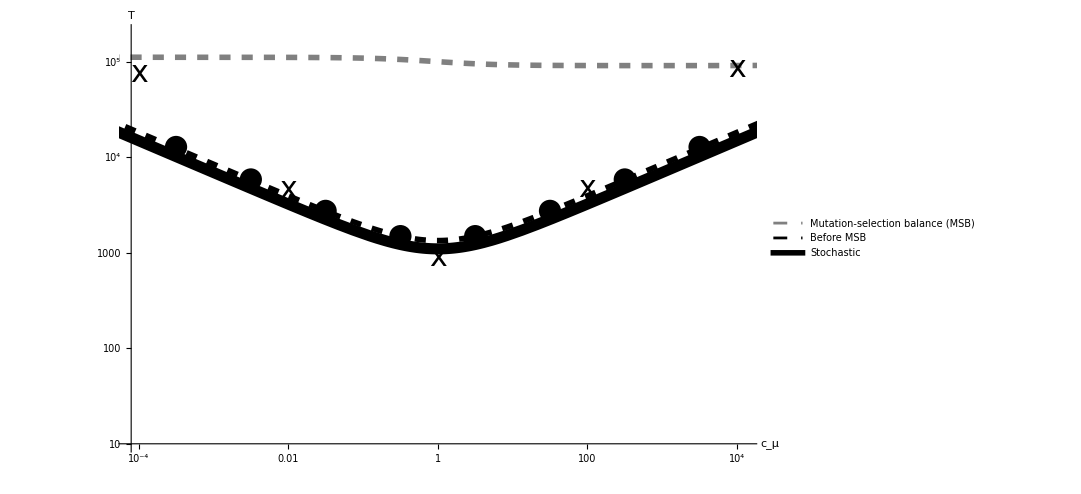

```mathematica
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1.01; 
n=10^6;
U=2*5*10^-7;
m1=5;
m2=5;

Legended[
Show[

(*full semi-deterministic solution*)
ListLogLogPlot[Table[{10^x,T/.FindRoot[(SumCN/.N->n/.c->10^x)==(1/n),{T,10^4},WorkingPrecision->50]},{x,-7/2,7/2,1}],PlotStyle->{Black,PointSize[.02]},PlotRange->{{10^-4.1,10^4.1},{10,2*10^5}}],

(*semi-deterministic equation with recombination and selection*)
LogLogPlot[TDetRCN/.N->n,{c,10^-m1,10^m2},PlotStyle->{Black,Thickness[0.005],Dashing[0.01]}],

(*semi-deterministic equation with MSB*)
LogLogPlot[TMSBCN/.N->n,{c,10^-m1,10^m2},PlotStyle->{Gray,Thickness[0.005],Dashing[0.01]}],

(*stochastic equation with recombination*)
LogLogPlot[TStochRCN/.N->n,{c,10^-m1,10^m2},PlotStyle->{Black,Thickness[0.01]}],

ListLogLogPlot[
{
{10^-4,CytoTime0},
{10^-2,CytoTimei},
{10^0,CytoTimeii},
{10^2,CytoTimeiii},
{10^4,CytoTimeiv}
},
PlotMarkers->{"x",30},
PlotStyle->{Black}],

AxesLabel->{Style["c_μ",AxisSize],Style["T",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],
Placed[
LineLegend[
{Directive[Thickness[0.1],Gray,Dashed],Directive[Thickness[0.1],Black,Dashed],Directive[Thickness[0.25],Black]},
{Style["Mutation-selection balance (MSB)",24],Style["Before MSB",24],Style["Stochastic",24]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.2}
]
]

Export[dir<>"TimeFixUniLogU2SimsBW.eps",%];

Clear[n,m1,m2,U,w]
```

#### Simulations for Figure 4

Simulation function for grey curve

```mathematica
w[1]=1;(*A1B1 viability*)
w[2]=1-10^-5; (*A2B1 viability*)
w[3]=w[2]; (*A1B2 viability*)
w[4]=1+1.01;(*A2B2 viability*)
NUM=10^6; (*pop size*)
MAXgen=10NUM; (*a cut off time limit that avoids running an infinite loop while testing (increase if triggered)*)
NUMtrials=10^3; (*number of trials; must be more than inverse of probability*)
i0=100; (*initial number of A2B1*)
μ=5*10^-7; (*mutation probability in B*)

runCytoProbGray[c_,seednum_]:=runCytoProbGray[c,seednum]=
Block[{fixed=0,lost=0},
SeedRandom[seednum];
For[trial=1,trial≤NUMtrials,trial++,
gen=0; 
vec={1-i0(1+c)/NUM,i0/NUM,i0 c/NUM,0};
finished=False;

While[finished==False,

gen++;
x1:=vec[[1]];
x2:=vec[[2]];
x3:=vec[[3]];
x4:=vec[[4]];
newx1:=Max[0,(x1^2+x1 x2 (1-μ) (1-c μ)+x1 x3 (1-μ) (1-c μ)+1/2 x2 x3 (1-μ) (1-c μ)+1/2 x1 x4 (1-μ) (1-c μ)) w[1]];
newx2:=(x2^2 (1-c μ)+x2 x4 (1-c μ)+x1 x3 μ (1-c μ)+x1 x2 (1+μ) (1-c μ)+1/2 x2 x3 (1+μ) (1-c μ)+1/2 x1 x4 (1+μ) (1-c μ)) w[2];
newx3:=(x1 x3 (1-μ)+1/2 x2 x3 (1-μ)+x3^2 (1-μ)+1/2 x1 x4 (1-μ)+x3 x4 (1-μ)+c x1 x2 (1-μ) μ+c x1 x3 (1-μ) μ+1/2 c x2 x3 (1-μ) μ+1/2 c x1 x4 (1-μ) μ) w[3];
newx4:=(x2 x4+x4^2+c x2^2 μ+x1 x3 μ+x3^2 μ+c x2 x4 μ+c x1 x3 μ^2+1/2 x2 x3 (1+μ)+1/2 x1 x4 (1+μ)+x3 x4 (1+μ)+c x1 x2 μ (1+μ)+1/2 c x2 x3 μ (1+μ)+1/2 c x1 x4 μ (1+μ)) w[4];

total:=newx1+newx2+newx3+newx4;

newvec:={newx1,newx2,newx3,newx4}/total;

num=RandomInteger[MultinomialDistribution[NUM,newvec]];

vec=num/NUM;

If[num[[4]]==NUM,finished=True; fixed=fixed+1];
If[num[[2]]+num[[3]]+num[[4]]==0,finished=True; lost=lost+1];
If[(num[[2]]==NUM)||(num[[3]]==NUM),finished=True;Print["Warning: a single mutant fixed."]];
If[gen==MAXgen,finished=True;Print["Warning: ended prematurely; increase MAXgen."]];
]
];
{lost,fixed}
]
```

Simulations giving crossing probabilities. Can take a long time to run. Results pasted below to skip re-running.

```mathematica
(*CytoProbGrayi=runCytoProbGray[10^0,14391][[2]]/NUMtrials//N
CytoProbGrayii=runCytoProbGray[10^1,92462][[2]]/NUMtrials//N
CytoProbGrayiii=runCytoProbGray[10^2,164151][[2]]/NUMtrials//N
CytoProbGrayiv=runCytoProbGray[10^3,16491][[2]]/NUMtrials//N
CytoProbGrayv=runCytoProbGray[10^4,1552][[2]]/NUMtrials//N*)
```

Simulation results

```mathematica
CytoProbGrayi=0.276;
CytoProbGrayii=0.875;
CytoProbGrayiii=1;
CytoProbGrayiv=1;
CytoProbGrayv=1;
```

```mathematica
Clear[w,NUM,MAXgen,NUMtrials,i0,μ,x1,x2,x3,x4]
```

Simulation function for black curve

```mathematica
w[1]=1; (*A1B1 viability*)
w[2]=1-10^-5; (*A2B1 viability*)
w[3]=w[2]; (*A1B2 viability*)
w[4]=1+1.01;(*A2B2 viability*)
NUM=10^6; (*pop size*)
MAXgen=10NUM; (*a cut off time limit that avoids running an infinite loop while testing (increase if triggered)*)
NUMtrials=10^3; (*number of trials; must be more than inverse of probability*)
NM=200; (*initial number of single mutants*)
U=2*5*10^-7; (*total mutation prob*)

runCytoProbBlack[c_,seednum_]:=runCytoProbBlack[c,seednum]=
Block[{fixed=0,lost=0},
SeedRandom[seednum];
For[trial=1,trial≤NUMtrials,trial++,
gen=0; 
vec={1-NM/NUM,NM/(1+c)/NUM, c NM/(1+c)/NUM,0};
finished=False;

While[finished==False,

gen++;
x1:=vec[[1]];
x2:=vec[[2]];
x3:=vec[[3]];
x4:=vec[[4]];
newx1:=(x1^2+(1-U/(1+c)) (1-(c U)/(1+c)) x1 x2+(1-U/(1+c)) (1-(c U)/(1+c)) x1 x3+1/2 (1-U/(1+c)) (1-(c U)/(1+c)) x2 x3+1/2 (1-U/(1+c)) (1-(c U)/(1+c)) x1 x4) w[1];
newx2:=((1+U/(1+c)) (1-(c U)/(1+c)) x1 x2+(1-(c U)/(1+c)) x2^2+(U (1-(c U)/(1+c)) x1 x3)/(1+c)+1/2 (1+U/(1+c)) (1-(c U)/(1+c)) x2 x3+1/2 (1+U/(1+c)) (1-(c U)/(1+c)) x1 x4+(1-(c U)/(1+c)) x2 x4) w[2];
newx3:=((c U (1-U/(1+c)) x1 x2)/(1+c)+(1-U/(1+c)) x1 x3+(c U (1-U/(1+c)) x1 x3)/(1+c)+1/2 (1-U/(1+c)) x2 x3+(c U (1-U/(1+c)) x2 x3)/(2 (1+c))+(1-U/(1+c)) x3^2+1/2 (1-U/(1+c)) x1 x4+(c U (1-U/(1+c)) x1 x4)/(2 (1+c))+(1-U/(1+c)) x3 x4) w[3];
newx4:=((c U (1+U/(1+c)) x1 x2)/(1+c)+(c U x2^2)/(1+c)+(U x1 x3)/(1+c)+(c U^2 x1 x3)/(1+c)^2+1/2 (1+U/(1+c)) x2 x3+(c U (1+U/(1+c)) x2 x3)/(2 (1+c))+(U x3^2)/(1+c)+1/2 (1+U/(1+c)) x1 x4+(c U (1+U/(1+c)) x1 x4)/(2 (1+c))+x2 x4+(c U x2 x4)/(1+c)+(1+U/(1+c)) x3 x4+x4^2) w[4];

total:=newx1+newx2+newx3+newx4;

newvec:={newx1,newx2,newx3,newx4}/total;

num=RandomInteger[MultinomialDistribution[NUM,newvec]];

vec=num/NUM;

If[num[[4]]==NUM,finished=True; fixed=fixed+1];
If[num[[2]]+num[[3]]+num[[4]]==0,finished=True; lost=lost+1];
If[(num[[2]]==NUM)||(num[[3]]==NUM),finished=True;Print["Warning: a single mutant fixed."]];
If[gen==MAXgen,finished=True;Print["Warning: ended prematurely; increase MAXgen."]];
]
];
{lost,fixed}
]
```

Simulations giving crossing probabilities. Can take a long time to run. Results pasted below to skip re-running.

```mathematica
(*CytoProbBlacki=runCytoProbBlack[10^0,13254][[2]]/NUMtrials//N
CytoProbBlackii=runCytoProbBlack[10^1,1226][[2]]/NUMtrials//N
CytoProbBlackiii=runCytoProbBlack[10^2,126471][[2]]/NUMtrials//N
CytoProbBlackiv=runCytoProbBlack[10^3,16274][[2]]/NUMtrials//N
CytoProbBlackv=runCytoProbBlack[10^4,19871][[2]]/NUMtrials//N*)
```

Simulation results

```mathematica
CytoProbBlacki=0.273;
CytoProbBlackii=0.099;
CytoProbBlackiii=0.018;
CytoProbBlackiv=0.011;
CytoProbBlackv=0;
```

```mathematica
Clear[w,NUM,MAXgen,NUMtrials,NM,U,x1,x2,x3,x4]
```

#### Figure 4

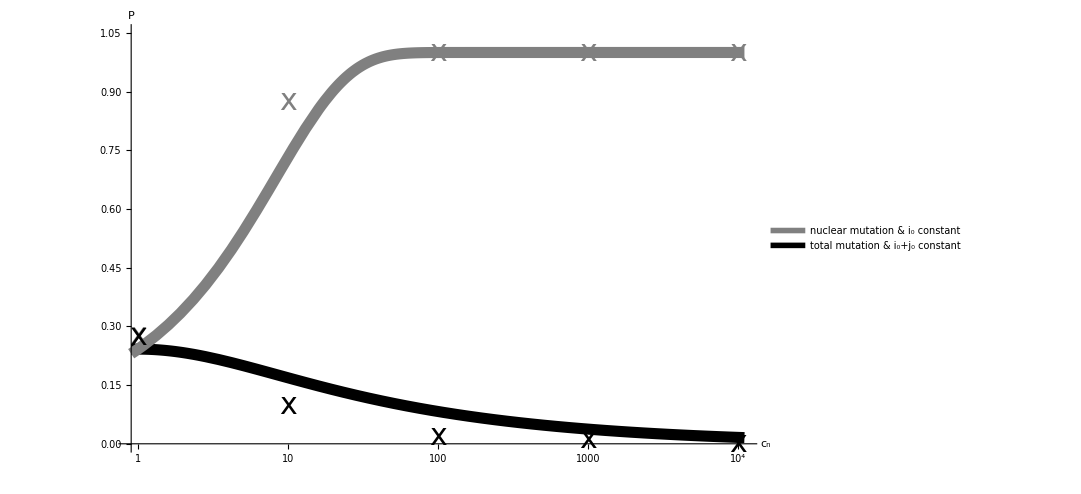

```mathematica
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1.01;
n=10^6;
ν= c μ;
U=2*5*10^-7;
NM=200;
xmin=0.9*1;
xmax=1.1*10^4;
ymin=0;
ymax=1.05;

Legended[
Show[

(*stochastic crossing probability by recombination, holding total mutation and initial number of single mutants constant*)
LogLinearPlot[PStochRCN/.N->n/.i0->NM/(1+c)/.μ->U/(1+c),{c,xmin,xmax},PlotStyle->{Black,Thickness[0.01]},PlotRange->{ymin,ymax}],

(*stochastic crossing probability by recombination, holding μ and i0 constant*)
LogLinearPlot[PStochRCN/.N->n/.i0->NM/2/.μ->U/2,{c,xmin,xmax},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{ymin,ymax}],

(*simulation results*)
ListLogLinearPlot[
{{10^0,CytoProbGrayi},
{10^1,CytoProbGrayii},
{10^2,CytoProbGrayiii},
{10^3,CytoProbGrayiv},
{10^4,CytoProbGrayiv}},
PlotMarkers->{"x",30},
PlotStyle->{Gray}],

ListLogLinearPlot[
{{10^0,CytoProbBlacki},
{10^1,CytoProbBlackii},
{10^2,CytoProbBlackiii},
{10^3,CytoProbBlackiv},
{10^4,CytoProbBlackv}},
PlotMarkers->{"x",30},
PlotStyle->{Black}],

AxesLabel->{Style["c_n",AxisSize],Style["P",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],
Placed[
LineLegend[
{Directive[Thickness[0.25],Gray],Directive[Thickness[0.25],Black]},
(*{Style["μ, i_0 constant",24],Style["μ+ν, i_0+j_0 constant",24]},*)
{Style["nuclear mutation & i_0 constant",24],Style["total mutation & i_0+j_0 constant",24]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.5}
]
]

Export[dir<>"ProbFixUniS2Sims.eps",%];

Clear[n,w,U,ν,NM,xmin,xmax,ymin,ymax]
```

### 3. Cultural inheritance

#### Transition probabilities, analytic solutions, recursions

Next we remove viability selection, pare transmission down to a very simple form, and interpret as a model of culture. A2B1 and A1B2 are assumed to be passed on over A1B1 with probability q. A2B2 is assumed to be passed on over A1B1 with probability p. Mutation probability in both traits is μ and recombination probability is r (order: recombination, cultural selection/bias, mutation). Transmission probabilities are

```mathematica
Cult={
b[1,1,1]->(1-μ)^2,
b[1,1,2]->μ(1-μ),
b[1,1,3]->μ(1-μ),
b[1,1,4]->μ^2,
b[1,2,1]->(1-q)(1-μ)^2,b[2,1,1]->(1-q)(1-μ)^2,
b[1,2,2]->(1-q)μ(1-μ)+q(1-μ),b[2,1,2]->(1-q)μ(1-μ)+q(1-μ),
b[1,2,3]->(1-q)μ(1-μ),b[2,1,3]->(1-q)μ(1-μ),
b[1,2,4]->(1-q)μ^2+q μ,b[2,1,4]->(1-q)μ^2+q μ,
b[1,3,1]->(1-q)(1-μ)^2,b[3,1,1]->(1-q)(1-μ)^2,
b[1,3,2]->(1-q)μ(1-μ),b[3,1,2]->(1-q)μ(1-μ),
b[1,3,3]->(1-q)μ(1-μ)+q(1-μ),b[3,1,3]->(1-q)μ(1-μ)+q(1-μ),
b[1,3,4]->(1-q)μ^2+q μ,b[3,1,4]->(1-q)μ^2+q μ,
b[1,4,1]->(1-r)(1-p)(1-μ)^2,b[4,1,1]->(1-r)(1-p)(1-μ)^2,
b[1,4,2]->(1-r)(1-p)μ(1-μ)+r(1-μ)/2,b[4,1,2]->(1-r)(1-p)μ(1-μ)+r(1-μ)/2,
b[1,4,3]->(1-r)(1-p)μ(1-μ)+r(1-μ)/2,b[4,1,3]->(1-r)(1-p)μ(1-μ)+r(1-μ)/2,
b[1,4,4]->(1-r)((1-p)μ^2+p)+r μ,b[4,1,4]->(1-r)((1-p)μ^2+p)+r μ,
b[2,2,1]->0,
b[2,2,2]->1-μ,
b[2,2,3]->0,
b[2,2,4]->μ,
b[2,3,1]->r(1-p)(1-μ)^2,b[3,2,1]->r(1-p)(1-μ)^2,
b[2,3,2]->(1-r)(1-μ)/2+r (1-p)μ(1-μ),b[3,2,2]->(1-r)(1-μ)/2+r (1-p)μ(1-μ),
b[2,3,3]->(1-r)(1-μ)/2+r (1-p)μ(1-μ),b[3,2,3]->(1-r)(1-μ)/2+r (1-p)μ(1-μ),
b[2,3,4]->(1-r)μ+r (p+(1-p)μ^2),b[3,2,4]->(1-r)μ+r (p+(1-p)μ^2),
b[2,4,1]->0,b[4,2,1]->0,
b[2,4,2]->(1/2-p+q)(1-μ),b[4,2,2]->(1/2-p+q)(1-μ),
b[2,4,3]->0,b[4,2,3]->0,
b[2,4,4]->(1/2-p+q)μ+(1/2+p-q),b[4,2,4]->(1/2-p+q)μ+(1/2+p-q),
b[3,3,1]->0,
b[3,3,2]->0,
b[3,3,3]->1-μ,
b[3,3,4]->μ,
b[3,4,1]->0,b[4,3,1]->0,
b[3,4,2]->0,b[4,3,2]->0,
b[3,4,3]->(1/2-p+q)(1-μ),b[4,3,3]->(1/2-p+q)(1-μ),
b[3,4,4]->(1/2-p+q)μ+(1/2+p-q),b[4,3,4]->(1/2-p+q)μ+(1/2+p-q),
b[4,4,1]->0,
b[4,4,2]->0,
b[4,4,3]->0,
b[4,4,4]->1
};
```

Then the analytic and numerical crossing times are

```mathematica
TDetMutCult=TDetMut/.Cult/.r->0;
TDetRCult=TDetR/.Cult;
CultSum=x4pDMSum/.Cult;
TMSBCult=TDetMutSel/.Cult;
TStochMutCult=TStochMut/.Cult/.r->0;
TStochRCult=TStochR/.Cult;
```

The recursion equations are

```mathematica
eqn[1]/.Cult/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[2]/.Cult/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[3]/.Cult/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[4]/.Cult/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
```

The analytic crossing probabilities are

```mathematica
PStochRCult=PStochR/.Cult;
PStochMutCult=PStochMut/.Cult;
```

Not allowing mutations in resident-resident matings, the recursion equations are

```mathematica
eqn[1]/.b[1,1,1]->1/.Cult/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[2]/.b[1,1,2]->0/.Cult/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[3]/.b[1,1,3]->0/.Cult/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
eqn[4]/.b[1,1,4]->0/.Cult/.x[1]->x1/.x[2]->x2/.x[3]->x3/.x[4]->x4;
```

#### Simulations for Figure 5

Simulation function

```mathematica
w[1]=1; (*A1B1 viability*)
w[2]=1;(*A2B1 viability*)
w[3]=1;(*A1B2 viability*)
w[4]=1;(*A2B2 viability*)
μ=10^-3; (*mutation probability*)
r=1/100; (*recombination probability*)
NUM=10^3; (*pop size*)
MAXgen=10^6; (*a cut off time limit that avoids running an infinite loop while testing (increase if triggered)*)
NUMtrials=10^2; (*number of trials*)

runCultTime[q_,p_,seednum_]:=runCultTime[q,p,seednum]=
Block[{fixed=0,lost=0},
SeedRandom[seednum];
For[trial=1,trial≤NUMtrials,trial++,
gen=0; 
vec={1,0,0,0};
finished=False;

While[finished==False,

gen++;
x1:=vec[[1]];
x2:=vec[[2]];
x3:=vec[[3]];
x4:=vec[[4]];
newx1:=(x1^2 (1-μ)^2+2 (1-q) x1 x2 (1-μ)^2+2 (1-q) x1 x3 (1-μ)^2+2 (1-p) r x2 x3 (1-μ)^2+2 (1-p) (1-r) x1 x4 (1-μ)^2) w[1];
newx2:=(x2^2 (1-μ)+2 (1/2-p+q) x2 x4 (1-μ)+x1^2 (1-μ) μ+2 (1-q) x1 x3 (1-μ) μ+2 x1 x2 (q (1-μ)+(1-q) (1-μ) μ)+2 x1 x4 (1/2 r (1-μ)+(1-p) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+(1-p) r (1-μ) μ)) w[2];
newx3:=(x3^2 (1-μ)+2 (1/2-p+q) x3 x4 (1-μ)+x1^2 (1-μ) μ+2 (1-q) x1 x2 (1-μ) μ+2 x1 x3 (q (1-μ)+(1-q) (1-μ) μ)+2 x1 x4 (1/2 r (1-μ)+(1-p) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+(1-p) r (1-μ) μ)) w[3];
newx4:=(x4^2+x2^2 μ+x3^2 μ+x1^2 μ^2+2 x2 x4 (1/2+p-q+(1/2-p+q) μ)+2 x3 x4 (1/2+p-q+(1/2-p+q) μ)+2 x1 x2 (q μ+(1-q) μ^2)+2 x1 x3 (q μ+(1-q) μ^2)+2 x1 x4 (r μ+(1-r) (p+(1-p) μ^2))+2 x2 x3 ((1-r) μ+r (p+(1-p) μ^2))) w[4];

total:=newx1+newx2+newx3+newx4;

newvec:={newx1,newx2,newx3,newx4}/total;

num=RandomInteger[MultinomialDistribution[NUM,newvec]];

vec=num/NUM;

If[num[[4]]==NUM,finished=True; time[trial]=gen];
If[gen==MAXgen,finished=True;Print["Warning: ended prematurely; increase MAXgen."]];
]
];
Table[time[i],{i,1,NUMtrials}]
]
```

Simulations giving mean crossing times. Can take a long time to run. Results pasted below to skip re-running.

```mathematica
(*large double mutant advantage*)
(*CultTimeThicki=Mean[runCultTime[0.1,0.6,46583]]//N
CultTimeThickii=Mean[runCultTime[0.2,0.6,465976]]//N
CultTimeThickiii=Mean[runCultTime[0.3,0.6,524456723]]//N
CultTimeThickiv=Mean[runCultTime[0.4,0.6,9878216]]//N
CultTimeThickv=Mean[runCultTime[0.5,0.6,16]]//N*)
```

```mathematica
(*small double mutant advantage*)
(*CultTimeThini=Mean[runCultTime[0.1,0.51,57243]]//N
CultTimeThinii=Mean[runCultTime[0.2,0.51,987586]]//N
CultTimeThiniii=Mean[runCultTime[0.3,0.51,13]]//N
CultTimeThiniv=Mean[runCultTime[0.4,0.51,98246]]//N
CultTimeThinv=Mean[runCultTime[0.5,0.51,96]]//N*)
```

Simulation results

```mathematica
(*large double mutant advantage*)
CultTimeThicki=2091.63;
CultTimeThickii=1479.43;
CultTimeThickiii=781.58;
CultTimeThickiv=348.34;
CultTimeThickv=116.81;
```

```mathematica
(*small double mutant advantage*)
CultTimeThini=27462.25;
CultTimeThinii=16405.26;
CultTimeThiniii=9696.64;
CultTimeThiniv=4860.02;
CultTimeThinv=573.24;
```

```mathematica
Clear[w,μ,r,NUM,NUMtrials,MAXgen,x1,x2,x3,x4]
```

#### Figure 5

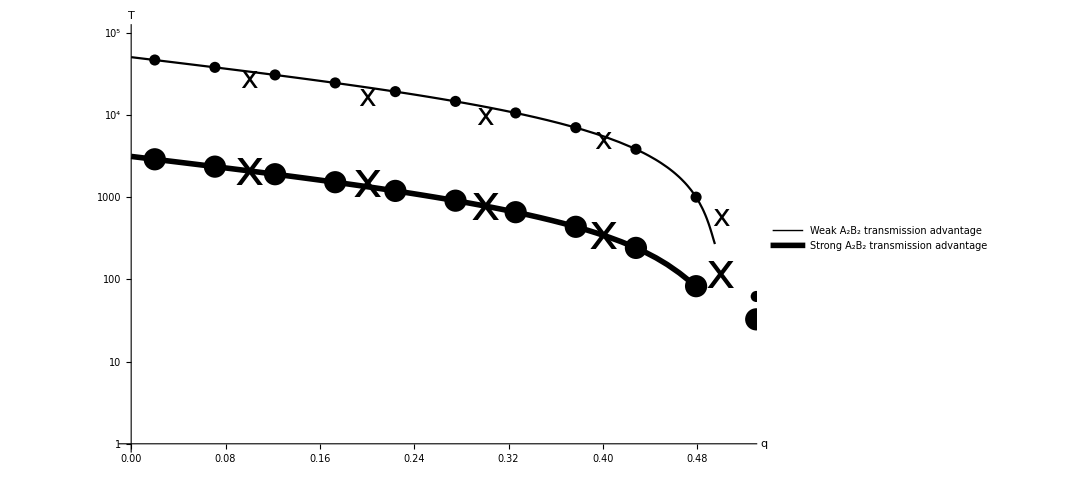

```mathematica
w[1]=1; 
w[2]=1;
w[3]=1;
w[4]=1;
n=10^3;
μ=10^-3;
r=1/100;
qmin=0;
qmax=52/100;
ymax=10^5;

Legended[
Show[

p=51/100;

(*full semi-deterministic result*)
ListLogPlot[Table[{q,T/.FindRoot[(CultSum/.N->n)==(1/n),{T,10^2},WorkingPrecision->50]},{q,2/100,6/10,51/1000}],PlotStyle->{Black,PointSize[.01]},PlotRange->{{qmin,qmax},{1,ymax}}],

(*semi-deterministic solution from MSB*)
LogPlot[TMSBCult/.N->n,{q,qmin,0.495},PlotStyle->{Black,Thickness[0.002]}],

p=60/100;

(*full semi-deterministic result*)
ListLogPlot[Table[{q,T/.FindRoot[(CultSum/.N->n)==(1/n),{T,10^2},WorkingPrecision->50]},{q,2/100,6/10,51/1000}],PlotStyle->{Black,PointSize[.02]},PlotRange->{{qmin,qmax},{1,ymax}}],

(*semi-deterministic solution from MSB*)
LogPlot[TMSBCult/.N->n,{q,qmin,0.485},PlotStyle->{Black,Thickness[0.005]}],

(*simulation results*)
ListLogPlot[
{{0.1,CultTimeThicki},
{0.2,CultTimeThickii},
{0.3,CultTimeThickiii},
{0.4,CultTimeThickiv},
{0.5,CultTimeThickv}},
PlotMarkers->{"x",50},
PlotStyle->{Black}],

ListLogPlot[
{{0.1,CultTimeThini},
{0.2,CultTimeThinii},
{0.3,CultTimeThiniii},
{0.4,CultTimeThiniv},
{0.5,CultTimeThinv}},
PlotMarkers->{"x",30},
PlotStyle->{Black}],

AxesLabel->{Style["q",AxisSize],Style["T",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],

Placed[
LineLegend[
{Directive[Thickness[0.05],Black],Directive[Thickness[0.2],Black]},
{Style["Weak A_2B_2 transmission advantage",24],Style["Strong A_2B_2 transmission advantage",24]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.25}
]
]

Export[dir<>"TimeFixCultLogPSimsBW.eps",%];

Clear[n,μ,w,r,qmin,qmax,p,ymax]
```

#### Simulations for Figure 6

Simulation function

```mathematica
w[1]=1; (*A1B1 viability*)
w[2]=1;(*A2B1 viability*)
w[3]=1;(*A1B2 viability*)
w[4]=1;(*A2B2 viability*)
NUM=10^3; (*pop size*)
MAXgen=10^3 NUM; (*a cut off time limit that avoids running an infinite loop while testing (increase if triggered)*)
NUMtrials=10^5; (*number of trials; must be more than inverse of probability*)
i0=10; (*initial number of A2B1*)
j0=i0; (*initial number of A1B2*)

runCultProb[q_,p_,r_,μ_,seednum_]:=runCultProb[q,p,r,μ,seednum]=
Block[{fixed=0,lost=0},
SeedRandom[seednum];
For[trial=1,trial≤NUMtrials,trial++,
gen=0; 
vec={1-(i0+j0)/NUM,i0/NUM,j0/NUM,0};
finished=False;

While[finished==False,

gen++;
x1:=vec[[1]];
x2:=vec[[2]];
x3:=vec[[3]];
x4:=vec[[4]];
newx1:=(x1^2+2 (1-q) x1 x2 (1-μ)^2+2 (1-q) x1 x3 (1-μ)^2+2 (1-p) r x2 x3 (1-μ)^2+2 (1-p) (1-r) x1 x4 (1-μ)^2) w[1];
newx2=(x2^2 (1-μ)+2 (1/2-p+q) x2 x4 (1-μ)+2 (1-q) x1 x3 (1-μ) μ+2 x1 x2 (q (1-μ)+(1-q) (1-μ) μ)+2 x1 x4 (1/2 r (1-μ)+(1-p) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+(1-p) r (1-μ) μ)) w[2];
newx3:=(x3^2 (1-μ)+2 (1/2-p+q) x3 x4 (1-μ)+2 (1-q) x1 x2 (1-μ) μ+2 x1 x3 (q (1-μ)+(1-q) (1-μ) μ)+2 x1 x4 (1/2 r (1-μ)+(1-p) (1-r) (1-μ) μ)+2 x2 x3 (1/2 (1-r) (1-μ)+(1-p) r (1-μ) μ)) w[3];
newx4:=(x4^2+x2^2 μ+x3^2 μ+2 x2 x4 (1/2+p-q+(1/2-p+q) μ)+2 x3 x4 (1/2+p-q+(1/2-p+q) μ)+2 x1 x2 (q μ+(1-q) μ^2)+2 x1 x3 (q μ+(1-q) μ^2)+2 x1 x4 (r μ+(1-r) (p+(1-p) μ^2))+2 x2 x3 ((1-r) μ+r (p+(1-p) μ^2))) w[4];

total:=newx1+newx2+newx3+newx4;

newvec:={newx1,newx2,newx3,newx4}/total;

num=RandomInteger[MultinomialDistribution[NUM,newvec]];

vec=num/NUM;

If[num[[4]]==NUM,finished=True; fixed=fixed+1];
If[(num[[2]]+num[[3]]+num[[4]]==0),finished=True; lost=lost+1];
If[(num[[2]]==NUM)||(num[[3]]==NUM),finished=True;Print["Warning: a single mutant fixed."]];
If[gen==MAXgen,finished=True;Print["Warning: ended prematurely; increase MAXgen."]];
]
];
{lost,fixed}
]
```

Simulations giving crossing probabilities. Can take a long time to run. Results pasted below to skip re-running.

```mathematica
(*Large A2B2 advantage, mutation*)
(*CultProbGrayThicki=runCultProb[0.45,0.6,0,10^-3,41657][[2]]/NUMtrials//N
CultProbGrayThickii=runCultProb[0.47,0.6,0,10^-3,41657][[2]]/NUMtrials//N
CultProbGrayThickiii=runCultProb[0.49,0.6,0,10^-3,41657][[2]]/NUMtrials//N*)
```

```mathematica
(*Small A2B2 advantage, mutation*)
(*CultProbGrayThini=runCultProb[0.45,0.51,0,10^-3,41657][[2]]/NUMtrials//N
CultProbGrayThinii=runCultProb[0.47,0.51,0,10^-3,41657][[2]]/NUMtrials//N
CultProbGrayThiniii=runCultProb[0.49,0.51,0,10^-3,41657][[2]]/NUMtrials//N*)
```

```mathematica
(*Large A2B2 advantage, recombination*)
(*CultProbBlackThicki=runCultProb[0.45,0.6,10^-2,0,41657][[2]]/NUMtrials//N
CultProbBlackThickii=runCultProb[0.47,0.6,10^-2,0,41657][[2]]/NUMtrials//N
CultProbBlackThickiii=runCultProb[0.49,0.6,10^-2,0,425257][[2]]/NUMtrials//N*)
```

```mathematica
(*Small A2B2 advantage, recombination*)
(*CultProbBlackThini=runCultProb[0.45,0.51,10^-2,0,571][[2]]/NUMtrials//N
CultProbBlackThinii=runCultProb[0.47,0.51,10^-2,0,41663574][[2]]/NUMtrials//N
CultProbBlackThiniii=runCultProb[0.49,0.51,10^-2,0,4527257][[2]]/NUMtrials//N*)
```

Simulation results

```mathematica
(*Large A2B2 advantage, mutation*)
CultProbGrayThicki=0.05686;
CultProbGrayThickii=0.09379;
CultProbGrayThickiii=0.22294;
```

```mathematica
(*Small A2B2 advantage, mutation*)
CultProbGrayThini=0.00726;
CultProbGrayThinii=0.01304;
CultProbGrayThiniii=0.03977;
```

```mathematica
(*Large A2B2 advantage, recombination*)
CultProbBlackThicki=0.00189;
CultProbBlackThickii=0.00308;
CultProbBlackThickiii=0.00831;
```

```mathematica
(*Small A2B2 advantage, recombination*)
CultProbBlackThini=0.00012;
CultProbBlackThinii=0.00027;
CultProbBlackThiniii=0.00072;
```

```mathematica
Clear[w,NUM,NUMtrials,MAXgen,i0,j0,x1,x2,x3,x4]
```

#### Figure 6

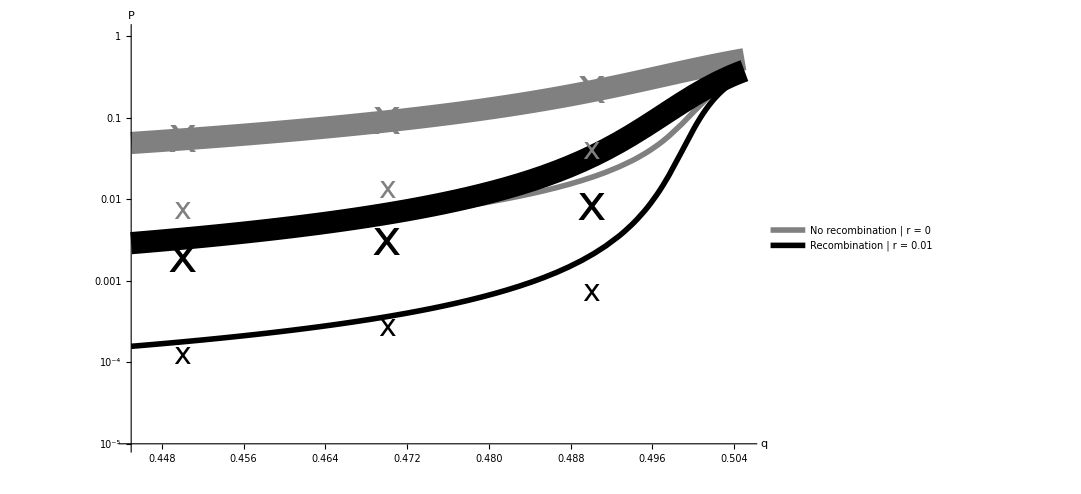

```mathematica
w[1]=1;
w[2]=1;
w[3]=1;
w[4]=1;
n=10^3;
μ=10^-3;
r=0.01;
c=1;
qmin=0.445;
qmax=0.505;
n0=20;
i0=n0/2;

Legended[
Show[
p=0.51;

(*stochastic crossing probability, by mutation*)
LogPlot[PStochMutCult/.N->n,{q,qmin,qmax},PlotStyle->{Gray,Thickness[0.005]},PlotRange->{0.1*10^-4,1.1}],
(*stochastic crossing probability, by recombination*)
LogPlot[PStochRCult/.N->n,{q,qmin,qmax},PlotStyle->{Black,Thickness[0.005]}],

p=0.6;

(*stochastic crossing probability, by mutation*)
LogPlot[PStochMutCult/.N->n,{q,qmin,qmax},PlotStyle->{Gray,Thickness[0.02]},PlotRange->{10^-3,1.1}],
(*stochastic crossing probability, by recombination*)
LogPlot[PStochRCult/.N->n,{q,qmin,qmax},PlotStyle->{Black,Thickness[0.02]}],

(*simulation results*)
ListLogPlot[
{{0.45,CultProbGrayThicki},
{0.47,CultProbGrayThickii},
{0.49,CultProbGrayThickiii}},
PlotMarkers->{"x",50},
PlotStyle->{Gray}],

ListLogPlot[
{{0.45,CultProbGrayThini},
{0.47,CultProbGrayThinii},
{0.49,CultProbGrayThiniii}},
PlotMarkers->{"x",30},
PlotStyle->{Gray}],

ListLogPlot[
{{0.45,CultProbBlackThicki},
{0.47,CultProbBlackThickii},
{0.49,CultProbBlackThickiii}},
PlotMarkers->{"x",50},
PlotStyle->{Black}],

ListLogPlot[
{{0.45,CultProbBlackThini},
{0.47,CultProbBlackThinii},
{0.49,CultProbBlackThiniii}},
PlotMarkers->{"x",30},
PlotStyle->{Black}],

AxesLabel->{Style["q",AxisSize],Style["P",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],

Placed[
LineLegend[
{Directive[Thickness[0.25],Gray],Directive[Thickness[0.25],Black]},
{Style["No recombination | r = 0",24],Style["Recombination | r = 0.01",24]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.2}
]
]

Export[dir<>"ProbFixCultPSims.eps",%];

Clear[n,μ,w,r,c,qmin,qmax,p,n0,i0]
```

## Numerical examples (in Discussion)

### Fair transmission

2 locus crossing time with recombination and neutral single mutants

```mathematica
TStochR/.Killer/.k->0/.c->1/.N->10^4/.w[4]->1.01/.r->0.01/.μ->10^-8
```

2.73298×10^7

### Transmission bias

The probability of a successful double mutant appearing from standing variation, without bias and with a 0.05 viability disadvantage to single mutants, without recombination, w4 = 1.01, n0 = 1, μ=10^-8, and N=10^4, is

```mathematica
PStochMut/.b[1,4,4]->(1-r)/2/.b[4,1,4]->(1-r)/2/.r->0/.b[1,2,2]->1/2/.b[2,1,2]->1/2/.n0->1/.b[i_,j_,k_]->10^-8/2/.w[4]->1.01/.w[2]->1-0.05/.N->10^4
```

3.99987×10^-9

With a 2.5% transmission bias (still deleterious single mutants) in favour of single mutants this is

```mathematica
PStochMut/.b[1,4,4]->(1-r)/2/.b[4,1,4]->(1-r)/2/.r->0/.b[1,2,2]->1/2+k/.b[2,1,2]->1/2+k/.n0->1/.b[i_,j_,k_]->10^-8/2/.w[4]->1.01/.w[2]->1-0.05/.k->0.025/.N->10^4
```

7.99961×10^-8

A 5% transmission bias (now neutral single mutants) gives

```mathematica
PStochMut/.b[1,4,4]->(1-r)/2/.b[4,1,4]->(1-r)/2/.r->0/.b[1,2,2]->1/2+k/.b[2,1,2]->1/2+k/.n0->1/.b[i_,j_,k_]->10^-8/2/.w[4]->1.01/.w[2]->1-0.05/.k->0.05/.N->10^4
```

0.0860688

A 10% transmission bias (now beneficial single mutants) gives

```mathematica
PStochMut/.b[1,4,4]->(1-r)/2/.b[4,1,4]->(1-r)/2/.r->0/.b[1,2,2]->1/2+k/.b[2,1,2]->1/2+k/.n0->1/.b[i_,j_,k_]->10^-8/2/.w[4]->1.01/.w[2]->1-0.05/.k->0.1/.N->10^4
```

0.244216

### Rearrangements

In the case of underdominant chromosomal rearrangements the mutation rate can be much higher, and with a large mutant homokaryotype advantage, 5% heterokaryotype viability cost, free recombination, and no bias, the probability the mutant homokaryotype fixes from one of each type of heterokaryotype is

```mathematica
PStochR /.c->1/.i0->1/.b[1,2,2]->k/.b[2,1,2]->k/.b[2,3,4]->r k/.b[3,2,4]->r k/.s->sDMrare/.b[1,4,4]->(1-r)k/.b[4,1,4]->(1-r)k/.w[4]->2.5/.r->1/2/.w[2]->0.95/.w[3]->0.95/.N->10^4/.k->0.5
```

0.00488078

And with 70% transmission probability in favour of mutant chromosomes we have

```mathematica
PStochR /.c->1/.i0->1/.b[1,2,2]->k/.b[2,1,2]->k/.b[2,3,4]->r k/.b[3,2,4]->r k/.s->sDMrare/.b[1,4,4]->(1-r)k/.b[4,1,4]->(1-r)k/.w[4]->2.5/.r->1/2/.w[2]->0.95/.w[3]->0.95/.N->10^4/.k->0.7
```

0.733003

### Cytonuclear

Crossing time with N=10^4, μ=10^-6, w[4] = 2, and equal mutation rates in the two loci (c = 1)

```mathematica
N[TStochRCN/.N->10^4/.U->μ(1+c)/.μ->10^-6/.w[4]->2/.c->1]
```

40234.4

Increasing the mutation rate in the second locus 100x speeds crossing

```mathematica
N[TStochRCN/.N->10^4/.U->μ(1+c)/.μ->10^-6/.w[4]->2/.c->100]
```

2419.63

Increasing the mutation rate in the second locus while holding total mutation rate (μ+⋁=2*10^-6) constant slows crossing

```mathematica
N[TStochRCN/.N->10^4/.U->2*10^-6/.w[4]->2/.c->100]
```

118429.

## Oaxaca presentation [added after publication]

```mathematica
dir="/Users/mmosmond/Documents/PHD/OAXACA/IMAGES/";
```

### 1. Segregation distortion

#### Figure 1 (top)

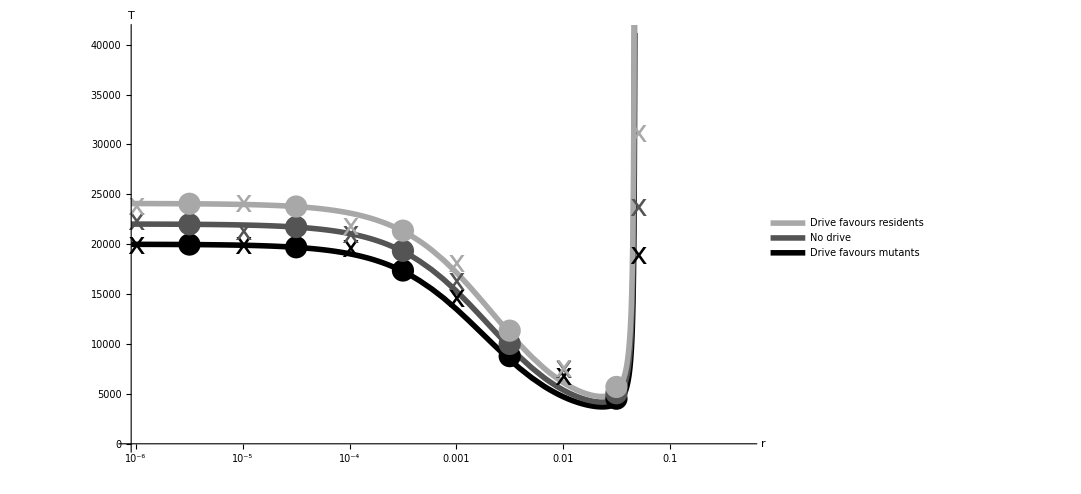

```mathematica
w[2]=1-10^-3;
w[3]=w[2];
w[4]=1+1/20;
n=10^6;
k1=10^-4;
k2=0;
k3=-10^-4;
μ=5*10^-7;
xmin=0.9*10^-6;
xmax=0.5;
ymin=0;
ymax=Automatic;

Legended[
Show[

(*MSB solutions*)
LogLinearPlot[MSBSk/.N->n/.k->k1,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0],Thickness[0.005]}],
LogLinearPlot[MSBSk/.N->n/.k->k2,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0.33],Thickness[0.005]}],
LogLinearPlot[MSBSk/.N->n/.k->k3,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0.66],Thickness[0.005]}],

(*full semi-deterministic solutions*)
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k1/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0],PointSize[.02]}],
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k2/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0.33],PointSize[.02]}],
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k3/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0.66],PointSize[.02]}],

(*simulation results*)
ListLogLinearPlot[
{{10^-6,KillTimeDeepGreen0},
{10^-5,KillTimeDeepGreeni},
{10^-4,KillTimeDeepGreenii},
{10^-3,KillTimeDeepGreeniii},
{10^-2,KillTimeDeepGreeniv},
{0.05,KillTimeDeepGreenv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0]}],

ListLogLinearPlot[
{{10^-6,KillTimeDeepBlack0},
{10^-5,KillTimeDeepBlacki},
{10^-4,KillTimeDeepBlackii},
{10^-3,KillTimeDeepBlackiii},
{10^-2,KillTimeDeepBlackiv},
{0.05,KillTimeDeepBlackv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.33]}],

ListLogLinearPlot[
{{10^-6,KillTimeDeepBlue0},
{10^-5,KillTimeDeepBluei},
{10^-4,KillTimeDeepBlueii},
{10^-3,KillTimeDeepBlueiii},
{10^-2,KillTimeDeepBlueiv},
{0.05,KillTimeDeepBluev}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.66]}],

AxesLabel->{Style["r",AxisSize]"",Style["T",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->{{TickSize},{TickSize}},
PlotRangePadding->None
],
Placed[
LineLegend[
{Directive[Thickness[0.25],GrayLevel[0.66]],Directive[Thickness[0.25],GrayLevel[0.33]],Directive[Thickness[0.25],GrayLevel[0]]},(*Table[Style[StringForm["k = ``",i],24],{i,{k3,k1,k2}}],*)
{Style["Drive favours residents",20],Style["No drive",20],Style["Drive favours mutants",20]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.25,0.25}
]
]

Export[dir<>"TimeFixDriveRMSBSimsBW.eps",%];

Clear[n,w,r,μ,k1,k2,k3,xmin,xmax,ymin,ymax]
```

Recombination is stronger than mutation, transmission bias, and viability selection in favour of the double mutant, r > s, when

```mathematica
Solve[sDMrare==0/.Killer,r]//FullSimplify
```

{{r→1-1/((1+k+μ^2-k μ^2) w[4])}}

In this case we have

```mathematica
Solve[sDMrare==0/.Killer,r]/.μ->5*10^-7/.w[4]->1+1/20/.k->0//N
```

{{r→0.047619}}

Weissman et al 2010 eqn B21 with deleterious single mutants gives  (assumes r >> s and δ >> (μ s)^(1/2))

```mathematica
δ/(2N μ^2 s)/.s->1/20/.N->10^6/.μ->5*10^-7/.δ->10^-3//N
```

40000.

#### Figure 1 (bottom)

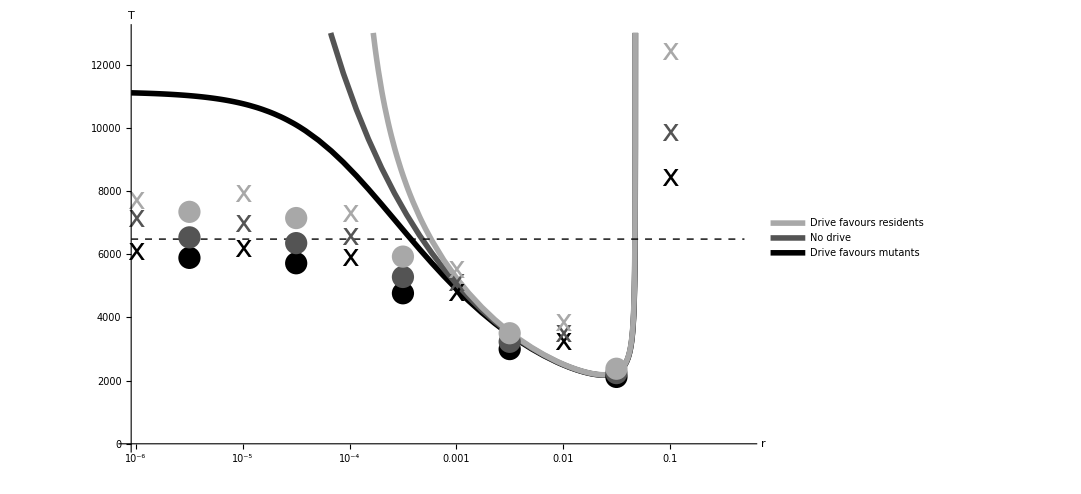

```mathematica
n=10^6;
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1/20;
k1=10^-4;
k2=0;
k3=-10^-4;
μ=5*10^-7;
xmin=0.9*10^-6;
xmax=0.5;
ymin=0;
ymax=1.3*10^4;

Legended[
Show[

(*cross by recmobination, semi-deterministic*)
LogLinearPlot[TDetRSk/.N->n/.k->k1,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0],Thickness[0.005]}],
LogLinearPlot[TDetRSk/.N->n/.k->k2,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0.33],Thickness[0.005]}],
LogLinearPlot[TDetRSk/.N->n/.k->k3,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{GrayLevel[0.66],Thickness[0.005]}],

(*cross by mutation, semi-deterministic*)
LogLinearPlot[TDetMutSk/.N->n/.k->k1,{r,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{Black,Thick,Dashed}],

(*full semi-deterministic solutions*)
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k1/.μ->μtemp/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0],PointSize[.02]}],
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k2/.μ->μtemp/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0.33],PointSize[.02]}],
ListLogLinearPlot[Table[{10^x,T/.Quiet[FindRoot[(KillerSum/.N->n/.k->k3/.μ->μtemp/.r->10^x)==(1/n),{T,10000},WorkingPrecision->30]]},{x,-11/2,-3/2,1}],PlotStyle->{GrayLevel[0.66],PointSize[.02]}],

(*simulation results*)
ListLogLinearPlot[
{{10^-6,KillTimeShallowGreen0},
{10^-5,KillTimeShallowGreeni},
{10^-4,KillTimeShallowGreenii},
{10^-3,KillTimeShallowGreeniii},
{10^-2,KillTimeShallowGreeniv},
{10^-1,KillTimeShallowGreenv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0]}],

ListLogLinearPlot[
{{10^-6,KillTimeShallowBlack0},
{10^-5,KillTimeShallowBlacki},
{10^-4,KillTimeShallowBlackii},
{10^-3,KillTimeShallowBlackiii},
{10^-2,KillTimeShallowBlackiv},
{10^-1,KillTimeShallowBlackv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.33]}],

ListLogLinearPlot[
{{10^-6,KillTimeShallowBlue0},
{10^-5,KillTimeShallowBluei},
{10^-4,KillTimeShallowBlueii},
{10^-3,KillTimeShallowBlueiii},
{10^-2,KillTimeShallowBlueiv},
{10^-1,KillTimeShallowBluev}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.66]}],

AxesLabel->{Style["r",AxisSize],Style["T",AxisSize]""},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],
Placed[
LineLegend[
{Directive[Thickness[0.25],GrayLevel[0.66]],Directive[Thickness[0.25],GrayLevel[0.33]],Directive[Thickness[0.25],GrayLevel[0]]},(*Table[Style[StringForm["k = ``",i],24],{i,{k3,k1,k2}}],*)
{Style["Drive favours residents",20],Style["No drive",20],Style["Drive favours mutants",20]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.25,0.2}
]
]

Export[dir<>"TimeFixDriveRSimsBW.eps",%];

Clear[n,w,r,μ,k1,k2,k3,xmin,xmax,ymin,ymax]
```

Recombination is stronger than mutation, transmission bias, and viability selection in favour of the double mutant, r > s, when

```mathematica
Solve[sDMrare==0/.Killer,r]//FullSimplify
```

{{r→1-1/((1+k+μ^2-k μ^2) w[4])}}

In this case we have

```mathematica
Solve[sDMrare==0/.Killer,r]/.μ->5*10^-7/.w[4]->1+1/20/.k->0//N
```

{{r→0.047619}}

Lynch 2010 eqn 8a (assumes r > s and δ = 0)

```mathematica
2/μ (μ/s)^(1/2)/.μ->5*10^-7/.s->1/20//N
```

12649.1

Weissman et al 2010 eqn B21 with neutral single mutants gives (assumes r >> s, δ << (μ (s))^(1/2), and N μ << 1)

```mathematica
1/(2N Sqrt[μ^3 s])/.s->1/20/.N->10^6/.μ->5*10^-7//N
```

6324.56

#### Figure 2 (top)

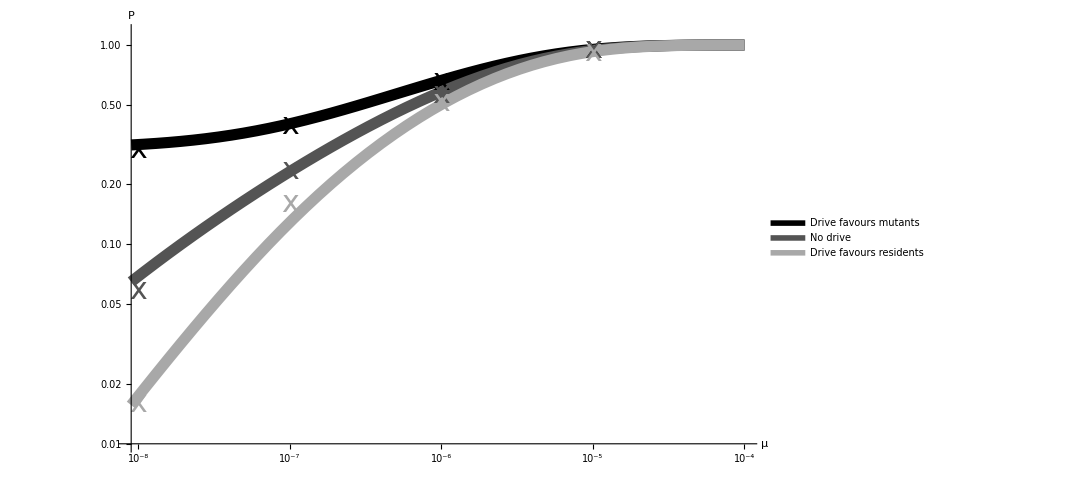

```mathematica
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1/20;
n=10^6;
i0=1000;
j0=i0;
n0=i0+j0;
k1=10^-4;
k2=0;
k3=-10^-4;
xmin=0.9*10^-8;
xmax=10^-4;
ymin=10^-2;
ymax=1.15;

Legended[
Show[
(*stochastic crossing probability by mutation*)
LogLogPlot[PStochMutSk/.N->n/.k->k1,{μ,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0]},PlotRange->{ymin,ymax}],
LogLogPlot[PStochMutSk/.N->n/.k->k2,{μ,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0.33]}],
LogLogPlot[PStochMutSk/.N->n/.k->k3,{μ,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0.66]}],

(*simulation results*)
ListLogLogPlot[
{{10^-8,KillProbMutGreeni},
{10^-7,KillProbMutGreenii},
{10^-6,KillProbMutGreeniii},
{10^-5,KillProbMutGreeniv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0]}
],

ListLogLogPlot[
{{10^-8,KillProbMutBlacki},
{10^-7,KillProbMutBlackii},
{10^-6,KillProbMutBlackiii},
{10^-5,KillProbMutBlackiv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.33]}
],

ListLogLogPlot[
{{10^-8,KillProbMutBluei},
{10^-7,KillProbMutBlueii},
{10^-6,KillProbMutBlueiii},
{10^-5,KillProbMutBlueiv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.66]}
],

AxesLabel->{Style["μ",AxisSize],Style["P",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],
Placed[
LineLegend[
{Directive[Thickness[0.25],GrayLevel[0]],Directive[Thickness[0.25],GrayLevel[0.33]],Directive[Thickness[0.25],GrayLevel[0.66]]},(*Table[Style[StringForm["k = ``",i],24],{i,{k3,k1,k2}}],*)
{Style["Drive favours mutants",20],Style["No drive",20],Style["Drive favours residents",20]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.8,0.3}
]
]

Export[dir<>"ProbFixDriveMutSimsBW.eps",%];

Clear[n0,i0,j0,w,n,k1,k2,k3,xmin,xmax,ymin,ymax]
```

#### Figure 2 (bottom)

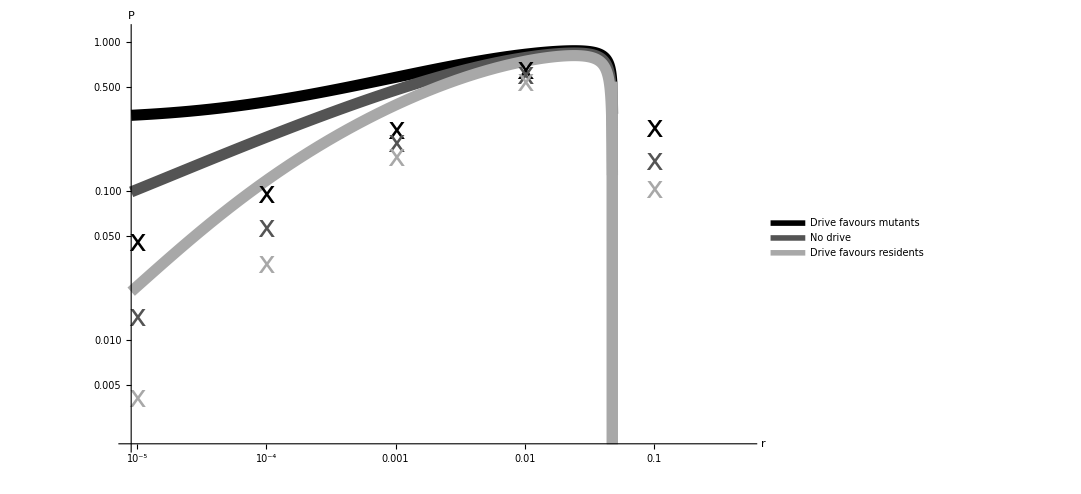

```mathematica
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1/20;
i0=1000;
n=10^6;
k1=10^-4;
k2=0;
k3=-10^-4;
c=1;
xmin=0.9*10^-5;
xmax=1/20;
ymin=2*10^-3;
ymax=1.15;
μ=5*10^-7;

Legended[
Show[

(*stochastic crossing probability by recombination*)
LogLogPlot[PStochRSk/.N->n/.k->k1,{r,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0]},PlotRange->{{xmin,0.5},{ymin,ymax}}],
LogLogPlot[PStochRSk/.N->n/.k->k2,{r,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0.33]}],
LogLogPlot[PStochRSk/.N->n/.k->k3,{r,xmin,xmax},PlotStyle->{Thickness[0.01],GrayLevel[0.66]}],

(*simulations*)
ListLogLogPlot[
{{10^-5,KillProbRecGreeni},
{10^-4,KillProbRecGreenii},
{10^-3,KillProbRecGreeniii},
{10^-2,KillProbRecGreeniv},
{10^-1,KillProbRecGreenv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0]}],

ListLogLogPlot[
{{10^-5,KillProbRecBlacki},
{10^-4,KillProbRecBlackii},
{10^-3,KillProbRecBlackiii},
{10^-2,KillProbRecBlackiv},
{10^-1,KillProbRecBlackv}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.33]}],

ListLogLogPlot[
{{10^-5,KillProbRecBluei},
{10^-4,KillProbRecBlueii},
{10^-3,KillProbRecBlueiii},
{10^-2,KillProbRecBlueiv},
{10^-1,KillProbRecBluev}},
PlotMarkers->{"x",30},
PlotStyle->{GrayLevel[0.66]}],

AxesLabel->{Style["r",AxisSize],Style["P",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize
],
Placed[
LineLegend[
{Directive[Thickness[0.25],GrayLevel[0]],Directive[Thickness[0.25],GrayLevel[0.33]],Directive[Thickness[0.25],GrayLevel[0.66]]},(*Table[Style[StringForm["k = ``",i],24],{i,{k3,k1,k2}}],*)
{Style["Drive favours mutants",20],Style["No drive",20],Style["Drive favours residents",20]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.45,0.25}
]
]

Export[dir<>"ProbFixDriveRSimsBW.eps",%];

Clear[i0,j0,c,w,n,k1,k2,k3,μ,xmin,xmax,ymin,ymax]
```

### 2. Cytonuclear inheritance

#### Figure 3 (top)

FindRoot::precw: The precision of the argument function (-1.25329×10^32\ (119997480014429987400003\ (-1 + 199998099999\ Plus[« 2 »]/200000000000)^4/400000000000000000000000000000000000000000000000000000 + « 74 » + « 426 ») == 1/1000000) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (-1.25329×10^32\ (119997480014429987400003\ (-1 + 199998099999\ Plus[« 2 »]/200000000000)^4/4000000000000000000000000000000000000000000000000000 + « 74 » + « 426 ») == 1/1000000) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (-1.25329×10^32\ (119997480014429987400003\ (-1 + 199998099999\ Plus[« 2 »]/200000000000)^4/40000000000000000000000000000000000000000000000000 + « 74 » + « 426 ») == 1/1000000) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

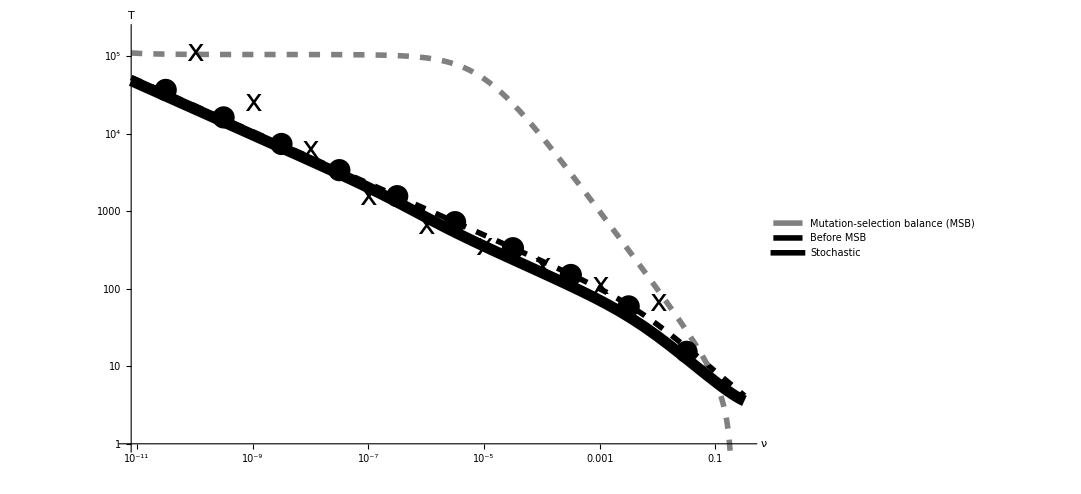

```mathematica
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1.01; 
n=10^6;
μ=5*10^-7;
xmin=0.8*10^-11;
xmax=10^(-1/2);

Legended[
Show[

(*semi-deterministic equation with recombination and selection*)
LogLogPlot[TDetR/.CN/.N->n,{ν,xmin,xmax},PlotStyle->{Black,Thickness[0.005],Dashing[0.01]},PlotRange->{{xmin,xmax},{1,2*10^5}}],

(*semi-deterministic equation with MSB*)
LogLogPlot[TDetMutSel/.CN/.N->n/.N->n,{ν,xmin,xmax},PlotStyle->{Gray,Thickness[0.005],Dashing[0.01]}],

(*stochastic equation with recombination*)
LogLogPlot[TStochR/.CN/.N->n/.c->ν/μ,{ν,xmin,xmax},PlotStyle->{Black,Thickness[0.01]}],

(*full semi-deterministic solution*)
ListLogLogPlot[Table[{10^x,T/.FindRoot[(x4pDMSum/.CN/.N->n/.U->μ+ν/.ν->10^x)==(1/n),{T,10^3},WorkingPrecision->50]},{x,-25/2,-3/2,1}],PlotStyle->{Black,PointSize[.02]}],

ListLogLogPlot[
{
{10^-10,CytoNu0},
{10^-9,CytoNui},
{10^-8,CytoNuii},
{10^-7,CytoNuiii},
{10^-6,CytoNuiv},
{10^-5,CytoNuv},
{10^-4,CytoNuvi},
{10^-3,CytoNuvii},
{10^-2,CytoNuviii}
},
PlotMarkers->{"x",30},
PlotStyle->{Black}],

AxesLabel->{Style["ν",AxisSize],Style["T",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],
Placed[
LineLegend[
{Directive[Thickness[0.2],Gray,Dashing[Medium]],Directive[Thickness[0.2],Black,Dashing[Medium]],Directive[Thickness[0.25],Black]},
{Style["Mutation-selection balance (MSB)",24],Style["Before MSB",24],Style["Stochastic",24]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.17}
]
]

Export[dir<>"TimeFixUniLogNuSimsBW.eps",%];

Clear[n,xmin,xmax,μ,w]
```

#### Figure 3 (bottom)

FindRoot::precw: The precision of the argument function (-1.28207×10^32\ (29999400003\ (1 - Power[« 2 »]/1000000)^2\ (-1 + 99999\ Plus[« 2 »]\ Plus[« 2 »]/100000)^4/50000000000000000000000000000000000000000000\ √10\ (1 + Power[« 2 »]/1000)^4 + « 73 » + « 540 ») == 1/1000000) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (-1.28163×10^32\ (29999400003\ (1 - Power[« 2 »]/1000000)^2\ (-1 + 99999\ Plus[« 2 »]\ Plus[« 2 »]/100000)^4/50000000000000000000000000000000000000000\ √10\ (1 + 1/100\ Power[« 2 »])^4 + « 73 » + « 540 ») == 1/1000000) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (-1.27751×10^32\ (29999400003\ (1 - Power[« 2 »]/1000000)^2\ (-1 + 99999\ Plus[« 2 »]\ Plus[« 2 »]/100000)^4/50000000000000000000000000000000000000\ √10\ (1 + 1/10\ Power[« 2 »])^4 + « 73 » + « 540 ») == 1/1000000) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

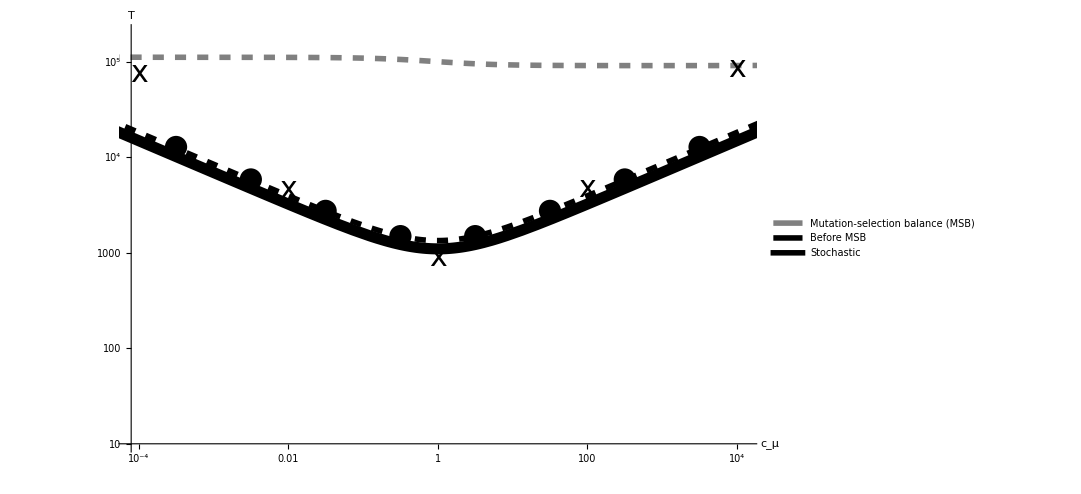

```mathematica
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1.01; 
n=10^6;
U=2*5*10^-7;
m1=5;
m2=5;

Legended[
Show[

(*full semi-deterministic solution*)
ListLogLogPlot[Table[{10^x,T/.FindRoot[(SumCN/.N->n/.c->10^x)==(1/n),{T,10^4},WorkingPrecision->50]},{x,-7/2,7/2,1}],PlotStyle->{Black,PointSize[.02]},PlotRange->{{10^-4.1,10^4.1},{10,2*10^5}}],

(*semi-deterministic equation with recombination and selection*)
LogLogPlot[TDetRCN/.N->n,{c,10^-m1,10^m2},PlotStyle->{Black,Thickness[0.005],Dashing[0.01]}],

(*semi-deterministic equation with MSB*)
LogLogPlot[TMSBCN/.N->n,{c,10^-m1,10^m2},PlotStyle->{Gray,Thickness[0.005],Dashing[0.01]}],

(*stochastic equation with recombination*)
LogLogPlot[TStochRCN/.N->n,{c,10^-m1,10^m2},PlotStyle->{Black,Thickness[0.01]}],

ListLogLogPlot[
{
{10^-4,CytoTime0},
{10^-2,CytoTimei},
{10^0,CytoTimeii},
{10^2,CytoTimeiii},
{10^4,CytoTimeiv}
},
PlotMarkers->{"x",30},
PlotStyle->{Black}],

AxesLabel->{Style["c_μ",AxisSize],Style["T",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],
Placed[
LineLegend[
{Directive[Thickness[0.2],Gray,Dashing[Medium]],Directive[Thickness[0.2],Black,Dashing[Medium]],Directive[Thickness[0.25],Black]},
{Style["Mutation-selection balance (MSB)",24],Style["Before MSB",24],Style["Stochastic",24]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.2}
]
]

Export[dir<>"TimeFixUniLogU2SimsBW.eps",%];

Clear[n,m1,m2,U,w]
```

#### Figure 4

```mathematica
w[2]=1-10^-5;
w[3]=w[2];
w[4]=1+1.01;
n=10^6;
ν= c μ;
U=2*5*10^-7;
NM=200;
xmin=0.9*1;
xmax=1.1*10^4;
ymin=0;
ymax=1.05;

Legended[
Show[

(*stochastic crossing probability by recombination, holding total mutation and initial number of single mutants constant*)
LogLinearPlot[PStochRCN/.N->n/.i0->NM/(1+c)/.μ->U/(1+c),{c,xmin,xmax},PlotStyle->{Black,Thickness[0.01]},PlotRange->{ymin,ymax}],

(*stochastic crossing probability by recombination, holding μ and i0 constant*)
LogLinearPlot[PStochRCN/.N->n/.i0->NM/2/.μ->U/2,{c,xmin,xmax},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{ymin,ymax}],

(*simulation results*)
ListLogLinearPlot[
{{10^0,CytoProbGrayi},
{10^1,CytoProbGrayii},
{10^2,CytoProbGrayiii},
{10^3,CytoProbGrayiv},
{10^4,CytoProbGrayiv}},
PlotMarkers->{"x",30},
PlotStyle->{Gray}],

ListLogLinearPlot[
{{10^0,CytoProbBlacki},
{10^1,CytoProbBlackii},
{10^2,CytoProbBlackiii},
{10^3,CytoProbBlackiv},
{10^4,CytoProbBlackv}},
PlotMarkers->{"x",30},
PlotStyle->{Black}],

AxesLabel->{Style["c_n",AxisSize],Style["P",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],
Placed[
LineLegend[
{Directive[Thickness[0.25],Gray],Directive[Thickness[0.25],Black]},
(*{Style["μ, i_0 constant",24],Style["μ+ν, i_0+j_0 constant",24]},*)
{Style["nuclear mutation & i_0 constant",24],Style["total mutation & i_0+j_0 constant",24]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.5}
]
]

Export[dir<>"ProbFixUniS2Sims.eps",%];

Clear[n,w,U,ν,NM,xmin,xmax,ymin,ymax]
```

-Graphics-

### 3. Cultural inheritance

#### Figure 5

```mathematica
w[1]=1; 
w[2]=1;
w[3]=1;
w[4]=1;
n=10^3;
μ=10^-3;
r=1/100;
qmin=0;
qmax=52/100;
ymax=10^5;

Legended[
Show[

p=51/100;

(*full semi-deterministic result*)
ListLogPlot[Table[{q,T/.FindRoot[(CultSum/.N->n)==(1/n),{T,10^2},WorkingPrecision->50]},{q,2/100,6/10,51/1000}],PlotStyle->{Black,PointSize[.01]},PlotRange->{{qmin,qmax},{1,ymax}}],

(*semi-deterministic solution from MSB*)
LogPlot[TMSBCult/.N->n,{q,qmin,0.495},PlotStyle->{Black,Thickness[0.002]}],

p=60/100;

(*full semi-deterministic result*)
ListLogPlot[Table[{q,T/.FindRoot[(CultSum/.N->n)==(1/n),{T,10^2},WorkingPrecision->50]},{q,2/100,6/10,51/1000}],PlotStyle->{Black,PointSize[.02]},PlotRange->{{qmin,qmax},{1,ymax}}],

(*semi-deterministic solution from MSB*)
LogPlot[TMSBCult/.N->n,{q,qmin,0.485},PlotStyle->{Black,Thickness[0.005]}],

(*simulation results*)
ListLogPlot[
{{0.1,CultTimeThicki},
{0.2,CultTimeThickii},
{0.3,CultTimeThickiii},
{0.4,CultTimeThickiv},
{0.5,CultTimeThickv}},
PlotMarkers->{"x",50},
PlotStyle->{Black}],

ListLogPlot[
{{0.1,CultTimeThini},
{0.2,CultTimeThinii},
{0.3,CultTimeThiniii},
{0.4,CultTimeThiniv},
{0.5,CultTimeThinv}},
PlotMarkers->{"x",30},
PlotStyle->{Black}],

AxesLabel->{Style["q",AxisSize],Style["T",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],

Placed[
LineLegend[
{Directive[Thickness[0.05],Black],Directive[Thickness[0.2],Black]},
{Style["Weak A_2B_2 transmission advantage",24],Style["Strong A_2B_2 transmission advantage",24]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.25}
]
]

Export[dir<>"TimeFixCultLogPSimsBW.eps",%];

Clear[n,μ,w,r,qmin,qmax,p,ymax]
```

-Graphics-

#### Figure 6

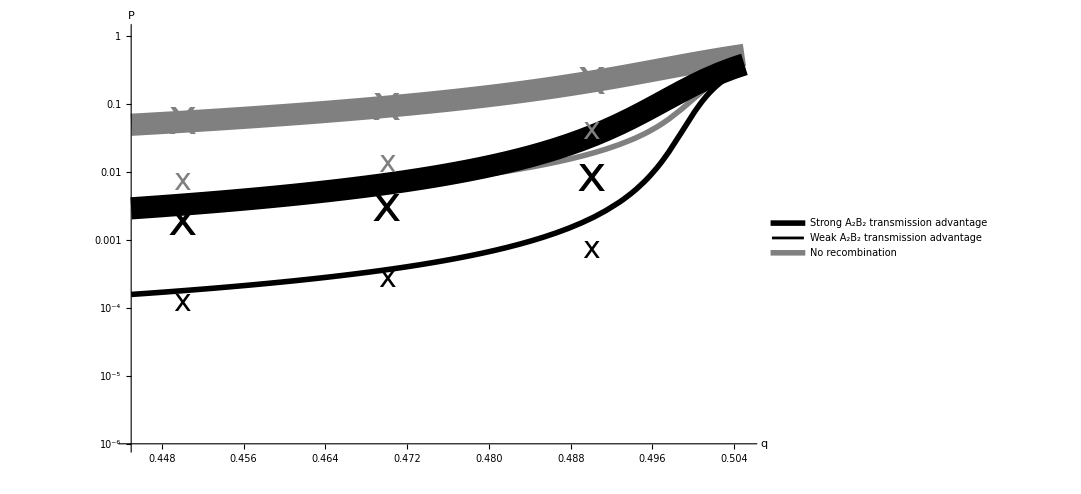

```mathematica
w[1]=1;
w[2]=1;
w[3]=1;
w[4]=1;
n=10^3;
μ=10^-3;
r=0.01;
c=1;
qmin=0.445;
qmax=0.505;
n0=20;
i0=n0/2;

Legended[
Show[
p=0.51;

(*stochastic crossing probability, by mutation*)
LogPlot[PStochMutCult/.N->n,{q,qmin,qmax},PlotStyle->{Gray,Thickness[0.005]},PlotRange->{0.1*10^-5,1.1}],
(*stochastic crossing probability, by recombination*)
LogPlot[PStochRCult/.N->n,{q,qmin,qmax},PlotStyle->{Black,Thickness[0.005]}],

p=0.6;

(*stochastic crossing probability, by mutation*)
LogPlot[PStochMutCult/.N->n,{q,qmin,qmax},PlotStyle->{Gray,Thickness[0.02]},PlotRange->{10^-3,1.1}],
(*stochastic crossing probability, by recombination*)
LogPlot[PStochRCult/.N->n,{q,qmin,qmax},PlotStyle->{Black,Thickness[0.02]}],

(*simulation results*)
ListLogPlot[
{{0.45,CultProbGrayThicki},
{0.47,CultProbGrayThickii},
{0.49,CultProbGrayThickiii}},
PlotMarkers->{"x",50},
PlotStyle->{Gray}],

ListLogPlot[
{{0.45,CultProbGrayThini},
{0.47,CultProbGrayThinii},
{0.49,CultProbGrayThiniii}},
PlotMarkers->{"x",30},
PlotStyle->{Gray}],

ListLogPlot[
{{0.45,CultProbBlackThicki},
{0.47,CultProbBlackThickii},
{0.49,CultProbBlackThickiii}},
PlotMarkers->{"x",50},
PlotStyle->{Black}],

ListLogPlot[
{{0.45,CultProbBlackThini},
{0.47,CultProbBlackThinii},
{0.49,CultProbBlackThiniii}},
PlotMarkers->{"x",30},
PlotStyle->{Black}],

AxesLabel->{Style["q",AxisSize],Style["P",AxisSize]},
ImageSize->imagesize,
ImagePadding->imagepadding,
TicksStyle->TickSize,
PlotRangePadding->None
],

Placed[
LineLegend[
{Directive[Thickness[0.25],Black],Directive[Thickness[0.1],Black], Directive[Thickness[0.25],Gray]},
{Style["Strong A_2B_2 transmission advantage",24],Style["Weak A_2B_2 transmission advantage",24],Style["No recombination",24]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.65,0.2}
]
]

Export[dir<>"ProbFixCultPSims.eps",%];

Clear[n,μ,w,r,c,qmin,qmax,p,n0,i0]
```